# Discrete Fourier Transform of ise7.dat

## compare FFTW and Mathematica

## Data

```mathematica
Data={{0.14064,-0.01208},{0.20864,-0.00808},{0.21264,-0.01208},{0.19264,-0.01208},{0.19264,-0.00808},{0.19264,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00336,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01608},{-0.00336,-0.00808},{-0.00336,-0.00808},{-0.01136,-0.01608},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00336,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.00336,-0.01608},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.01208},{-0.00736,-0.01608},{-0.01136,-0.01208},{-0.00336,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.00736,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01608},{-0.00336,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00336,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.01536,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.01536,-0.00808},{-0.01536,-0.01608},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00008},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00808},{-0.01136,-0.00008},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.00736,-0.00008},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.00736,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.00736,-0.00008},{-0.00736,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00008},{-0.00736,-0.00008},{-0.01536,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01936,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.01208},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00336,-0.00808},{0.00064,-0.00408},{0.00064,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00808},{0.00064,-0.00808},{-0.00336,-0.00808},{0.00064,-0.01208},{0.00064,-0.01208},{-0.00336,-0.00808},{-0.00336,-0.00408},{0.00064,-0.00808},{0.00064,-0.00808},{0.00064,-0.01208},{0.00064,-0.00408},{0.00064,-0.00408},{-0.00336,-0.00808},{0.00064,-0.00808},{0.00064,-0.00408},{0.00064,-0.00808},{0.00064,-0.00408},{0.00064,-0.00808},{0.00464,-0.00808},{0.00464,-0.00808},{0.00464,-0.00008},{0.00464,-0.00008},{0.00464,-0.00408},{0.00064,-0.00408},{0.00464,-0.00408},{0.00864,-0.00408},{0.00864,-0.00008},{0.00864,-0.00008},{0.00864,-0.00408},{0.00864,-0.00408},{0.00464,-0.00408},{0.00864,-0.00008},{0.00864,-0.00008},{0.00864,-0.00408},{0.00864,-0.00008},{0.00864,-0.00008},{0.00864,0.00392},{0.00864,0.00392},{0.00864,-0.00008},{0.01264,-0.00008},{0.01664,-0.00008},{0.01264,-0.00008},{0.01264,0.00392},{0.01664,-0.00008},{0.01664,0.00392},{0.00864,0.00392},{0.01264,0.00392},{0.02064,0.00392},{0.01264,-0.00408},{0.01664,0.00392},{0.02064,-0.00008},{0.01264,-0.00008},{0.02064,-0.00008},{0.01264,-0.00008},{0.01664,-0.00008},{0.01664,-0.00008},{0.01664,-0.00008},{0.02064,-0.00008},{0.02064,-0.00008},{0.01664,-0.00008},{0.02064,-0.00008},{0.01664,-0.00008},{0.02064,-0.00008},{0.01664,-0.00008},{0.01664,-0.00408},{0.01264,-0.00008},{0.01664,-0.00008},{0.01664,-0.00008},{0.01664,-0.00408},{0.01664,-0.00808},{0.02064,-0.00408},{0.01664,-0.00808},{0.02064,-0.00408},{0.01664,-0.00808},{0.02464,-0.00808},{0.02064,-0.00808},{0.02064,-0.01208},{0.02064,-0.00808},{0.02064,-0.00808},{0.02064,-0.00808},{0.02064,-0.00808},{0.02464,-0.00808},{0.02064,-0.01208},{0.02064,-0.01208},{0.02464,-0.01208},{0.02064,-0.01608},{0.02464,-0.01608},{0.02464,-0.00808},{0.02064,-0.01608},{0.02464,-0.01608},{0.02464,-0.01608},{0.02464,-0.01608},{0.02064,-0.01608},{0.02064,-0.02008},{0.02064,-0.02008},{0.02464,-0.02008},{0.02464,-0.01608},{0.02464,-0.01608},{0.02464,-0.01208},{0.02464,-0.02008},{0.02064,-0.02008},{0.02064,-0.02008},{0.02864,-0.02008},{0.01264,-0.02408},{0.02464,-0.02408},{0.02064,-0.02008},{0.02064,-0.02408},{0.02064,-0.02008},{0.02064,-0.02408},{0.02064,-0.02408},{0.02064,-0.02408},{0.01664,-0.02008},{0.02464,-0.02408},{0.02064,-0.02408},{0.01664,-0.02808},{0.02064,-0.02808},{0.01664,-0.02408},{0.01664,-0.03208},{0.01264,-0.02808},{0.01664,-0.02808},{0.01664,-0.02808},{0.01664,-0.03208},{0.00864,-0.03208},{0.01264,-0.02808},{0.01264,-0.03208},{0.01264,-0.03208},{0.00864,-0.03208},{0.00064,-0.03608},{0.00064,-0.03608},{0.00464,-0.04008},{0.00064,-0.03608},{-0.00336,-0.04408},{-0.01136,-0.04808},{-0.01136,-0.04808},{-0.01936,-0.04408},{-0.01536,-0.04808},{-0.02336,-0.04408},{-0.03136,-0.04408},{-0.03136,-0.04808},{-0.03536,-0.05208},{-0.04336,-0.05208},{-0.05136,-0.05208},{-0.05536,-0.05208},{-0.06336,-0.05208},{-0.06736,-0.05208},{-0.07536,-0.05208},{-0.07936,-0.05608},{-0.08336,-0.05208},{-0.09136,-0.05208},{-0.09936,-0.05608},{-0.10736,-0.05608},{-0.11136,-0.05608},{-0.12336,-0.06008},{-0.12736,-0.06008},{-0.13936,-0.05608},{-0.14336,-0.05608},{-0.14736,-0.05608},{-0.16336,-0.05608},{-0.16736,-0.06008},{-0.17536,-0.05608},{-0.17936,-0.06408},{-0.19136,-0.06008},{-0.19536,-0.06008},{-0.20336,-0.05608},{-0.21136,-0.06008},{-0.21936,-0.06408},{-0.22736,-0.06008},{-0.23936,-0.06008},{-0.24336,-0.06008},{-0.25536,-0.06008},{-0.26336,-0.06408},{-0.26736,-0.05608},{-0.27936,-0.06408},{-0.28736,-0.06408},{-0.29936,-0.05608},{-0.30336,-0.06408},{-0.30736,-0.06008},{-0.31936,-0.06408},{-0.32736,-0.05608},{-0.33536,-0.06008},{-0.33936,-0.05608},{-0.35136,-0.06008},{-0.35936,-0.05608},{-0.36736,-0.06008},{-0.37936,-0.06008},{-0.38336,-0.05608},{-0.39136,-0.05608},{-0.39936,-0.05608},{-0.41136,-0.05608},{-0.41936,-0.05608},{-0.42336,-0.06008},{-0.43536,-0.06008},{-0.43936,-0.05208},{-0.45136,-0.05608},{-0.45936,-0.06008},{-0.46736,-0.05608},{-0.47136,-0.05208},{-0.48336,-0.05608},{-0.48336,-0.04808},{-0.49136,-0.05608},{-0.50336,-0.05208},{-0.50736,-0.05208},{-0.50736,-0.05208},{-0.50736,-0.04808},{-0.50736,-0.04808},{-0.50736,-0.05208},{-0.50736,-0.04808},{-0.50736,-0.04808},{-0.50736,-0.05208},{-0.50736,-0.05208},{-0.50736,-0.04808},{-0.50736,-0.04408},{-0.50736,-0.04808},{-0.50736,-0.04008},{-0.50736,-0.04808},{-0.50736,-0.04808},{-0.50736,-0.04408},{-0.50736,-0.04008},{-0.50736,-0.04408},{-0.50736,-0.04408},{-0.50736,-0.04408},{-0.50736,-0.04008},{-0.50736,-0.03208},{-0.50736,-0.04008},{-0.50736,-0.04008},{-0.50736,-0.04008},{-0.50736,-0.03608},{-0.50736,-0.03608},{-0.50736,-0.04008},{-0.50736,-0.03208},{-0.50736,-0.03608},{-0.50736,-0.02808},{-0.50736,-0.03608},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.02808},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03208},{-0.50736,-0.03608},{-0.50736,-0.03208},{-0.50736,-0.03608},{-0.50736,-0.03608},{-0.50736,-0.03608},{-0.50736,-0.04008},{-0.50736,-0.03208},{-0.50736,-0.04008},{-0.50736,-0.04008},{-0.50736,-0.04408},{-0.50736,-0.04408},{-0.50736,-0.04408},{-0.50736,-0.05208},{-0.50736,-0.04808},{-0.50736,-0.05208},{-0.50736,-0.05208},{-0.50736,-0.05608},{-0.50736,-0.06008},{-0.50736,-0.05608},{-0.50736,-0.05608},{-0.50736,-0.06408},{-0.50736,-0.06808},{-0.50736,-0.06408},{-0.50736,-0.06808},{-0.50736,-0.06408},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.07608},{-0.50736,-0.07208},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.08008},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.07608},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08408},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08408},{-0.50736,-0.08008},{-0.50736,-0.07608},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.08008},{-0.50736,-0.07608},{-0.50736,-0.08408},{-0.50736,-0.08008},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07608},{-0.50736,-0.07208},{-0.50736,-0.07608},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.06808},{-0.50736,-0.06808},{-0.50736,-0.07208},{-0.50736,-0.07208},{-0.50736,-0.06808},{-0.50736,-0.06808},{-0.50336,-0.06808},{-0.49536,-0.06808},{-0.48736,-0.06808},{-0.48336,-0.06408},{-0.47536,-0.06408},{-0.47136,-0.06408},{-0.45936,-0.06808},{-0.45136,-0.06408},{-0.44336,-0.06008},{-0.43536,-0.06008},{-0.42736,-0.06008},{-0.41936,-0.05608},{-0.41536,-0.06008},{-0.40736,-0.06008},{-0.40336,-0.06008},{-0.39536,-0.05208},{-0.38736,-0.05608},{-0.37936,-0.05608},{-0.37536,-0.05608},{-0.35936,-0.05208},{-0.35936,-0.05208},{-0.34736,-0.05208},{-0.34736,-0.05208},{-0.33536,-0.04808},{-0.33136,-0.04808},{-0.32736,-0.04808},{-0.31936,-0.04808},{-0.31136,-0.04408},{-0.30736,-0.04408},{-0.30336,-0.04408},{-0.29136,-0.04408},{-0.28736,-0.04008},{-0.27936,-0.03608},{-0.27536,-0.03608},{-0.27136,-0.03608},{-0.26736,-0.03208},{-0.25936,-0.03608},{-0.25536,-0.02808},{-0.25136,-0.03208},{-0.24336,-0.03208},{-0.24336,-0.02408},{-0.23136,-0.02408},{-0.23136,-0.02408},{-0.22336,-0.02008},{-0.22336,-0.02008},{-0.21536,-0.01608},{-0.20736,-0.01208},{-0.20736,-0.01208},{-0.20336,-0.01208},{-0.19936,-0.01208},{-0.19136,-0.00808},{-0.19136,-0.00408},{-0.18736,-0.00408},{-0.18336,-0.00008},{-0.18336,0.00792},{-0.17136,0.00392},{-0.17136,0.00792},{-0.16736,0.01192},{-0.16336,0.01592},{-0.15936,0.01992},{-0.16336,0.01992},{-0.15536,0.02392},{-0.15136,0.02792},{-0.15136,0.03192},{-0.14736,0.03192},{-0.14336,0.03192},{-0.13536,0.03592},{-0.13536,0.04392},{-0.13536,0.04792},{-0.13136,0.04792},{-0.12736,0.05192},{-0.12736,0.05592},{-0.12736,0.05992},{-0.12336,0.05992},{-0.12336,0.06792},{-0.12336,0.07192},{-0.11536,0.07192},{-0.11536,0.07192},{-0.11536,0.07592},{-0.11136,0.07992},{-0.11136,0.08392},{-0.10736,0.08392},{-0.10736,0.08792},{-0.10736,0.09192},{-0.10336,0.09592},{-0.10336,0.09592},{-0.09936,0.09992},{-0.09936,0.10392},{-0.09936,0.10392},{-0.09536,0.11192},{-0.09136,0.11192},{-0.09136,0.11592},{-0.08736,0.11592},{-0.09136,0.11992},{-0.09136,0.12392},{-0.08336,0.12392},{-0.08336,0.12792},{-0.08336,0.12792},{-0.08736,0.13192},{-0.07936,0.13592},{-0.07936,0.13592},{-0.07936,0.13592},{-0.07936,0.14392},{-0.07936,0.14392},{-0.07136,0.14792},{-0.07136,0.15192},{-0.07136,0.14792},{-0.07136,0.14792},{-0.07136,0.15192},{-0.07136,0.15592},{-0.07136,0.15992},{-0.07136,0.16392},{-0.07136,0.15992},{-0.07136,0.16392},{-0.06336,0.16792},{-0.07136,0.17192},{-0.06736,0.17192},{-0.07136,0.17592},{-0.06736,0.17992},{-0.06736,0.18392},{-0.06736,0.18792},{-0.06736,0.18792},{-0.06736,0.18792},{-0.06736,0.19192},{-0.06336,0.18792},{-0.06336,0.19992},{-0.06736,0.19992},{-0.06336,0.19992},{-0.06336,0.19992},{-0.06336,0.20392},{-0.06336,0.20392},{-0.05936,0.21192},{-0.06336,0.21592},{-0.05936,0.21992},{-0.05936,0.21592},{-0.05136,0.21992},{-0.05536,0.21992},{-0.05936,0.21992},{-0.05536,0.22392},{-0.05536,0.22392},{-0.05536,0.23192},{-0.05536,0.23192},{-0.05536,0.23192},{-0.05136,0.23192},{-0.05136,0.23192},{-0.04736,0.22792},{-0.05136,0.23192},{-0.04736,0.23592},{-0.04336,0.23592},{-0.04336,0.23192},{-0.04336,0.23992},{-0.04336,0.23992},{-0.04336,0.23992},{-0.04336,0.24392},{-0.03936,0.23992},{-0.04336,0.24392},{-0.03936,0.24392},{-0.04336,0.24392},{-0.03936,0.23992},{-0.03936,0.24792},{-0.04336,0.24392},{-0.03936,0.24392},{-0.03936,0.24392},{-0.03536,0.24392},{-0.03536,0.24392},{-0.03936,0.23992},{-0.03936,0.24792},{-0.03936,0.24392},{-0.03536,0.24792},{-0.03936,0.24392},{-0.03536,0.24792},{-0.03536,0.24392},{-0.03936,0.24392},{-0.03136,0.24392},{-0.03536,0.24392},{-0.03536,0.23992},{-0.03136,0.23992},{-0.03536,0.23992},{-0.03936,0.23992},{-0.03136,0.23992},{-0.03136,0.23992},{-0.03136,0.23592},{-0.03136,0.23992},{-0.03136,0.23592},{-0.02736,0.23992},{-0.03136,0.23192},{-0.02736,0.23192},{-0.02736,0.23192},{-0.02336,0.23192},{-0.03136,0.23192},{-0.02736,0.23192},{-0.02736,0.23192},{-0.03136,0.23592},{-0.02736,0.23592},{-0.02736,0.22792},{-0.02736,0.22792},{-0.03136,0.23192},{-0.02336,0.23192},{-0.02336,0.22792},{-0.01936,0.23192},{-0.02336,0.23192},{-0.02336,0.23192},{-0.02736,0.23592},{-0.02336,0.23192},{-0.02336,0.23592},{-0.01936,0.22792},{-0.01936,0.22792},{-0.01936,0.23192},{-0.01936,0.23192},{-0.01936,0.22392},{-0.01536,0.22792},{-0.01536,0.22792},{-0.01536,0.22792},{-0.01536,0.23192},{-0.01536,0.22792},{-0.01136,0.22392},{-0.01136,0.22392},{-0.01136,0.21992},{-0.00736,0.22392},{-0.01136,0.22792},{-0.00736,0.22792},{-0.00336,0.22392},{-0.00336,0.22392},{-0.00336,0.21992},{-0.00336,0.22392},{-0.00336,0.21992},{-0.00336,0.21992},{-0.00336,0.21992},{0.00064,0.21992},{0.00464,0.22392},{0.00464,0.21992},{0.00064,0.21992},{0.00464,0.21992},{0.00464,0.21592},{0.00864,0.21592},{0.00864,0.21192},{0.00864,0.21592},{0.00864,0.21192},{0.00864,0.21192},{0.01264,0.21192},{0.01664,0.21192},{0.01664,0.21192},{0.01664,0.20792},{0.02064,0.20792},{0.02064,0.21192},{0.01664,0.20792},{0.02064,0.20792},{0.02064,0.20392},{0.02064,0.20792},{0.02064,0.20392},{0.02064,0.20392},{0.02864,0.19992},{0.02864,0.19992},{0.02464,0.19992},{0.02864,0.19592},{0.02864,0.19592},{0.02464,0.19592},{0.03264,0.19192},{0.02864,0.19192},{0.03664,0.19192},{0.03664,0.19592},{0.03664,0.18792},{0.03264,0.18392},{0.03664,0.18392},{0.03664,0.18392},{0.03664,0.18392},{0.03664,0.17992},{0.03664,0.17992},{0.03664,0.17992},{0.04064,0.17992},{0.04064,0.17592},{0.04464,0.17192},{0.04464,0.17592},{0.03664,0.17192},{0.04464,0.16792},{0.04064,0.16792},{0.05264,0.16792},{0.04864,0.16392},{0.04464,0.16392},{0.04864,0.16392},{0.05264,0.16392},{0.04464,0.15992},{0.04864,0.15592},{0.05264,0.15592},{0.04864,0.15192},{0.04864,0.15192},{0.04864,0.15192},{0.05264,0.15192},{0.05264,0.15192},{0.05264,0.14792},{0.05264,0.14792},{0.05264,0.13992},{0.05264,0.13992},{0.05264,0.13992},{0.05664,0.13992},{0.05264,0.13192},{0.05264,0.13592},{0.05264,0.13192},{0.05264,0.13192},{0.05264,0.12792},{0.05264,0.12792},{0.05264,0.12392},{0.05264,0.11992},{0.05264,0.11592},{0.05664,0.11992},{0.05264,0.11592},{0.04864,0.11192},{0.05264,0.11592},{0.05264,0.11192},{0.05264,0.11192},{0.05264,0.11192},{0.05264,0.10792},{0.05264,0.10792},{0.05264,0.10392},{0.05264,0.09992},{0.05264,0.09992},{0.05264,0.09592},{0.05264,0.09592},{0.04864,0.09192},{0.05264,0.09192},{0.04864,0.09592},{0.04464,0.08392},{0.05264,0.08392},{0.05264,0.08792},{0.04864,0.08392},{0.04864,0.08392},{0.04864,0.07992},{0.04864,0.07592},{0.04464,0.07592},{0.04864,0.07592},{0.04464,0.07592},{0.04464,0.06792},{0.04864,0.06792},{0.04464,0.06392},{0.04064,0.05992},{0.04064,0.06392},{0.04064,0.05992},{0.04064,0.05992},{0.04064,0.05192},{0.03664,0.05192},{0.03664,0.04792},{0.03664,0.05592},{0.03664,0.04792},{0.03664,0.04392},{0.04064,0.04392},{0.03664,0.03992},{0.03664,0.03992},{0.03264,0.03992},{0.03264,0.03992},{0.03264,0.03192},{0.03264,0.03192},{0.02864,0.03192},{0.02864,0.02792},{0.02864,0.02792},{0.02864,0.03192},{0.03264,0.02392},{0.02864,0.01992},{0.02464,0.01992},{0.02464,0.01592},{0.02464,0.01592},{0.02864,0.01592},{0.02064,0.01592},{0.02064,0.01192},{0.02064,0.01192},{0.01664,0.00392},{0.01664,0.00392},{0.02064,-0.00008},{0.01664,0.00392},{0.01264,0.00392},{0.01664,-0.00008},{0.01264,-0.00008},{0.00864,-0.00008},{0.00864,-0.00408},{0.00464,-0.00808},{0.00864,-0.01208},{0.00464,-0.01208},{0.00864,-0.01208},{0.00464,-0.00808},{0.00064,-0.01208},{0.00064,-0.01208},{0.00464,-0.01608},{0.00064,-0.01608},{0.00064,-0.02008},{-0.00336,-0.01608},{-0.00336,-0.02408},{-0.00736,-0.02408},{-0.01136,-0.02408},{-0.00736,-0.02408},{-0.00736,-0.02808},{-0.01136,-0.02808},{-0.01136,-0.02808},{-0.01536,-0.03208},{-0.01536,-0.02808},{-0.01536,-0.03208},{-0.01536,-0.03608},{-0.01536,-0.03608},{-0.01536,-0.03608},{-0.01936,-0.03208},{-0.01936,-0.04408},{-0.02336,-0.04008},{-0.02736,-0.04008},{-0.02736,-0.04008},{-0.02736,-0.04008},{-0.02736,-0.04008},{-0.02736,-0.04008},{-0.03536,-0.03608},{-0.03136,-0.04408},{-0.03136,-0.04408},{-0.03136,-0.04408},{-0.03536,-0.04408},{-0.03536,-0.04808},{-0.03536,-0.04008},{-0.03536,-0.04808},{-0.04336,-0.04808},{-0.03936,-0.04808},{-0.03936,-0.04408},{-0.04736,-0.05208},{-0.03936,-0.04408},{-0.04736,-0.04408},{-0.04736,-0.04808},{-0.04736,-0.04808},{-0.05536,-0.05208},{-0.05136,-0.05208},{-0.05136,-0.05208},{-0.05136,-0.05208},{-0.05136,-0.05208},{-0.05136,-0.05608},{-0.05536,-0.05608},{-0.05536,-0.05208},{-0.05536,-0.05208},{-0.05936,-0.05208},{-0.05936,-0.05208},{-0.05936,-0.05608},{-0.06336,-0.05608},{-0.06736,-0.05208},{-0.07136,-0.05608},{-0.06736,-0.06008},{-0.06336,-0.06008},{-0.06336,-0.05608},{-0.06736,-0.05608},{-0.07136,-0.06008},{-0.07136,-0.06008},{-0.07136,-0.06008},{-0.07136,-0.06008},{-0.07136,-0.06008},{-0.07136,-0.05608},{-0.07136,-0.06008},{-0.07536,-0.05608},{-0.07536,-0.06008},{-0.07536,-0.06408},{-0.07936,-0.06008},{-0.07136,-0.06008},{-0.08336,-0.06408},{-0.07936,-0.05608},{-0.07936,-0.05608},{-0.07936,-0.06008},{-0.07936,-0.06008},{-0.08336,-0.06008},{-0.07936,-0.06008},{-0.08336,-0.05608},{-0.09136,-0.05608},{-0.08336,-0.05608},{-0.08736,-0.06008},{-0.08736,-0.06008},{-0.09136,-0.05608},{-0.09136,-0.05608},{-0.08736,-0.05608},{-0.09536,-0.06008},{-0.09536,-0.06008},{-0.09136,-0.06008},{-0.08736,-0.06008},{-0.09536,-0.05608},{-0.09536,-0.04808},{-0.09136,-0.05608},{-0.09136,-0.06008},{-0.09136,-0.05608},{-0.09536,-0.05608},{-0.09536,-0.05608},{-0.09136,-0.05608},{-0.09536,-0.05608},{-0.09536,-0.06008},{-0.09536,-0.05208},{-0.09536,-0.05608},{-0.09536,-0.05208},{-0.09936,-0.05608},{-0.10336,-0.06008},{-0.09936,-0.05608},{-0.10336,-0.05608},{-0.09936,-0.05608},{-0.10736,-0.05208},{-0.09936,-0.05208},{-0.09936,-0.05608},{-0.09936,-0.05608},{-0.10336,-0.05208},{-0.10336,-0.04808},{-0.10336,-0.05208},{-0.09936,-0.04808},{-0.10336,-0.04808},{-0.10736,-0.05608},{-0.09936,-0.04808},{-0.10736,-0.04808},{-0.11136,-0.04808},{-0.11136,-0.04808},{-0.10736,-0.04408},{-0.10336,-0.04808},{-0.10736,-0.04808},{-0.10336,-0.04808},{-0.10736,-0.04808},{-0.10736,-0.04408},{-0.10336,-0.04408},{-0.10736,-0.04408},{-0.11136,-0.04408},{-0.10736,-0.04408},{-0.10736,-0.04008},{-0.11136,-0.04408},{-0.10736,-0.04408},{-0.10736,-0.04008},{-0.10736,-0.04008},{-0.10736,-0.04408},{-0.10736,-0.03608},{-0.10736,-0.04008},{-0.10736,-0.04008},{-0.11136,-0.04008},{-0.11136,-0.04008},{-0.10336,-0.03608},{-0.10736,-0.03608},{-0.11136,-0.03208},{-0.11536,-0.03608},{-0.11136,-0.03608},{-0.11136,-0.04008},{-0.10736,-0.03608},{-0.10736,-0.03208},{-0.10336,-0.03208},{-0.10736,-0.03208},{-0.11136,-0.02808},{-0.11136,-0.02808},{-0.11136,-0.03208},{-0.11136,-0.03608},{-0.10736,-0.03208},{-0.10736,-0.02808},{-0.10736,-0.03208},{-0.10736,-0.02808},{-0.10736,-0.02808},{-0.10336,-0.02408},{-0.10736,-0.03208},{-0.10736,-0.02808},{-0.10736,-0.02408},{-0.10736,-0.02808},{-0.10736,-0.03208},{-0.10736,-0.02408},{-0.10736,-0.02808},{-0.10336,-0.02408},{-0.10736,-0.02408},{-0.10336,-0.02408},{-0.10336,-0.02408},{-0.10736,-0.02408},{-0.10336,-0.02008},{-0.10336,-0.02008},{-0.09936,-0.02008},{-0.10336,-0.02008},{-0.09936,-0.02408},{-0.10336,-0.01608},{-0.09936,-0.02408},{-0.09936,-0.02008},{-0.09536,-0.01608},{-0.10336,-0.01608},{-0.09536,-0.01608},{-0.09936,-0.02008},{-0.09536,-0.01608},{-0.09936,-0.01208},{-0.09536,-0.01608},{-0.09536,-0.01608},{-0.09536,-0.01608},{-0.09936,-0.01608},{-0.09536,-0.01208},{-0.09536,-0.01608},{-0.09136,-0.02008},{-0.09136,-0.01608},{-0.09536,-0.01208},{-0.09136,-0.01208},{-0.09136,-0.01608},{-0.09136,-0.01208},{-0.09136,-0.01608},{-0.09136,-0.01608},{-0.09136,-0.01208},{-0.09136,-0.00808},{-0.08736,-0.01608},{-0.08336,-0.01208},{-0.09136,-0.00808},{-0.08736,-0.01208},{-0.08736,-0.01208},{-0.08336,-0.00808},{-0.08736,-0.00808},{-0.08336,-0.00808},{-0.08736,-0.00808},{-0.08336,-0.00808},{-0.08336,-0.01208},{-0.07936,-0.01208},{-0.08336,-0.00808},{-0.07936,-0.00808},{-0.07936,-0.00808},{-0.07936,-0.00808},{-0.07936,-0.00808},{-0.07936,-0.00808},{-0.07136,-0.01208},{-0.07536,-0.00808},{-0.07536,-0.00808},{-0.07536,-0.00808},{-0.07536,-0.01208},{-0.07136,-0.00808},{-0.07136,-0.00808},{-0.07136,-0.01208},{-0.07136,-0.00808},{-0.06736,-0.01208},{-0.07536,-0.01208},{-0.07136,-0.01208},{-0.06736,-0.01208},{-0.06736,-0.00808},{-0.06736,-0.01208},{-0.07136,-0.01208},{-0.06336,-0.00808},{-0.06736,-0.00808},{-0.06336,-0.00808},{-0.05936,-0.01208},{-0.06336,-0.00808},{-0.05936,-0.00808},{-0.05536,-0.01208},{-0.06336,-0.01208},{-0.05536,-0.00808},{-0.05536,-0.01208},{-0.05536,-0.00808},{-0.05536,-0.00808},{-0.05536,-0.01208},{-0.05536,-0.01208},{-0.05536,-0.01208},{-0.05536,-0.00808},{-0.05536,-0.01208},{-0.05136,-0.01208},{-0.04736,-0.00808},{-0.05536,-0.01208},{-0.05136,-0.01208},{-0.05136,-0.01208},{-0.05136,-0.00808},{-0.04336,-0.01208},{-0.04736,-0.01208},{-0.04736,-0.01208},{-0.04336,-0.01208},{-0.04336,-0.01208},{-0.04336,-0.01208},{-0.04336,-0.01208},{-0.04736,-0.01208},{-0.04336,-0.01208},{-0.03936,-0.00808},{-0.03936,-0.01608},{-0.03536,-0.01608},{-0.03536,-0.01608},{-0.03936,-0.01608},{-0.04336,-0.01608},{-0.03536,-0.01208},{-0.03936,-0.01608},{-0.03536,-0.02008},{-0.03136,-0.02008},{-0.03536,-0.02008},{-0.03136,-0.01608},{-0.03936,-0.02008},{-0.03136,-0.02008},{-0.03536,-0.02008},{-0.03136,-0.02008},{-0.03136,-0.02008},{-0.02736,-0.02008},{-0.02736,-0.02008},{-0.02736,-0.01608},{-0.03536,-0.01608},{-0.03136,-0.01608},{-0.02336,-0.02408},{-0.02736,-0.02008},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.02336,-0.01608},{-0.02336,-0.02408},{-0.01936,-0.02408},{-0.02336,-0.02408},{-0.01936,-0.02408},{-0.01936,-0.02008},{-0.01936,-0.02408},{-0.01936,-0.02808},{-0.01536,-0.02808},{-0.01936,-0.02808},{-0.01936,-0.02808},{-0.01536,-0.02408},{-0.01536,-0.02808},{-0.01536,-0.02408},{-0.01136,-0.02808},{-0.00736,-0.03208},{-0.01136,-0.02808},{-0.01136,-0.03208},{-0.01136,-0.03208},{-0.01136,-0.03608},{-0.01136,-0.03208},{-0.00736,-0.03608},{-0.00736,-0.03208},{-0.00736,-0.03208},{-0.00736,-0.03208},{-0.01136,-0.03608},{-0.00736,-0.03608},{-0.00336,-0.03608},{-0.00336,-0.04008},{0.00064,-0.04008},{-0.00336,-0.04008},{-0.00336,-0.04008},{-0.00336,-0.04008},{-0.00336,-0.04008},{-0.00736,-0.04008},{0.00064,-0.04808},{0.00064,-0.04408},{-0.00336,-0.04008},{0.00064,-0.04408},{0.00064,-0.04408},{0.00064,-0.04408},{-0.00336,-0.04808},{0.00064,-0.04808},{0.00064,-0.04408},{0.00464,-0.05208},{0.00464,-0.04808},{0.00464,-0.05208},{0.00064,-0.05208},{0.00064,-0.05208},{0.00864,-0.04808},{0.00464,-0.05208},{0.00464,-0.05208},{0.00864,-0.05208},{0.00864,-0.05208},{0.00464,-0.05208},{0.00464,-0.05608},{0.00464,-0.05608},{0.00864,-0.05608},{0.00864,-0.05608},{0.00864,-0.05608},{0.00864,-0.06008},{0.00464,-0.06008},{0.00464,-0.05608},{0.00864,-0.06408},{0.01264,-0.06008},{0.00864,-0.06008},{0.00864,-0.06008},{0.01264,-0.06408},{0.01264,-0.06408},{0.01264,-0.06808},{0.00864,-0.06408},{0.01264,-0.06408},{0.00864,-0.06008},{0.00864,-0.06808},{0.00864,-0.06808},{0.01264,-0.06408},{0.01264,-0.06808},{0.01264,-0.07208},{0.01264,-0.06808},{0.00864,-0.06808},{0.01264,-0.07208},{0.01664,-0.07208},{0.01664,-0.06808},{0.01264,-0.07208},{0.01264,-0.07608},{0.00864,-0.07208},{0.01264,-0.07608},{0.01264,-0.07608},{0.01264,-0.07608},{0.01264,-0.07608},{0.01664,-0.07608},{0.01264,-0.07608},{0.01264,-0.07608},{0.01664,-0.08008},{0.01664,-0.08008},{0.01264,-0.08408},{0.01664,-0.08008},{0.01264,-0.08408},{0.01264,-0.08008},{0.01264,-0.08008},{0.01664,-0.08008},{0.01664,-0.08008},{0.01264,-0.08808},{0.01264,-0.08408},{0.01264,-0.08008},{0.01264,-0.08408},{0.01264,-0.08808},{0.01664,-0.08808},{0.01664,-0.08808},{0.01664,-0.08808},{0.01264,-0.08808},{0.01664,-0.08808},{0.01264,-0.08808},{0.01264,-0.08808},{0.01664,-0.08808},{0.01664,-0.08808},{0.01264,-0.08808},{0.01664,-0.09208},{0.01664,-0.09208},{0.01264,-0.09208},{0.01264,-0.09208},{0.01264,-0.09208},{0.01264,-0.09608},{0.01664,-0.09208},{0.01264,-0.09608},{0.01264,-0.09608},{0.01664,-0.09208},{0.00864,-0.10008},{0.00864,-0.09608},{0.00864,-0.09608},{0.01264,-0.09208},{0.01664,-0.09608},{0.01264,-0.09608},{0.01264,-0.10008},{0.01264,-0.10008},{0.00864,-0.09608},{0.00864,-0.09608},{0.01264,-0.10008},{0.00864,-0.10008},{0.01264,-0.09608},{0.00864,-0.10408},{0.01264,-0.10008},{0.01264,-0.10008},{0.00864,-0.09608},{0.00864,-0.10008},{0.00864,-0.10408},{0.01264,-0.10008},{0.00864,-0.10008},{0.00864,-0.10808},{0.00864,-0.10408},{0.00864,-0.10408},{0.00864,-0.10408},{0.00464,-0.10008},{0.00464,-0.10408},{0.00864,-0.10408},{0.00864,-0.10408},{0.00864,-0.10408},{0.00864,-0.10408},{0.00864,-0.10408},{0.00864,-0.10808},{0.00864,-0.10408},{0.00464,-0.10008},{0.00864,-0.10408},{0.00464,-0.10808},{0.00464,-0.10808},{0.00864,-0.10808},{0.00464,-0.10808},{0.00064,-0.10408},{0.00464,-0.10808},{0.00064,-0.10408},{0.00464,-0.10808},{0.00064,-0.10808},{0.00064,-0.10408},{0.00064,-0.10408},{0.00064,-0.10408},{0.00064,-0.10408},{0.00064,-0.10808},{0.00064,-0.11208},{0.00064,-0.10808},{-0.00336,-0.10808},{0.00064,-0.10808},{0.00064,-0.10808},{-0.00336,-0.10808},{-0.00336,-0.11208},{-0.00336,-0.10808},{0.00064,-0.10808},{-0.00736,-0.10808},{-0.00336,-0.10808},{-0.00336,-0.10808},{-0.00336,-0.10808},{-0.00336,-0.10408},{-0.00336,-0.10808},{-0.00736,-0.10408},{-0.00336,-0.10808},{-0.00736,-0.10808},{-0.00736,-0.10808},{-0.00336,-0.11208},{-0.00736,-0.11208},{-0.00336,-0.10808},{-0.00336,-0.10008},{-0.00736,-0.10808},{-0.00736,-0.10808},{-0.00336,-0.11208},{-0.00736,-0.10808},{-0.00336,-0.10808},{-0.01136,-0.10408},{-0.01136,-0.10408},{-0.00736,-0.10408},{-0.01136,-0.10008},{-0.01136,-0.10408},{-0.00736,-0.10808},{-0.00736,-0.10408},{-0.01536,-0.10408},{-0.01136,-0.10808},{-0.00336,-0.10408},{-0.01136,-0.10008},{-0.00736,-0.10808},{-0.01136,-0.10008},{-0.01136,-0.10008},{-0.01136,-0.10408},{-0.01536,-0.10408},{-0.01136,-0.10408},{-0.01536,-0.10408},{-0.01536,-0.10408},{-0.01536,-0.10008},{-0.01936,-0.10008},{-0.01536,-0.10008},{-0.02336,-0.10408},{-0.01536,-0.10008},{-0.01536,-0.09608},{-0.01536,-0.10408},{-0.01936,-0.10008},{-0.01936,-0.10008},{-0.01936,-0.10008},{-0.01536,-0.10008},{-0.01936,-0.10808},{-0.02736,-0.10008},{-0.01536,-0.09608},{-0.01936,-0.09608},{-0.01936,-0.09608},{-0.01536,-0.09608},{-0.01936,-0.09608},{-0.01936,-0.10008},{-0.02336,-0.09608},{-0.01936,-0.09608},{-0.01936,-0.09608},{-0.01936,-0.09608},{-0.02736,-0.09608},{-0.02336,-0.09208},{-0.02336,-0.09208},{-0.02336,-0.09608},{-0.01936,-0.09208},{-0.02336,-0.09608},{-0.02336,-0.09208},{-0.02336,-0.09208},{-0.02736,-0.09608},{-0.02736,-0.09208},{-0.02736,-0.09208},{-0.02736,-0.09208},{-0.02736,-0.09608},{-0.02736,-0.08808},{-0.02736,-0.08808},{-0.02736,-0.08808},{-0.02736,-0.09208},{-0.02736,-0.09208},{-0.02736,-0.08808},{-0.02736,-0.08808},{-0.03136,-0.08808},{-0.02736,-0.08808},{-0.03136,-0.08808},{-0.02736,-0.08808},{-0.02736,-0.08808},{-0.02736,-0.08408},{-0.03136,-0.09208},{-0.03136,-0.08408},{-0.03136,-0.09208},{-0.03136,-0.08408},{-0.03136,-0.09208},{-0.03136,-0.08808},{-0.03536,-0.08408},{-0.03136,-0.08008},{-0.03136,-0.08408},{-0.03536,-0.08008},{-0.03536,-0.08008},{-0.03136,-0.08808},{-0.03536,-0.08008},{-0.03936,-0.08008},{-0.03536,-0.08008},{-0.03536,-0.08408},{-0.03136,-0.07608},{-0.03536,-0.08008},{-0.03536,-0.08008},{-0.03936,-0.08008},{-0.03536,-0.07608},{-0.03536,-0.08008},{-0.03536,-0.08008},{-0.03536,-0.08008},{-0.03536,-0.07608},{-0.03536,-0.07608},{-0.03936,-0.07208},{-0.03536,-0.07608},{-0.03536,-0.07608},{-0.03536,-0.07608},{-0.03536,-0.07608},{-0.03936,-0.07208},{-0.03536,-0.07208},{-0.04336,-0.07208},{-0.03536,-0.07608},{-0.03536,-0.07608},{-0.03536,-0.07208},{-0.03536,-0.06808},{-0.03936,-0.07208},{-0.03936,-0.06808},{-0.03936,-0.07208},{-0.03936,-0.06808},{-0.04336,-0.06808},{-0.03536,-0.06808},{-0.03536,-0.06408},{-0.03936,-0.06408},{-0.03936,-0.06808},{-0.03936,-0.06408},{-0.03936,-0.06808},{-0.03936,-0.06808},{-0.03536,-0.07208},{-0.03536,-0.06808},{-0.03536,-0.06808},{-0.03536,-0.06408},{-0.03536,-0.06408},{-0.03536,-0.06808},{-0.04336,-0.06008},{-0.03536,-0.06008},{-0.03536,-0.06008},{-0.03536,-0.06408},{-0.03536,-0.06008},{-0.03536,-0.06008},{-0.03536,-0.06008},{-0.04336,-0.06408},{-0.03536,-0.06008},{-0.03536,-0.06008},{-0.03936,-0.06008},{-0.03536,-0.06008},{-0.03936,-0.06008},{-0.04336,-0.06008},{-0.03536,-0.06008},{-0.03136,-0.06008},{-0.03536,-0.05608},{-0.03536,-0.06008},{-0.03536,-0.06408},{-0.03936,-0.06008},{-0.03536,-0.06008},{-0.03936,-0.05608},{-0.03136,-0.05208},{-0.03936,-0.05208},{-0.03536,-0.05208},{-0.03536,-0.05608},{-0.03536,-0.05208},{-0.03536,-0.05608},{-0.03136,-0.05608},{-0.03536,-0.05208},{-0.03536,-0.05208},{-0.03536,-0.05208},{-0.02736,-0.05208},{-0.03136,-0.05208},{-0.03536,-0.05208},{-0.03136,-0.05608},{-0.03536,-0.04808},{-0.03936,-0.04808},{-0.03936,-0.04808},{-0.03136,-0.05208},{-0.03136,-0.04808},{-0.03136,-0.04808},{-0.03936,-0.04408},{-0.03536,-0.04808},{-0.03136,-0.04808},{-0.03536,-0.04808},{-0.03136,-0.04408},{-0.03136,-0.04408},{-0.03136,-0.04408},{-0.02736,-0.04008},{-0.02736,-0.04408},{-0.03136,-0.04808},{-0.02736,-0.04008},{-0.03136,-0.04808},{-0.03136,-0.04008},{-0.02736,-0.04008},{-0.02736,-0.04408},{-0.03136,-0.04008},{-0.02736,-0.04408},{-0.02736,-0.03608},{-0.03136,-0.03608},{-0.03136,-0.03608},{-0.02736,-0.03608},{-0.02736,-0.03608},{-0.02736,-0.03608},{-0.02736,-0.03608},{-0.02736,-0.03608},{-0.02736,-0.03208},{-0.02336,-0.03208},{-0.02736,-0.03208},{-0.02736,-0.03208},{-0.02736,-0.03608},{-0.02336,-0.03208},{-0.02336,-0.03208},{-0.02336,-0.03208},{-0.02336,-0.03208},{-0.02336,-0.03208},{-0.02336,-0.02808},{-0.02336,-0.03208},{-0.02736,-0.02808},{-0.02336,-0.03208},{-0.02336,-0.02408},{-0.02336,-0.02808},{-0.01936,-0.02808},{-0.01936,-0.03208},{-0.01936,-0.02808},{-0.01936,-0.02408},{-0.02336,-0.02808},{-0.01936,-0.02408},{-0.01936,-0.02408},{-0.02336,-0.02408},{-0.01936,-0.02008},{-0.01536,-0.02408},{-0.02336,-0.02408},{-0.02336,-0.02408},{-0.01936,-0.02408},{-0.01936,-0.02408},{-0.01536,-0.02408},{-0.01936,-0.02408},{-0.01936,-0.02408},{-0.01536,-0.02408},{-0.01936,-0.02408},{-0.01536,-0.02008},{-0.01936,-0.02008},{-0.01536,-0.02008},{-0.01936,-0.02408},{-0.01536,-0.02008},{-0.01136,-0.02408},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01536,-0.01208},{-0.00736,-0.02408},{-0.01136,-0.02008},{-0.00736,-0.01608},{-0.00736,-0.01608},{-0.00336,-0.01608},{-0.00736,-0.01608},{-0.00736,-0.02008},{-0.00736,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.01208},{-0.00736,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.00336,-0.01608},{-0.00736,-0.01208},{-0.00336,-0.01208},{0.00064,-0.01608},{-0.00336,-0.01208},{-0.00736,-0.01608},{-0.00336,-0.01608},{-0.00336,-0.01208},{-0.00336,-0.01608},{-0.00336,-0.01608},{-0.00336,-0.00808},{-0.00336,-0.01208},{-0.00336,-0.01608},{0.00064,-0.01208},{-0.00336,-0.01208},{-0.00336,-0.01608},{-0.00336,-0.01208},{-0.00336,-0.01208},{0.00064,-0.00808},{-0.00336,-0.00808},{0.00064,-0.01208},{0.00064,-0.01208},{0.00064,-0.01208},{0.00064,-0.00808},{0.00464,-0.01208},{0.00464,-0.01208},{0.00064,-0.00808},{0.00464,-0.00808},{0.00064,-0.00808},{0.00064,-0.00808},{0.00064,-0.00808},{0.00464,-0.00808},{0.00464,-0.00808},{0.00064,-0.01208},{0.00464,-0.01208},{0.00864,-0.00808},{0.00864,-0.00808},{0.00464,-0.01208},{0.00864,-0.01208},{0.00864,-0.01208},{0.00464,-0.00808},{0.00464,-0.01208},{0.01264,-0.01208},{0.00464,-0.00808},{0.00864,-0.01208},{0.00864,-0.01608},{0.01264,-0.01208},{0.00864,-0.00808},{0.00864,-0.00808},{0.00464,-0.01208},{0.00864,-0.01208},{0.00864,-0.00808},{0.00864,-0.01208},{0.00864,-0.01208},{0.01264,-0.01208},{0.01264,-0.00808},{0.01264,-0.01208},{0.00864,-0.01208},{0.01264,-0.01208},{0.00864,-0.01208},{0.01664,-0.01208},{0.01264,-0.01208},{0.01664,-0.01608},{0.01264,-0.00808},{0.01664,-0.00808},{0.01264,-0.01208},{0.01664,-0.01608},{0.01664,-0.01608},{0.01664,-0.01608},{0.01664,-0.01608},{0.01664,-0.01608},{0.01664,-0.01608},{0.01664,-0.01608},{0.01664,-0.01608},{0.02064,-0.01608},{0.02064,-0.01208},{0.02064,-0.01608},{0.02064,-0.01608},{0.01664,-0.01208},{0.02064,-0.01208},{0.01664,-0.01208},{0.02064,-0.01608},{0.02064,-0.01208},{0.02064,-0.01608},{0.02064,-0.01608},{0.02064,-0.01608},{0.02064,-0.01608},{0.02464,-0.02008},{0.02464,-0.01608},{0.02464,-0.01608},{0.02064,-0.01608},{0.01664,-0.01608},{0.02464,-0.01608},{0.02064,-0.01608},{0.02064,-0.01608},{0.02064,-0.02008},{0.02464,-0.01608},{0.01664,-0.02008},{0.02064,-0.01608},{0.02064,-0.02008},{0.02064,-0.01608},{0.02064,-0.01208},{0.02464,-0.01608},{0.02064,-0.01208},{0.02064,-0.02008},{0.02464,-0.02008},{0.02464,-0.01608},{0.02464,-0.02008},{0.02464,-0.02008},{0.02464,-0.01608},{0.02864,-0.01608},{0.02064,-0.01608},{0.02064,-0.02008},{0.02064,-0.01608},{0.02064,-0.02408},{0.02064,-0.01608},{0.02464,-0.02408},{0.02464,-0.01608},{0.02464,-0.02008},{0.02064,-0.01608},{0.02064,-0.02008},{0.02464,-0.02008},{0.02064,-0.02408},{0.02464,-0.02008},{0.02464,-0.02008},{0.02464,-0.02008},{0.02464,-0.02008},{0.02464,-0.02008},{0.02464,-0.01608},{0.02464,-0.02008},{0.02464,-0.02008},{0.02864,-0.02408},{0.02864,-0.02008},{0.02464,-0.01608},{0.02464,-0.02408},{0.02464,-0.02408},{0.02864,-0.01608},{0.02464,-0.01608},{0.02064,-0.02408},{0.02464,-0.02408},{0.02064,-0.02008},{0.02464,-0.02008},{0.02464,-0.01608},{0.02464,-0.01608},{0.02464,-0.02408},{0.02864,-0.02408},{0.02064,-0.02008},{0.02464,-0.02808},{0.02864,-0.02408},{0.02464,-0.02008},{0.02464,-0.01608},{0.02464,-0.02008},{0.02864,-0.02408},{0.02464,-0.02808},{0.02464,-0.02408},{0.02464,-0.02408},{0.02864,-0.02408},{0.02464,-0.02008},{0.02864,-0.02008},{0.02464,-0.02008},{0.02464,-0.02808},{0.02464,-0.02808},{0.03264,-0.02008},{0.02864,-0.02408},{0.02464,-0.02808},{0.02464,-0.03208},{0.02464,-0.02408},{0.02464,-0.02808},{0.02864,-0.02808},{0.02064,-0.02808},{0.02464,-0.02808},{0.02464,-0.02408},{0.02464,-0.01608},{0.02464,-0.02408},{0.02464,-0.02008},{0.02464,-0.02808},{0.02464,-0.02408},{0.02064,-0.02808},{0.02464,-0.02808},{0.02464,-0.02408},{0.02064,-0.03208},{0.02464,-0.02808},{0.02064,-0.02808},{0.02064,-0.02808},{0.02464,-0.02408},{0.02064,-0.02808},{0.02464,-0.02808},{0.02064,-0.02408},{0.02064,-0.02408},{0.02464,-0.03208},{0.02864,-0.02408},{0.02464,-0.02408},{0.02464,-0.02408},{0.02064,-0.02408},{0.02464,-0.02408},{0.02064,-0.02808},{0.02464,-0.02408},{0.02064,-0.02808},{0.02064,-0.02808},{0.02464,-0.02808},{0.02464,-0.02008},{0.02064,-0.02408},{0.02064,-0.02808},{0.02064,-0.02408},{0.02064,-0.02008},{0.02064,-0.02408},{0.02064,-0.02408},{0.01664,-0.02408},{0.02064,-0.02408},{0.02064,-0.02408},{0.01664,-0.02408},{0.02064,-0.02808},{0.02064,-0.02408},{0.01664,-0.02808},{0.02064,-0.02408},{0.02064,-0.02408},{0.01664,-0.02408},{0.02064,-0.02408},{0.02064,-0.02408},{0.02064,-0.02808},{0.01664,-0.02408},{0.01664,-0.02408},{0.02064,-0.02808},{0.02064,-0.02808},{0.02064,-0.02408},{0.01664,-0.02808},{0.01664,-0.02408},{0.01664,-0.02408},{0.01664,-0.02408},{0.02064,-0.02808},{0.01664,-0.02408},{0.01664,-0.02408},{0.01664,-0.02408},{0.01264,-0.02408},{0.01664,-0.02408},{0.01264,-0.02408},{0.01264,-0.02008},{0.01264,-0.02008},{0.01264,-0.02008},{0.00864,-0.02008},{0.00864,-0.02408},{0.01664,-0.02008},{0.00864,-0.02408},{0.01664,-0.02008},{0.00864,-0.02408},{0.01264,-0.02408},{0.00864,-0.02008},{0.01264,-0.02008},{0.00864,-0.02008},{0.01264,-0.02008},{0.01264,-0.02008},{0.01264,-0.02408},{0.01264,-0.01608},{0.00864,-0.02408},{0.00864,-0.02008},{0.01264,-0.02408},{0.00864,-0.01608},{0.00864,-0.01608},{0.00864,-0.01608},{0.01264,-0.02408},{0.01264,-0.02008},{0.00864,-0.02008},{0.00864,-0.02008},{0.01264,-0.02408},{0.00864,-0.02808},{0.01264,-0.02008},{0.00864,-0.02008},{0.00864,-0.02008},{0.00864,-0.01608},{0.00864,-0.02408},{0.00464,-0.02008},{0.00864,-0.02008},{0.00864,-0.02008},{0.00464,-0.02408},{0.00864,-0.02008},{0.00064,-0.02008},{0.00864,-0.02008},{0.00864,-0.02008},{0.00464,-0.01608},{0.00464,-0.01608},{0.00464,-0.02008},{0.00464,-0.02008},{0.00864,-0.02008},{0.00464,-0.02008},{0.00464,-0.02008},{0.00464,-0.01608},{0.00064,-0.02008},{0.00064,-0.02008},{0.00064,-0.01608},{0.00064,-0.02008},{0.00464,-0.01608},{0.00464,-0.01608},{0.00464,-0.01608},{0.00464,-0.02008},{0.00464,-0.01608},{0.00064,-0.01208},{0.00064,-0.02008},{-0.00336,-0.02008},{0.00464,-0.01608},{0.00064,-0.02008},{0.00064,-0.01608},{0.00064,-0.01608},{0.00464,-0.02008},{0.00064,-0.01608},{0.00064,-0.01608},{0.00064,-0.01208},{0.00064,-0.02008},{0.00064,-0.01608},{0.00064,-0.01608},{0.00064,-0.01208},{0.00464,-0.01208},{0.00064,-0.01608},{0.00064,-0.01208},{0.00464,-0.01608},{0.00064,-0.01208},{0.00064,-0.01608},{0.00064,-0.01208},{0.00064,-0.01208},{-0.00336,-0.01208},{-0.00336,-0.01208},{-0.00736,-0.01608},{0.00064,-0.01608},{-0.00336,-0.01208},{-0.00736,-0.01208},{0.00064,-0.01608},{0.00064,-0.01608},{-0.00336,-0.01208},{-0.00336,-0.01608},{0.00064,-0.01208},{-0.00336,-0.00808},{-0.00336,-0.01208},{0.00064,-0.00808},{-0.00336,-0.01208},{-0.00736,-0.01208},{-0.00336,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01608},{-0.00336,-0.00408},{-0.00336,-0.01208},{0.00064,-0.00808},{-0.00336,-0.00808},{-0.00336,-0.00808},{0.00064,-0.01208},{-0.00336,-0.00808},{-0.00736,-0.01208},{0.00064,-0.00808},{-0.00336,-0.01208},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00336,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00808},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00408},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00736,-0.00008},{0.00064,-0.00008},{-0.00336,-0.00008},{0.00064,-0.00408},{-0.00336,0.00392},{-0.00336,-0.00008},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00736,-0.00008},{-0.00336,0.00392},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00336,0.00792},{-0.00736,-0.00008},{-0.00736,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00008},{-0.00736,-0.00008},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00336,0.00792},{0.00064,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00336,0.00792},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00736,0.00792},{-0.00736,-0.00008},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00736,0.00792},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00736,0.00392},{-0.00736,0.00392},{-0.00736,0.00392},{-0.00736,-0.00408},{-0.00736,0.00392},{-0.00736,-0.00008},{-0.00736,0.00792},{-0.00336,0.00792},{-0.00336,0.00792},{-0.00336,0.00792},{-0.00736,-0.00008},{-0.00336,0.00392},{-0.00336,0.00392},{0.00064,0.00392},{-0.00336,0.00392},{-0.00736,0.00792},{-0.00336,0.00392},{-0.01136,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00336,0.00792},{-0.00336,0.00792},{-0.00336,0.00392},{-0.00336,0.00792},{-0.00336,0.00392},{0.00064,0.00792},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00736,0.00792},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00336,0.00792},{-0.00736,-0.00008},{-0.00336,0.00392},{0.00064,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00736,0.00792},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00736,0.01192},{0.00064,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00736,0.00392},{0.00064,-0.00008},{-0.00336,0.00392},{-0.00736,-0.00008},{-0.00336,0.00392},{0.00064,0.00392},{0.00064,0.00392},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00336,0.00792},{-0.00736,0.00392},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{-0.00736,-0.00008},{-0.00736,0.00792},{-0.00336,0.00392},{-0.00336,-0.00008},{-0.00736,0.00392},{0.00064,0.00392},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00336,0.00792},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00336,0.00392},{-0.00736,0.00392},{0.00064,-0.00008},{0.00064,0.00392},{-0.00336,-0.00008},{-0.00336,0.00392},{-0.00336,0.00392},{0.00064,-0.00008},{-0.00336,0.00392},{0.00064,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00008},{-0.00336,0.00392},{0.00064,0.00392},{-0.00336,0.00392},{-0.01136,-0.00008},{-0.00736,0.00392},{-0.00336,0.00392},{-0.00336,-0.00008},{-0.00336,-0.00008},{0.00064,0.00392},{-0.00336,0.00392},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00008},{-0.00736,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,0.00792},{0.00064,0.00792},{-0.00336,-0.00008},{0.00064,-0.00008},{0.00064,0.00392},{0.00064,-0.00408},{0.00464,-0.00008},{0.00064,-0.00008},{-0.00736,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{0.00064,-0.00408},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{0.00064,-0.00008},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.00736,-0.00408},{0.00064,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{0.00064,-0.00008},{-0.00736,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00736,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00408},{-0.00336,-0.00808},{-0.00336,-0.00408},{-0.00336,-0.00808},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00408},{-0.00336,-0.00008},{-0.00736,-0.00408},{-0.00336,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00408},{-0.00336,-0.00408},{0.00064,-0.00808},{-0.00336,-0.00408},{-0.00336,-0.00808},{-0.00336,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00336,-0.00008},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00008},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01936,-0.01208},{-0.02336,-0.00808},{-0.01936,-0.01608},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.00408},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.01208},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.01936,-0.00808},{-0.02336,-0.01208},{-0.02336,-0.00808},{-0.01536,-0.00408},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.01608},{-0.01936,-0.01208},{-0.02736,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.01208},{-0.02736,-0.01208},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.01208},{-0.01936,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.01208},{-0.02336,-0.00808},{-0.02336,-0.01208},{-0.02736,-0.01208},{-0.01936,-0.00808},{-0.02736,-0.01208},{-0.02736,-0.01608},{-0.02336,-0.00808},{-0.02736,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.00808},{-0.02336,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.03136,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.01208},{-0.03136,-0.01208},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00408},{-0.02736,-0.00808},{-0.03136,-0.00808},{-0.02736,-0.01208},{-0.03136,-0.00808},{-0.02336,-0.00808},{-0.02736,-0.00808},{-0.03136,-0.00808},{-0.03136,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.03136,-0.00808},{-0.02736,-0.00408},{-0.03136,-0.00808},{-0.03136,-0.00408},{-0.03536,-0.01208},{-0.03136,-0.00408},{-0.02336,-0.01208},{-0.03136,-0.00808},{-0.03136,-0.00808},{-0.03136,-0.00808},{-0.02736,-0.00808},{-0.03136,-0.00808},{-0.03536,-0.00408},{-0.02736,-0.00408},{-0.03536,-0.00408},{-0.03536,-0.00808},{-0.02736,-0.00408},{-0.03136,-0.00408},{-0.03536,-0.00408},{-0.03136,-0.00408},{-0.02736,-0.00408},{-0.03536,-0.00008},{-0.03136,-0.00408},{-0.03136,-0.00008},{-0.03536,-0.00808},{-0.03136,-0.00408},{-0.03536,-0.00808},{-0.03536,-0.00408},{-0.03136,-0.00408},{-0.03536,-0.00008},{-0.03136,-0.00008},{-0.03136,-0.00408},{-0.03136,-0.00408},{-0.02736,-0.00008},{-0.03136,-0.00008},{-0.03536,-0.00008},{-0.03936,-0.00408},{-0.03536,-0.00408},{-0.03536,-0.00008},{-0.03536,-0.00008},{-0.03136,-0.00408},{-0.03536,-0.00408},{-0.03536,-0.00408},{-0.03536,-0.00408},{-0.03536,-0.00008},{-0.03136,-0.00008},{-0.03536,-0.00008},{-0.03536,-0.00008},{-0.03536,-0.00008},{-0.03936,-0.00008},{-0.03536,-0.00408},{-0.03536,0.00392},{-0.03536,-0.00008},{-0.03536,0.00392},{-0.03536,-0.00008},{-0.03536,-0.00008},{-0.03136,-0.00008},{-0.03536,-0.00008},{-0.03136,0.00392},{-0.03136,-0.00008},{-0.03136,-0.00008},{-0.03536,0.00392},{-0.03536,-0.00008},{-0.03136,-0.00008},{-0.03536,-0.00008},{-0.03136,-0.00008},{-0.03536,-0.00008},{-0.03536,-0.00008},{-0.03536,-0.00008},{-0.03136,-0.00008},{-0.03536,-0.00008},{-0.03536,0.00392},{-0.03136,0.00392},{-0.03136,0.00392},{-0.03536,0.00392},{-0.03536,0.00392},{-0.03536,0.00392},{-0.03136,0.00392},{-0.03136,0.00392},{-0.03136,0.00392},{-0.03536,-0.00008},{-0.03136,0.00392},{-0.03136,0.00792},{-0.03136,0.00392},{-0.02736,0.00392},{-0.03136,0.00792},{-0.02736,0.00392},{-0.03136,0.00792},{-0.03136,0.00392},{-0.03136,0.00392},{-0.03136,-0.00008},{-0.02736,0.00392},{-0.02336,0.00792},{-0.02736,-0.00008},{-0.02736,0.00792},{-0.02736,0.00392},{-0.03136,0.00392},{-0.03136,0.00792},{-0.03136,0.00392},{-0.02736,0.00792},{-0.02736,0.00792},{-0.02736,0.00792},{-0.02736,0.00792},{-0.02736,0.00792},{-0.03136,0.00792},{-0.02736,0.00792},{-0.02736,0.01192},{-0.03136,0.00392},{-0.02736,0.00792},{-0.03136,0.00392},{-0.03136,0.00792},{-0.03136,0.00392},{-0.03136,0.00792},{-0.03136,0.00792},{-0.02736,0.01192},{-0.02336,0.00392},{-0.01936,0.00792},{-0.02736,0.01192},{-0.02736,0.00792},{-0.02736,0.00392},{-0.02736,0.00792},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02736,0.00792},{-0.02336,0.01192},{-0.02736,0.00392},{-0.02336,0.00392},{-0.02736,0.01192},{-0.02736,0.01192},{-0.01936,0.01192},{-0.02736,0.01592},{-0.02736,0.00792},{-0.02736,0.00792},{-0.02336,0.01592},{-0.02736,0.01192},{-0.02736,0.00792},{-0.02736,0.00792},{-0.02336,0.01592},{-0.02736,0.01192},{-0.02736,0.00792},{-0.02336,0.00792},{-0.02736,0.00392},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02736,0.00792},{-0.02736,0.01192},{-0.02336,0.01192},{-0.02736,0.00792},{-0.02736,0.00792},{-0.02336,0.00792},{-0.02736,0.00792},{-0.02336,0.00792},{-0.02336,0.00792},{-0.02336,0.00792},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02736,0.01192},{-0.02736,0.00392},{-0.03136,0.00792},{-0.02336,0.01592},{-0.02736,0.00792},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02336,0.01192},{-0.02336,0.00792},{-0.01936,0.01192},{-0.02336,0.00792},{-0.01936,0.01192},{-0.01936,0.01192},{-0.02336,0.01592},{-0.02336,0.01192},{-0.02336,0.01192},{-0.01936,0.01592},{-0.02336,0.00792},{-0.02336,0.00792},{-0.02336,0.01192},{-0.01936,0.01592},{-0.01936,0.01592},{-0.01536,0.01192},{-0.02336,0.01592},{-0.02336,0.01192},{-0.02736,0.00792},{-0.02336,0.01192},{-0.02336,0.01592},{-0.01936,0.01192},{-0.01936,0.00792},{-0.01936,0.01192},{-0.01936,0.01192},{-0.02336,0.01192},{-0.02336,0.00792},{-0.01936,0.00392},{-0.01936,0.01192},{-0.01936,0.00792},{-0.01936,0.01592},{-0.01936,0.01192},{-0.01936,0.01592},{-0.01936,0.00792},{-0.02336,0.01192},{-0.01536,0.00792},{-0.01536,0.01192},{-0.01536,0.00792},{-0.01536,0.00792},{-0.01936,0.01192},{-0.01536,0.01192},{-0.02336,0.01592},{-0.01936,0.00392},{-0.01936,0.00792},{-0.01936,0.01192},{-0.01536,0.01192},{-0.01936,0.00792},{-0.01536,0.00792},{-0.01536,0.00792},{-0.01936,0.00392},{-0.01936,0.01192},{-0.01536,0.00392},{-0.01536,0.01192},{-0.01936,0.00392},{-0.01536,0.00792},{-0.01936,0.00792},{-0.01936,0.00392},{-0.01536,0.01592},{-0.01536,0.01192},{-0.01536,0.01192},{-0.01536,0.00392},{-0.01536,0.00392},{-0.01536,0.00792},{-0.01136,0.00792},{-0.01536,0.00792},{-0.01136,0.00392},{-0.01536,0.00392},{-0.01536,0.00392},{-0.01536,0.00792},{-0.01536,0.00392},{-0.01136,-0.00008},{-0.00736,0.00792},{-0.01536,0.00792},{-0.01536,0.00392},{-0.00736,0.00792},{-0.01536,0.00392},{-0.01536,0.00392},{-0.01536,0.00392},{-0.01536,0.00392},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.01136,0.00792},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.01936,0.00392},{-0.00736,0.00392},{-0.01536,-0.00008},{-0.01136,0.00392},{-0.01536,0.00392},{-0.01536,0.00392},{-0.01136,0.00792},{-0.01136,0.00392},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.01136,0.00392},{-0.01936,-0.00008},{-0.01136,-0.00008},{-0.00736,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.00736,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,0.00392},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.00008},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01536,-0.01208},{-0.01536,-0.02008},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01936,-0.01608},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01208},{-0.01936,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01936,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01936,-0.01608},{-0.01536,-0.02008},{-0.01936,-0.02008},{-0.01536,-0.01608},{-0.01936,-0.01608},{-0.01936,-0.01608},{-0.01536,-0.01208},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01936,-0.02008},{-0.01936,-0.01608},{-0.01536,-0.02008},{-0.01536,-0.02008},{-0.01936,-0.02008},{-0.01936,-0.02008},{-0.01536,-0.01608},{-0.01936,-0.01608},{-0.01936,-0.01608},{-0.01936,-0.02008},{-0.01936,-0.02008},{-0.01936,-0.01608},{-0.01936,-0.01208},{-0.01936,-0.02008},{-0.02336,-0.01608},{-0.01936,-0.01608},{-0.02336,-0.02008},{-0.01936,-0.02008},{-0.02736,-0.01608},{-0.01936,-0.02008},{-0.01936,-0.02008},{-0.01936,-0.01608},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.02336,-0.01608},{-0.01936,-0.02008},{-0.01936,-0.02008},{-0.01936,-0.01608},{-0.01936,-0.01608},{-0.02336,-0.01608},{-0.02336,-0.02008},{-0.02736,-0.02008},{-0.02736,-0.02008},{-0.02336,-0.02008},{-0.01936,-0.02008},{-0.01936,-0.02008},{-0.02336,-0.01608},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.02736,-0.01608},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.01936,-0.01608},{-0.02336,-0.01608},{-0.01936,-0.02008},{-0.02336,-0.02008},{-0.01936,-0.01608},{-0.02336,-0.01608},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.01936,-0.01608},{-0.02336,-0.01608},{-0.02336,-0.01608},{-0.02336,-0.02008},{-0.02736,-0.02008},{-0.01936,-0.02408},{-0.02336,-0.01608},{-0.02736,-0.02808},{-0.02736,-0.02008},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.02336,-0.02008},{-0.02736,-0.02008},{-0.02336,-0.02008},{-0.02736,-0.01608},{-0.02336,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.01608},{-0.02336,-0.01608},{-0.03136,-0.01608},{-0.03136,-0.02008},{-0.02336,-0.01608},{-0.03136,-0.02008},{-0.02736,-0.01608},{-0.01936,-0.02008},{-0.02736,-0.02008},{-0.02336,-0.02008},{-0.02736,-0.01208},{-0.02736,-0.02008},{-0.02336,-0.01608},{-0.02736,-0.02008},{-0.02736,-0.02008},{-0.02736,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.02008},{-0.02736,-0.01608},{-0.02736,-0.02008},{-0.02736,-0.02008},{-0.03136,-0.02008},{-0.02736,-0.02408},{-0.02336,-0.01608},{-0.02736,-0.02008},{-0.03136,-0.01608},{-0.03136,-0.01608},{-0.03136,-0.01608},{-0.03136,-0.02008},{-0.02736,-0.01608},{-0.03136,-0.01608},{-0.02336,-0.01608},{-0.03136,-0.02008},{-0.03136,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.02008},{-0.02736,-0.02008},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.02008},{-0.02736,-0.02008},{-0.02736,-0.01608},{-0.02736,-0.01208},{-0.03136,-0.01608},{-0.03136,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.01608},{-0.02736,-0.01608},{-0.03136,-0.01608},{-0.03136,-0.01208},{-0.03136,-0.01608},{-0.02736,-0.01608},{-0.03136,-0.01208},{-0.03136,-0.00808},{-0.02736,-0.01208},{-0.02736,-0.01608},{-0.03136,-0.01608},{-0.03136,-0.00808},{-0.02736,-0.01608},{-0.03136,-0.01608},{-0.02336,-0.01608},{-0.03136,-0.01608},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.03536,-0.01208},{-0.02736,-0.01208},{-0.03136,-0.01208},{-0.03136,-0.01208},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.03136,-0.01608},{-0.02336,-0.01208},{-0.03136,-0.00808},{-0.02736,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.01608},{-0.03136,-0.00808},{-0.03136,-0.01208},{-0.03136,-0.01208},{-0.03136,-0.00808},{-0.02736,-0.01208},{-0.03136,-0.00808},{-0.02736,-0.01608},{-0.02736,-0.01208},{-0.02736,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.01208},{-0.03136,-0.01208},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.03136,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.03136,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.00408},{-0.03136,-0.01208},{-0.02336,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.01208},{-0.03136,-0.00808},{-0.03136,-0.00808},{-0.02736,-0.00408},{-0.03136,-0.01208},{-0.03136,-0.01208},{-0.03136,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00408},{-0.03136,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02336,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.00808},{-0.03136,-0.01208},{-0.03136,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00408},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.03136,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.00408},{-0.03136,-0.01208},{-0.02736,-0.00808},{-0.02736,-0.00408},{-0.02736,-0.00408},{-0.02336,-0.00408},{-0.02736,-0.00808},{-0.02736,-0.01208},{-0.02336,-0.00408},{-0.02736,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02336,-0.00408},{-0.02336,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02336,-0.00408},{-0.02736,-0.00808},{-0.02736,-0.00408},{-0.02736,-0.00808},{-0.02336,-0.01208},{-0.01936,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00408},{-0.02336,-0.00808},{-0.02736,-0.00808},{-0.02336,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00808},{-0.02336,-0.00408},{-0.01936,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02736,-0.00408},{-0.02336,-0.01208},{-0.02336,-0.00808},{-0.02736,-0.00808},{-0.02736,-0.00408},{-0.02336,-0.00808},{-0.02336,-0.00808},{-0.02336,-0.00408},{-0.02336,-0.00808},{-0.01936,-0.00408},{-0.01936,-0.01208},{-0.01936,-0.00408},{-0.02336,-0.00808},{-0.01936,-0.00808},{-0.02336,-0.00808},{-0.01936,-0.00808},{-0.02336,-0.00808},{-0.01936,-0.00408},{-0.01936,-0.00008},{-0.02336,-0.00408},{-0.01936,-0.00408},{-0.02736,-0.00808},{-0.02336,-0.00408},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.02336,-0.00408},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.00408},{-0.02336,-0.00408},{-0.01936,-0.00408},{-0.01936,-0.00408},{-0.01936,-0.00008},{-0.01936,-0.00808},{-0.01536,-0.00408},{-0.01936,-0.00808},{-0.02336,-0.00408},{-0.01536,-0.00808},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.02336,-0.00408},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01936,-0.00408},{-0.01936,-0.00408},{-0.01936,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.00736,-0.00008},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01936,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.01608},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.00736,-0.00808},{-0.00736,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.02008},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.00736,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.00736,-0.01208},{-0.00736,-0.02008},{-0.01136,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.00736,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.00736,-0.01608},{-0.00736,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.00736,-0.01608},{-0.00736,-0.02008},{-0.01936,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.02408},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01536,-0.01608},{-0.00736,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.01608},{-0.00736,-0.01608},{-0.01536,-0.02408},{-0.01136,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.00736,-0.02008},{-0.01136,-0.02408},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.00736,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02408},{-0.01136,-0.01608},{-0.00736,-0.01608},{-0.01536,-0.02408},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.01208},{-0.01536,-0.02408},{-0.01136,-0.01608},{-0.00736,-0.02008},{-0.00736,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02408},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.02408},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.02408},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.02008},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.02008},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01936,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.00736,-0.02408},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01608},{-0.01536,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01208},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.00736,-0.01608},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.02008},{-0.01136,-0.02008},{-0.00736,-0.02008},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.02008},{-0.01536,-0.02008},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01136,-0.02008},{-0.01536,-0.02008},{-0.01936,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.02008},{-0.01536,-0.01608},{-0.01536,-0.02008},{-0.01136,-0.01608},{-0.01536,-0.01608},{-0.01936,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.02008},{-0.01536,-0.01608},{-0.01536,-0.02008},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01536,-0.01208},{-0.01936,-0.01608},{-0.01536,-0.02008},{-0.01936,-0.01608},{-0.02336,-0.02408},{-0.01936,-0.01608},{-0.01936,-0.01608},{-0.01536,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.02008},{-0.01536,-0.01208},{-0.01536,-0.01608},{-0.01536,-0.01608},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.02008},{-0.01536,-0.01608},{-0.02336,-0.01208},{-0.01536,-0.01208},{-0.01936,-0.01208},{-0.02336,-0.01608},{-0.01936,-0.01208},{-0.01936,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.01608},{-0.01936,-0.01608},{-0.01936,-0.01608},{-0.01536,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.01608},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.02336,-0.01208},{-0.01936,-0.01208},{-0.02336,-0.00808},{-0.01936,-0.01208},{-0.02336,-0.01208},{-0.01536,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01536,-0.01208},{-0.01936,-0.01208},{-0.01536,-0.01208},{-0.02336,-0.00808},{-0.01936,-0.00808},{-0.02336,-0.00808},{-0.01536,-0.01208},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.01208},{-0.01936,-0.00808},{-0.01536,-0.01208},{-0.01936,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01936,-0.00408},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.01208},{-0.01936,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01936,-0.00808},{-0.01936,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01936,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.01936,-0.00408},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01936,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01608},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.01608},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.00408},{-0.00336,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01608},{-0.00736,-0.01208},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01536,-0.01608},{-0.01136,-0.01608},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01608},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.01608},{-0.01136,-0.01608},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.00736,-0.01608},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.00736,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00336,-0.00408},{-0.00736,-0.01208},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.00336,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.00736,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00008},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.00336,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00008},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00336,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00336,-0.00008},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00008},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00336,-0.00408},{-0.00336,-0.00408},{-0.00736,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00008},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00008},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.00336,-0.00408},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00808},{0.00064,-0.00408},{-0.00336,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{0.00064,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00336,-0.00808},{-0.00336,-0.01208},{-0.00336,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00336,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01608},{-0.00336,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.01608},{-0.00736,-0.00808},{-0.00336,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.01608},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01536,-0.01208},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00336,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.00336,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00336,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.00336,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00008},{-0.00736,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.01208},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.01208},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00808},{-0.01136,-0.00008},{-0.00336,-0.00008},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01936,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01936,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01936,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01936,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00808},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01936,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00408},{-0.01936,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01136,-0.00008},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00008},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01936,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00008},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.01608},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.00736,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00008},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01936,-0.00408},{-0.01936,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01936,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01936,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.00736,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00008},{-0.01536,-0.00408},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00008},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00808},{-0.00736,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.00736,-0.00408},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01136,-0.01208},{-0.01136,-0.00408},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.00736,-0.01208},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01608},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01936,-0.00408},{-0.01936,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01136,-0.01208},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01136,-0.00808},{-0.01136,-0.00408},{-0.01136,-0.00808},{-0.01536,-0.00408},{-0.01536,-0.00808},{-0.01536,-0.00808}};
Fdata={{0.012,-0.004},{-0.100746,-0.41658},{-0.208843,0.241813},{0.396183,-0.599447},{0.28854,0.357302},{0.0176544,-0.125568},{-0.0815767,0.118697},{0.0304719,0.147898},{-0.0823143,-0.30727},{-0.288504,-0.0155579},{0.112236,-0.0665596},{0.107462,0.094564},{0.0235205,0.2032},{-0.176827,-0.212335},{-0.241357,0.0949297},{0.332506,0.145114},{0.157378,0.0267633},{-0.0388844,0.365273},{-0.181117,-0.0110645},{-0.598715,0.126554},{-0.370489,-0.206695},{0.146102,0.0565115},{-0.295904,0.144065},{-0.401131,-0.0950115},{-0.227528,-0.158118},{-0.198422,-0.125251},{-0.163489,0.0223284},{0.184972,-0.106216},{-0.300033,0.249626},{0.0468061,0.148573},{-0.140906,0.0919311},{-0.208094,0.0898338},{-0.180139,-0.142717},{-0.0712272,0.110668},{0.0230763,-0.207204},{-0.236419,0.122415},{-0.181675,-0.065128},{-0.239985,-0.00246492},{-0.338144,0.242146},{-0.23761,-0.0794399},{-0.413631,0.017359},{-0.0543224,0.140137},{-0.207944,0.0959917},{0.140501,0.227967},{-0.0631514,-6.18204*^-6},{-0.00521882,-0.169638},{0.170988,0.0869003},{0.0187087,0.182078},{-0.000268819,-0.193884},{0.10807,0.145273},{-0.0913292,0.0492927},{0.0354054,-0.00746613},{0.115279,0.140456},{0.200967,0.0993497},{-0.0483402,0.031058},{-0.165081,-0.0922648},{-0.171495,-0.320054},{-0.0626953,-0.176196},{-0.155526,-0.0149603},{0.232555,0.32888},{-0.14871,0.417727},{0.128725,0.0195356},{-0.0764687,0.241223},{0.12988,0.0181637},{-0.132799,0.238358},{-0.292734,0.22985},{-0.0651131,-0.102133},{-0.119518,0.323098},{-0.181753,0.109087},{0.0454245,-0.273688},{-0.33628,0.182205},{0.209965,0.13195},{0.0403865,-0.128046},{-0.188422,0.427446},{-0.238284,0.24612},{0.0642368,0.0888015},{0.170643,0.0842025},{-0.0616272,-0.139473},{-0.292804,0.0639074},{0.193684,0.147176},{-0.298768,0.0518261},{-0.237587,0.0584787},{-0.18491,0.20913},{-0.499469,0.0319343},{-0.0939463,0.221418},{-0.0553035,0.178344},{0.0898833,0.151919},{-0.000474239,0.0898153},{-0.428803,-0.171738},{-0.0243444,0.0237885},{0.216505,0.0278467},{-0.0366022,0.0934024},{-0.345106,0.264529},{-0.0392716,0.00280158},{0.152452,0.0141044},{0.00520818,0.0284553},{0.0796196,0.136201},{0.201138,-0.0391263},{-0.336847,0.0820432},{-0.175079,0.152885},{-0.0046267,0.123578},{0.0365019,-0.13573},{-0.12026,0.152968},{0.0427305,-0.0388154},{-0.051466,0.106678},{0.251874,0.0434182},{0.104662,-0.0975292},{-0.0043181,0.225193},{0.0328665,0.0761922},{0.196617,0.198338},{-0.227039,0.0704779},{0.0859817,0.180071},{-0.00012947,0.0818976},{0.0233083,0.242278},{0.0789336,-0.228885},{0.130069,-0.0579833},{0.0514357,0.387823},{-0.0545187,0.0165625},{0.0617731,0.0166784},{-0.039762,0.415239},{-0.177616,0.172043},{0.252449,-0.141136},{-0.0860806,0.201089},{0.0969257,0.444349},{0.106511,-0.0990209},{-0.0498267,-0.12331},{0.0163262,0.227404},{-0.102015,0.230977},{-0.293397,-0.119263},{0.233449,0.188698},{-0.107508,0.31586},{0.0557863,0.179956},{-0.0639272,0.0777405},{-0.178419,0.35708},{0.0222165,0.191224},{0.406508,0.121795},{-0.140245,0.179506},{-0.0752978,0.11231},{0.0164042,-0.182},{0.310306,0.110494},{0.0887504,0.427362},{-0.312916,0.0799186},{-0.256919,0.220765},{0.374376,0.0272156},{0.0190117,-0.196048},{0.0965055,0.0201416},{0.119579,-0.112263},{0.0703279,-0.0508126},{0.454356,0.0918881},{0.0187752,0.0770641},{0.0182499,0.16256},{0.251678,-0.302035},{0.358085,0.455503},{-0.171652,0.185488},{0.127258,0.029053},{0.0264344,0.190466},{-0.131785,0.00223922},{0.407589,-0.000958947},{0.12469,0.451366},{-0.221407,0.115389},{-0.0409128,0.123173},{0.120988,0.0364439},{-0.115819,0.308759},{0.0331437,-0.143885},{-0.266972,-0.35063},{-0.0166367,0.299057},{-0.162488,-0.0544521},{0.104995,0.0549414},{-0.0307568,0.277256},{-0.284615,0.340627},{0.0968731,-0.157186},{-0.326476,0.230153},{0.183193,-0.0617029},{0.0802211,0.169188},{-0.0365626,0.163751},{0.216461,0.157079},{0.240983,0.217028},{0.13139,-0.0320955},{0.28274,-0.0211122},{0.552343,0.0642198},{0.15213,0.0679927},{0.0896926,0.140904},{0.0985613,0.3622},{-0.0407174,0.0361884},{-0.00618419,-0.0547315},{0.0157926,-0.020703},{0.0466245,0.0623907},{-0.249815,0.00497442},{0.318336,-0.0140958},{-0.161582,0.0331504},{-0.0437254,0.329482},{-0.256196,0.21319},{0.0546747,0.268843},{0.0577636,0.159021},{0.090187,-0.0443086},{0.195323,-0.172808},{0.200232,-0.0281891},{0.0330825,0.287615},{0.170677,0.0493305},{0.157733,-0.0498208},{0.0118705,0.213992},{0.115625,0.0967259},{-0.145544,-0.0371528},{0.0963548,0.297331},{0.0465785,-0.253699},{-0.0699984,0.049433},{-0.0482743,-0.0138163},{0.431461,0.0750548},{0.0839892,0.197145},{0.0960203,0.163247},{0.039391,0.136696},{-0.080105,-0.252603},{0.215082,-0.0945246},{-0.0819285,-0.0520686},{0.166024,0.109932},{0.0744771,0.568916},{0.121242,-0.103161},{0.0220513,0.160519},{-0.160583,0.488098},{-0.0677551,0.0787565},{-0.0392417,0.394693},{0.00344327,0.211706},{-0.330733,0.126992},{-0.189844,-0.425014},{0.206079,0.33297},{0.195125,0.0312801},{0.200437,-0.00917141},{0.0980597,-0.0852823},{-0.0615923,-0.244292},{0.15841,0.292981},{-0.267756,0.37228},{0.181818,-0.00951864},{0.300688,0.50631},{0.146719,-0.12106},{-0.201026,0.322783},{-0.151268,0.0317598},{-0.0924187,-0.245216},{0.0200533,-0.161083},{0.312822,0.29541},{0.121102,0.0928025},{0.25993,-0.290676},{-0.0178048,0.292597},{-0.129711,0.118855},{-0.233363,-0.0865836},{0.277205,-0.0602764},{-0.0181333,0.091248},{0.25835,0.151878},{0.33631,0.213259},{0.394037,0.302723},{0.0410559,0.172282},{-0.00841931,0.149706},{0.219439,0.346331},{-0.0762022,-0.191177},{-0.0914248,0.0433712},{0.10437,0.0519426},{0.156851,0.279004},{0.248307,-0.0649666},{0.113115,0.201549},{0.263596,0.143521},{0.00509863,0.507872},{0.220974,-0.236332},{0.231244,0.1267},{0.235508,0.34338},{0.355866,-0.0612761},{0.108215,0.127055},{0.091461,-0.225822},{0.109276,0.247555},{0.0859918,0.174375},{0.276151,0.207168},{-0.110413,0.376331},{0.473491,-0.0287549},{0.199398,-0.0577058},{-0.180546,-0.0316376},{0.280217,0.313114},{-0.0433262,0.157755},{-0.0123589,0.36043},{-0.189787,0.100365},{-0.114226,0.211219},{0.0877426,-0.0998947},{0.0964601,-0.141224},{0.00740308,0.0148571},{0.120623,-0.0472275},{0.120664,0.237374},{0.0191518,0.262316},{0.38533,0.128275},{-0.0655717,0.353926},{0.180562,0.151176},{0.170192,0.211658},{0.139682,0.0821857},{0.315305,-0.243913},{0.246703,0.349323},{-0.158127,0.408974},{-0.0596884,0.179849},{-0.130101,0.167481},{-0.0555218,0.386904},{0.241296,0.105164},{-0.194713,0.13018},{0.0959613,-0.0210764},{0.181966,0.201862},{0.277806,-0.0425544},{0.137044,-0.0323833},{0.0257501,0.0565323},{0.451607,0.0429198},{0.129856,0.172323},{0.197903,0.0897974},{0.0689857,0.172729},{0.547017,-0.165893},{-0.0759621,0.162912},{0.0450693,-0.134706},{-0.0863378,0.147916},{0.335711,-0.0402813},{0.205411,0.362202},{0.139408,-0.0994742},{0.0827804,0.169173},{-0.0360864,0.0394052},{-0.0873801,0.0320408},{0.116958,-0.22621},{0.24965,-0.0661633},{0.594788,0.518645},{0.261731,0.00562801},{0.373149,0.294388},{0.117546,-0.0681282},{0.0860673,0.0358131},{-0.282403,-0.0532279},{0.186341,0.031045},{-0.0764681,0.0961184},{0.243341,0.0234204},{0.152402,0.144692},{0.2025,0.337977},{0.0484579,0.0959737},{0.327006,0.115714},{0.337946,-0.219204},{0.434043,0.102557},{-0.0859107,0.0411777},{0.112991,0.0259505},{-0.0572817,0.0113064},{0.0324477,0.0215844},{0.0430935,0.101102},{0.104581,-0.168422},{0.244403,0.0428178},{-0.218131,-0.0831555},{0.457577,-0.145478},{0.192422,-0.0258096},{0.314687,0.197754},{0.271429,0.18052},{0.103499,0.189838},{0.269147,0.278572},{-0.161302,-0.280202},{-0.095467,-0.0718892},{0.13452,-0.0347284},{0.0105343,-0.0595087},{-0.13266,-0.163673},{0.331473,0.23398},{-0.00372408,0.11392},{-0.0613809,0.235056},{0.25602,0.0272532},{0.0948696,0.0156095},{-0.161941,-0.0920199},{0.492245,0.105311},{0.0619836,-0.0375505},{0.51929,0.179137},{0.313786,-0.132387},{0.297624,-0.0123606},{0.0201153,0.119853},{0.465423,0.297834},{-0.0213973,0.215188},{0.263691,0.548252},{-0.00568125,0.259915},{-0.0146215,-0.125624},{0.292229,-0.123304},{0.121955,-0.0420773},{0.0565775,-0.157347},{0.108557,-0.0676506},{0.0394209,0.112185},{-0.00658883,-0.230058},{0.213028,-0.203959},{0.268163,-0.0885122},{0.191828,0.165222},{-0.328277,0.345738},{-0.0699913,-0.0425983},{-0.0492918,0.0441335},{0.115845,-0.105565},{0.332769,-0.186861},{0.178818,0.24373},{0.0655564,0.0322046},{0.453288,-0.206427},{0.150021,0.141702},{0.0325481,0.0478527},{0.0533041,0.233973},{0.174417,-0.00842718},{0.012273,0.374797},{0.492043,-0.316653},{0.192805,0.0361746},{-0.0444262,-0.00378294},{0.171201,-0.219762},{0.16367,0.216784},{0.196086,0.139176},{0.158893,0.147698},{0.126634,-0.06806},{0.0275513,0.30792},{0.24777,0.230854},{0.0807296,-0.0932195},{0.256292,0.243157},{0.420211,-0.0387088},{0.109871,0.184586},{0.387744,0.323455},{-0.183845,0.213018},{0.117077,0.156305},{0.158034,0.027383},{0.270287,0.0445806},{0.0836697,-0.0297791},{0.37999,0.0645513},{0.156917,-0.126858},{0.318101,0.00755363},{0.141801,-0.24494},{0.540599,-0.148184},{0.46842,0.597842},{-0.0938394,0.217631},{0.12546,0.313115},{0.392802,-0.0666176},{0.483573,0.380629},{0.286391,-0.147217},{0.219321,0.057318},{-0.0191713,0.12183},{0.316812,0.282021},{0.0098678,-0.0433926},{0.297939,-0.0722867},{0.21738,0.200861},{0.00896931,-0.18376},{0.369068,0.0213423},{0.24667,-0.406321},{0.0752246,0.357307},{-0.133049,0.00092334},{-0.0582003,0.00935363},{0.157431,-0.154599},{-0.2072,0.048438},{0.180613,-0.260545},{0.134124,-0.360377},{0.342259,-0.308553},{0.319919,0.130089},{0.461992,0.113671},{0.416533,0.201856},{-0.0985049,-0.0812025},{-0.0442589,-0.0959763},{0.0389272,-0.108496},{0.215874,0.0250748},{0.0827682,-0.00827325},{0.146673,-0.0907475},{0.247159,0.0905086},{0.382965,0.215963},{0.073359,0.366872},{-0.0511156,0.0818377},{0.327457,-0.0563926},{0.38778,0.260087},{0.306905,-0.0962092},{0.381196,-0.0970821},{0.245792,-0.121506},{-0.190655,-0.00188398},{0.397991,0.0348169},{0.205687,-0.0677633},{0.178681,0.0209971},{0.383463,0.256127},{-0.0814358,0.0220694},{-0.0251504,0.0456877},{0.183853,0.0923977},{0.222214,-0.0205232},{0.153529,-0.409774},{0.0586733,0.132426},{-0.400101,0.154269},{-0.0907018,0.0443558},{0.305711,0.0336669},{0.181203,-0.0738651},{0.0820462,0.121268},{0.132332,0.0807198},{0.255438,-0.216704},{0.00974914,0.34179},{0.271703,-0.349015},{0.237,0.232662},{0.131582,-0.200953},{0.205409,0.0947256},{0.342908,0.135871},{0.0602259,-0.224595},{0.355252,-0.176562},{0.140181,-0.0343874},{0.561451,-0.0923635},{0.150891,0.0320013},{0.172675,-0.0345821},{0.230027,-0.157272},{0.27735,-0.16454},{0.372023,0.101534},{0.0390791,0.360375},{0.426158,0.0524711},{0.18614,0.0783038},{0.119738,-0.10676},{0.122551,0.0214159},{0.0425336,-0.108156},{0.0141981,0.00363754},{0.0668904,0.0644083},{0.0663638,0.267965},{0.153983,-0.22391},{0.149651,0.201812},{-0.0142233,-0.031601},{0.0419312,0.283892},{-0.0514631,0.0462931},{-0.0482555,0.005187},{-0.0825079,0.068813},{0.0228226,-0.129309},{0.097728,-0.0789842},{0.246836,0.033589},{0.524357,-0.0876684},{0.246101,0.342277},{0.193672,-0.261509},{0.480772,0.143292},{0.142991,0.227598},{0.0982342,-0.247365},{0.369331,-0.0626988},{0.191956,-0.127852},{-0.260761,-0.202353},{0.172505,0.0687053},{0.174687,-0.114921},{0.0037319,-0.205786},{0.142785,-0.0311913},{0.282282,-0.00213135},{0.182205,-0.161792},{0.0876664,-0.203866},{-0.309954,-0.172523},{-0.100206,0.0571889},{-0.114445,-0.285775},{-0.0821009,-0.110402},{-0.0354112,0.196643},{0.187902,0.0707295},{-0.224077,0.0603526},{-0.0114762,0.165697},{0.123441,0.00872711},{0.191203,0.154149},{0.104915,0.0455053},{0.162349,-0.206735},{0.0588843,-0.191846},{0.425633,-0.0794559},{-0.0635358,-0.0158491},{0.0409325,0.0412902},{0.103571,0.158357},{0.110172,-0.417159},{0.042805,0.0696547},{0.413746,0.00552226},{-0.0914215,-0.0943008},{-0.0116374,-0.0551507},{0.141104,0.122021},{0.30183,-0.358722},{-0.105312,-0.304621},{0.244529,0.0419528},{0.351436,0.030505},{0.297309,0.0493668},{-0.0236807,-0.142694},{0.225935,0.00139467},{0.15816,-0.164472},{0.0934205,-0.32939},{0.178827,0.0203255},{0.242239,-0.388494},{-0.130689,0.0219952},{0.0893514,-0.146085},{-0.0786028,0.125352},{-0.106118,0.0588407},{0.0400557,-0.0556135},{0.283546,-0.344067},{0.0669498,0.0860332},{0.326048,-0.137425},{0.138506,-0.174871},{0.297392,0.119277},{0.149216,0.15066},{0.0226073,-0.152812},{-0.0514726,0.0430707},{0.0834635,-0.110823},{-0.0335353,-0.208267},{0.350127,0.123117},{0.361471,0.0229103},{0.156881,0.233772},{0.164551,-0.107671},{0.189227,-0.0471299},{0.166674,0.13224},{-0.0525839,-0.11796},{0.123992,0.115981},{0.272333,-0.148482},{0.144131,0.229935},{0.145168,0.0684856},{0.0800735,-0.272966},{0.129002,-0.481647},{0.178645,0.00631704},{-0.113151,0.104626},{-0.187723,-0.0251837},{-0.102169,-0.105155},{-0.103555,-0.237465},{0.354261,-0.283148},{0.395049,-0.0701489},{0.299572,0.0285228},{-0.0750477,-0.182254},{0.0679321,-0.244624},{0.0352036,-0.0342558},{0.0229966,-0.0115177},{-0.183869,0.0362789},{-0.058021,-0.195175},{0.000402588,0.0483971},{-0.20796,-0.141804},{-0.195909,0.0348099},{0.131107,0.0322908},{-0.0543386,0.122021},{0.131486,0.08042},{-0.00240916,-0.0556319},{-0.145905,0.27184},{-0.105841,-0.149831},{-0.134002,-0.241262},{0.0385231,-0.0990508},{0.00506221,0.0647747},{0.377917,0.13469},{0.177421,0.07044},{-0.190509,-0.0088884},{0.217436,0.124416},{0.32412,-0.34953},{0.195347,-0.0632366},{-0.0930048,0.124051},{0.227544,0.173176},{-0.0946289,-0.121038},{0.0842379,-0.113202},{0.143284,-0.140855},{-0.0974778,-0.183327},{0.19268,-0.0961035},{0.106321,0.165558},{0.0619446,-0.0772558},{0.0660436,-0.186908},{-0.0507982,0.0659111},{0.277084,0.0931638},{0.00414882,-0.137395},{0.0357164,-0.136532},{-0.0735669,0.142937},{0.166697,-0.17599},{-0.0995696,-0.197041},{0.205703,-0.191165},{-0.0739802,0.139127},{0.110606,0.166796},{0.282692,-0.0630429},{0.00856045,0.0470362},{0.0921063,-0.41227},{0.238115,-0.308567},{0.0777035,0.233646},{-0.0153304,-0.0187869},{0.162852,-0.1743},{0.180133,0.13532},{-0.0955794,-0.280115},{-0.00609644,-0.136026},{0.118157,-0.162168},{0.0815628,0.0207761},{-0.090568,0.11513},{-0.116469,0.0219947},{0.0928415,-0.335077},{-0.146655,-0.143105},{0.292377,-0.00280403},{0.245707,-0.0746707},{0.111668,0.0912219},{0.163099,-0.370002},{0.169657,-0.12777},{0.100937,-0.0364608},{0.459653,0.355834},{-0.0417264,0.0459121},{-0.116506,0.207371},{0.0696271,-0.0728646},{-0.0920172,-0.312177},{0.108207,-0.292232},{0.39075,-0.0142546},{-0.0457269,-0.0704733},{0.155829,0.0787627},{0.31398,0.113229},{0.120019,-0.234991},{0.0885582,-0.106286},{0.216861,0.118658},{0.204669,-0.354399},{0.265994,-0.0260476},{0.0189447,-0.372722},{0.0877116,-0.120998},{0.153658,-0.0761314},{-0.22655,-0.429394},{-0.0923734,0.1114},{-0.111759,-0.0970536},{0.0155749,0.265228},{0.0471985,-0.23278},{-0.0989806,0.0172756},{-0.157066,-0.230648},{0.390384,-0.252189},{0.420013,-0.143028},{0.0345282,-0.196894},{0.129367,0.00232062},{-0.0752479,0.112085},{0.180492,0.0794658},{-0.00159464,-0.0251705},{-0.460422,0.290688},{0.0209042,-0.229956},{0.157547,-0.0738091},{0.108347,-0.24301},{0.191561,-0.278435},{-0.0406729,-0.367965},{0.296082,0.1731},{-0.135081,0.0425318},{0.153329,-0.512865},{-0.0766979,0.140447},{0.012279,0.0896825},{-0.26594,-0.434146},{-0.0027129,0.0347252},{-0.0538458,0.0638956},{-0.0890499,-0.000328697},{-0.0572641,-0.163602},{0.0486669,0.245742},{-0.0658135,-0.0991034},{0.260617,-0.276523},{-0.00124287,0.102277},{-0.364664,-0.314891},{0.0728552,0.0626945},{0.0523712,-0.0377001},{-0.0948469,-0.239232},{-0.163534,-0.0328899},{0.0598788,0.109903},{0.0143904,0.107621},{0.0260484,-0.0919582},{0.303965,-0.0338219},{-0.112514,-0.153193},{-0.155072,0.162092},{0.00493359,0.18662},{-0.0537495,-0.311468},{-0.474762,0.0470935},{-0.0332034,-0.323729},{0.131625,-0.175104},{-0.408728,-0.228838},{0.0758754,-0.143481},{-0.00615195,-0.160894},{0.161482,-0.0533016},{0.336307,-0.129563},{0.01726,-0.0854587},{0.106704,-0.06142},{0.191761,-0.0291736},{0.335138,0.378527},{0.000444767,0.0598965},{0.0357167,0.066707},{-0.0160942,0.149986},{-0.0409963,-0.122028},{-0.081199,-0.00638237},{0.236719,0.0788331},{-0.14051,-0.163778},{0.239285,0.0147465},{0.185318,-0.130532},{0.0272501,0.0715639},{-0.151247,0.0902129},{-0.163944,-0.11464},{-0.223745,-0.11346},{-0.165394,-0.161911},{-0.247704,-0.185186},{0.104305,0.103384},{-0.151307,-0.156403},{0.0264159,-0.268227},{-0.0304531,0.128039},{0.160303,0.129166},{-0.0496793,0.144816},{-0.157403,-0.515127},{-0.302634,-0.0445301},{-0.534223,0.024224},{-0.230515,0.0397629},{-0.177226,-0.191199},{0.0565905,-0.0760622},{-0.0370632,-0.0676789},{-0.00367062,-0.0640501},{-0.114437,0.26473},{0.443703,-0.132957},{-0.0569854,-0.0152726},{-0.0760816,-0.108009},{-0.0728201,-0.234379},{-0.238066,-0.401855},{-0.00449051,0.0535344},{0.0344459,0.0155165},{0.0266951,-0.120923},{0.0122101,-0.0964396},{0.0596508,0.112654},{0.0534024,-0.0407852},{-0.102857,-0.129627},{0.155308,-0.00424988},{-0.200353,-0.0291639},{-0.0723428,-0.184697},{0.0156883,0.00333594},{-0.255417,-0.154127},{0.134888,-0.201715},{0.00369233,-0.15889},{-0.0380863,0.037744},{0.0235894,0.0997216},{0.130368,0.0158091},{-0.161941,-0.155405},{-0.29051,-0.0513832},{-0.130595,-0.228155},{-0.249708,-0.103113},{-0.0397891,0.0771888},{-0.0500147,0.218215},{-0.0992377,-0.311071},{-0.101134,-0.187657},{0.0221477,-0.00144187},{-0.0149443,-0.0762649},{-0.00922191,0.148427},{-0.0305328,0.0404039},{-0.260093,0.205785},{-0.150859,0.0336802},{0.00967346,0.0802093},{-0.0935414,-0.236547},{-0.0320265,0.0447318},{-0.0928223,-0.279949},{-0.174032,0.0932926},{-0.352009,0.0461641},{-0.170372,-0.015208},{-0.0429998,-0.0538648},{0.271753,-0.00471407},{-0.032293,-0.248144},{0.290665,0.134862},{0.124002,0.215184},{0.0102935,-0.148104},{0.316098,-0.0847463},{0.273256,-0.0341538},{-0.0500018,-0.275206},{0.244185,0.156962},{0.099237,-0.131533},{-0.499778,0.455537},{-0.26293,0.0761822},{-0.375748,0.0594316},{-0.144816,0.00430628},{-0.360602,-0.0323097},{-0.0263542,0.0278761},{-0.0709047,-0.0507416},{-0.118337,0.0151381},{-0.256167,-0.100636},{-0.0557479,0.147388},{-0.129053,-0.262248},{-0.0641382,0.177298},{-0.112531,0.0999058},{0.209018,-0.00316073},{-0.107232,-0.0190473},{-0.124657,0.0996531},{-0.210963,0.127515},{-0.289425,0.361463},{-0.122584,-0.00549457},{-0.185931,0.297037},{0.0376658,0.228688},{0.150041,-0.0667019},{-0.270992,-0.0505978},{-0.169676,-0.161635},{0.295038,-0.285548},{-0.0450113,0.101404},{0.0315751,-0.0773373},{-0.256178,0.41893},{-0.299727,-0.0413756},{0.155681,-0.0837552},{0.0237099,-0.0422536},{0.162175,-0.217967},{-0.640512,0.0736445},{-0.111954,-0.0575774},{0.070087,0.188865},{-0.19082,-0.112793},{-0.367537,0.0732313},{0.0759889,-0.127197},{-0.029914,-0.0369269},{-0.373503,-0.284771},{-0.192669,-0.324803},{0.0283855,0.0428516},{-0.0258953,-0.132953},{-0.236667,-0.12273},{-0.182267,0.420059},{0.00277573,-0.0049842},{-0.148928,0.0262063},{-0.031258,-0.374973},{-0.129327,-0.125367},{-0.0752759,-0.0027597},{0.134092,0.141342},{-0.132568,0.0248016},{-0.138828,0.0495167},{-0.112512,0.0561862},{-0.168596,-0.0292728},{-0.0506129,0.270973},{-0.0616983,-0.0458607},{-0.208769,0.181197},{0.0225675,-0.0999595},{-0.0852235,0.0561967},{-0.0163323,-0.0962694},{-0.0896307,-0.13157},{-0.296375,0.0616666},{-0.231543,-0.227318},{-0.229499,-0.154759},{-0.103053,0.292264},{-0.119216,0.0219121},{-0.291206,-0.105068},{0.0813096,0.0596234},{-0.0495971,-0.11747},{-0.071304,-0.111946},{-0.165446,-0.222741},{-0.389661,0.171733},{-0.13808,-0.0448139},{0.145379,-0.0505372},{-0.123451,-0.055929},{-0.269064,0.0800685},{-0.274868,-0.0137714},{-0.0734429,0.0269079},{0.102415,0.0903606},{-0.0855406,0.053105},{-0.299325,0.200886},{-0.119669,0.0211409},{-0.0445184,-0.0721832},{0.0777196,-0.0850117},{-0.0613908,0.111712},{0.307292,0.057645},{-0.297866,0.0141471},{0.263108,0.407462},{-0.075798,0.186705},{-0.133351,-0.0329786},{-0.267745,0.0372934},{0.189324,-0.0496641},{-0.0881848,-0.0401759},{0.140455,0.0513506},{-0.487756,-0.194289},{0.198589,0.0364406},{0.0229344,0.234608},{-0.38902,0.358981},{-0.267671,-0.105664},{-0.20858,0.0763769},{-0.249352,-0.195195},{-0.0136075,0.0915419},{-0.204854,0.0490829},{-0.123711,0.0963467},{-0.271082,0.186831},{-0.046838,-0.169373},{0.328865,0.381512},{-0.0938278,0.103264},{-0.412342,0.0955252},{-0.141851,0.426573},{-0.299212,0.0078506},{-0.181396,-0.20398},{-0.060605,0.273279},{0.0513102,0.264828},{0.023062,0.291725},{0.0747196,0.43982},{0.282471,0.147143},{-0.266724,0.559413},{-0.0195061,-0.0295792},{0.0283583,0.225037},{0.273388,-0.13063},{0.0238502,0.0225519},{0.0428256,0.168494},{-0.0437716,-0.0891534},{-0.261832,0.026861},{-0.239915,0.169259},{-0.0753223,0.276012},{-0.112731,0.262808},{-0.112612,0.0291876},{-0.285898,-0.0143415},{0.188322,0.149831},{-0.168074,0.180334},{-0.0783161,-0.0300006},{0.0751428,-0.107037},{-0.260584,0.0851334},{0.0517737,-0.018147},{-0.204567,0.284238},{0.0679878,-0.189535},{-0.262702,0.196899},{0.0630371,0.141631},{-0.332557,0.0551971},{-0.0461748,0.0784378},{-0.20683,0.145132},{-0.103442,0.173756},{-0.287708,0.260621},{-0.305955,0.131958},{-0.14167,0.221368},{-0.345756,0.0349438},{0.103837,0.246006},{-0.265707,-0.334043},{0.157874,0.134275},{-0.0409805,0.151617},{0.0034212,0.0885389},{-0.328174,0.0658764},{0.0238416,-0.044914},{0.0307325,0.143596},{-0.28003,0.366651},{-0.238391,0.0837986},{-0.399431,0.146776},{0.476833,0.364538},{0.00428168,0.328883},{-0.267953,-0.0609112},{-0.338179,0.150325},{0.0296758,0.082396},{-0.0867954,0.170885},{-0.336723,0.0823757},{-0.15071,-0.0347411},{-0.244131,0.0598877},{-0.0926123,-0.0801902},{0.145999,0.183232},{0.142266,0.425302},{-0.148946,0.223723},{-0.510199,0.101666},{-0.261232,-0.11355},{0.161555,-0.00653143},{0.120491,-0.20533},{0.0663877,-0.128005},{0.186139,0.331943},{-0.266263,-0.0267276},{-0.107827,0.218198},{0.0536926,0.0230163},{-0.115993,0.253265},{-0.00608539,0.134276},{0.19434,0.302702},{-0.236693,0.600098},{0.0514841,-0.018462},{0.330321,0.223975},{-0.312122,0.0790772},{0.116264,0.569697},{0.0298091,0.282292},{-0.148174,0.240925},{0.268009,0.191506},{0.0107635,0.508779},{-0.0625689,0.442238},{-0.156032,0.293053},{-0.00406973,-0.00188991},{0.0222986,0.200635},{-0.0742371,0.0379548},{-0.260441,0.261502},{0.0296664,0.0918093},{-0.0782468,0.321695},{-0.0252451,0.285286},{-0.000814801,0.246305},{-0.00664065,-0.38904},{0.0889722,-0.21377},{0.27133,0.5788},{-0.29584,0.346727},{-0.404731,0.323892},{-0.22044,0.345705},{-0.259621,-0.0787051},{0.225112,0.190518},{-0.0527617,0.217224},{-0.158457,0.523954},{-0.299908,0.0651868},{-0.167368,-0.0137206},{-0.0331262,0.233393},{-0.208864,0.117735},{0.112735,0.247739},{0.0666668,0.447314},{-0.142046,0.0680443},{-0.332567,0.126414},{-0.147316,0.187825},{0.152045,0.133772},{-0.0456586,0.127473},{-0.225137,0.142153},{-0.2497,0.270278},{0.183958,0.111805},{-0.174116,0.162685},{0.0563716,0.319615},{-0.305891,0.01057},{-0.174316,0.605105},{-0.0644676,-0.10329},{0.012764,0.0565111},{-0.080092,0.194725},{-0.314975,0.125755},{-0.00932608,0.15531},{0.0301638,0.340784},{0.0810119,0.13485},{-0.232673,0.335513},{0.174435,0.214246},{-0.193256,0.426433},{-0.108604,0.355965},{-0.0976399,-0.0953918},{0.255025,0.0572453},{-0.13105,0.0128449},{-0.209111,0.0479452},{-0.0227727,0.230924},{-0.123552,0.474918},{-0.0211313,0.602269},{0.147813,0.135551},{0.100855,0.392249},{0.0477413,0.149016},{0.0253073,0.368902},{-0.0306505,-0.0991492},{0.0513809,0.635752},{-0.0520449,0.335776},{-0.281087,0.508158},{-0.422945,0.471323},{0.204642,0.0282193},{0.0246437,0.522126},{-0.214435,0.257543},{-0.0746398,0.375095},{-0.0613721,0.273577},{-0.124657,0.0348399},{-0.28063,0.0785214},{-0.0109417,0.543916},{-0.185992,0.259267},{-0.185561,0.344351},{-0.303742,0.169323},{0.296915,0.141219},{0.373911,0.400396},{-0.315551,0.159386},{-0.221295,0.130928},{0.218477,0.382569},{0.0998695,0.52206},{-0.102454,0.127152},{-0.396121,0.136184},{-0.07508,0.389266},{0.260405,0.499727},{-0.10144,0.456294},{0.0667181,0.165798},{0.265479,0.0469178},{0.181961,0.355652},{0.183475,0.418301},{0.440681,0.139898},{-0.170386,0.0632852},{0.135257,0.326033},{0.134239,0.333095},{-0.0288331,0.285583},{-0.260709,0.039524},{0.116899,-0.0213447},{-0.0767862,0.625896},{-0.0854969,0.267498},{0.218176,0.442806},{-0.29451,0.11089},{-0.123991,0.421181},{-0.146265,-0.142203},{0.140713,-0.0337768},{-0.125896,0.0639874},{0.121551,-0.0473179},{0.0107579,0.129406},{-0.344213,0.350021},{-0.130739,0.452508},{0.189774,0.556489},{-0.00642095,0.273691},{-0.0208055,0.0884381},{-0.0167649,0.499159},{0.333986,-0.179171},{-0.101163,0.0452567},{-0.0564869,0.214615},{-0.0145131,0.170776},{0.221132,0.275232},{0.187088,0.372044},{0.07896,0.180854},{0.0568237,0.177734},{0.27628,0.336198},{0.0993613,0.14172},{-0.147396,-0.0297694},{0.0953866,0.340736},{0.185762,0.362197},{0.134143,0.225104},{0.136424,0.258984},{0.165309,0.332628},{0.0531884,0.255799},{-0.0403799,-0.351925},{0.103899,0.0381387},{0.00936717,0.0348422},{0.0695876,0.215444},{0.00111559,-0.190422},{0.0868492,0.138316},{0.0494117,0.402502},{0.23525,0.179048},{0.185643,0.041014},{0.138771,0.330926},{-0.0614516,0.2344},{0.537253,0.256591},{0.0704229,0.169457},{0.0235156,0.187385},{0.218679,-0.00701572},{0.386793,0.242424},{0.0864327,0.123494},{0.198192,0.136571},{-0.256323,0.308527},{0.20181,0.15306},{-0.014852,0.173885},{-0.112819,0.441316},{0.391636,0.0850524},{-0.0684829,0.29357},{-0.17191,0.0902548},{-0.110289,0.432474},{0.122336,-0.0427739},{-0.122928,0.419298},{0.0146099,0.189735},{-0.00133802,-0.101559},{0.0472117,0.457053},{0.34696,0.413055},{0.128258,0.48534},{0.220919,0.168317},{0.507052,0.273544},{0.172899,0.345167},{0.0695062,0.430887},{-0.0709223,0.261716},{0.37809,0.468335},{-0.0243096,0.0493602},{0.273043,0.361101},{0.160917,0.214613},{-0.299868,0.239782},{-0.0065499,0.127512},{0.283024,0.337612},{0.0935313,0.25047},{0.0122527,0.462915},{-0.27071,-0.268418},{0.121003,0.389822},{0.215202,0.258191},{0.137033,0.45367},{0.027929,0.316021},{0.168265,0.628378},{0.423137,0.00511194},{0.290892,0.233525},{0.209558,0.585424},{-0.0310814,0.197157},{0.0643061,0.123121},{-0.039299,0.11773},{0.224552,0.171166},{0.226529,0.305909},{0.200542,0.120649},{0.135869,0.0922032},{-0.00356803,0.585184},{-0.0274407,0.0703466},{0.462817,-0.101398},{-0.0544871,0.240023},{0.169963,0.496317},{0.0605464,0.285355},{0.0833447,0.243485},{0.124304,0.0842422},{0.230735,0.261108},{0.0819889,0.33022},{0.308688,-0.0510643},{0.00322154,0.0830983},{-0.0941069,0.213307},{0.0647504,0.0434758},{-0.190662,0.229644},{0.0757592,0.158259},{0.278896,0.492306},{0.147525,0.202757},{0.39973,0.0816639},{0.0324122,0.1708},{0.040236,0.0928753},{0.304318,0.216565},{0.20922,0.265472},{0.281413,0.159825},{0.184355,0.302816},{0.266951,0.0858654},{0.229148,0.0499789},{0.0515411,0.159795},{0.037353,-0.0185529},{0.0998532,-0.0436525},{0.1165,0.278641},{0.479248,0.340628},{0.0400035,0.115981},{0.213364,0.393257},{0.181142,0.216649},{-0.13923,0.450726},{-0.170319,0.223614},{-0.0961131,0.240925},{0.101262,0.466617},{0.138429,0.400872},{0.528,0.208},{0.155101,0.442941},{0.183499,0.00425997},{0.0932866,0.433474},{-0.154997,0.0828828},{0.290278,0.228297},{0.0727314,0.464908},{-0.0549683,-0.0928787},{-0.0534161,0.453082},{-0.0553548,0.275182},{-0.0584945,0.321126},{0.150823,0.365524},{-0.0526979,-0.00337707},{-0.0489884,0.0820134},{-0.142277,0.244731},{0.133033,0.158945},{0.00836127,-0.00946113},{0.310367,0.391649},{0.0714203,0.222479},{0.180629,0.194907},{0.00898945,0.234144},{0.272688,0.142133},{0.256845,0.182749},{0.163014,0.289841},{0.0429087,0.0355303},{0.235535,0.344985},{-0.0555581,0.260508},{0.250378,-0.0786756},{0.0990736,-0.0202675},{0.238779,0.202978},{0.0536624,0.103241},{0.148853,0.467631},{-0.0310381,0.301322},{-0.0225126,-0.0499713},{0.0763865,0.077912},{0.574013,0.137398},{-0.0809343,0.142802},{0.398706,0.290881},{0.374952,0.185723},{0.120304,0.402174},{-0.00987035,0.02921},{0.126401,0.165317},{0.143842,0.412119},{0.0111785,0.0419162},{0.174094,0.398741},{0.00319207,0.172293},{-0.0155458,0.187978},{0.371842,0.283336},{0.343461,0.200192},{0.0755218,0.299505},{0.406736,0.469791},{0.403473,0.346106},{0.463546,0.125449},{0.136658,0.352533},{0.30625,0.169063},{0.0184286,-0.0410998},{0.310983,0.224269},{0.347293,0.410549},{0.249296,0.737398},{0.142612,-0.0180609},{0.193127,-0.0912227},{0.323938,0.194469},{0.185326,0.183471},{0.467074,0.0874266},{0.108369,0.445464},{0.105454,0.292448},{0.474699,0.296718},{0.144745,0.130327},{0.0862853,0.215404},{0.171119,-0.076255},{0.313503,0.273912},{0.488394,-0.116043},{-0.0271329,-0.039734},{0.235998,0.240372},{0.280292,0.268623},{-0.00664512,-0.116397},{0.188247,0.321959},{0.0139742,-0.106259},{0.00607032,-0.197219},{0.0752088,-0.240114},{0.245364,-0.251451},{0.0956201,0.140279},{0.0477745,0.283202},{0.297362,-0.0353519},{0.395495,0.0215593},{-0.00209772,-0.135758},{0.347194,-0.0941987},{0.341811,0.290789},{0.136827,0.22352},{-0.018268,0.0839556},{0.308969,0.365646},{0.240217,0.318366},{0.029711,-0.0692174},{0.750527,0.00687818},{-0.0597634,0.574702},{-0.00616456,0.0146815},{0.165769,0.026958},{-0.0832472,0.212321},{0.198164,0.0779787},{0.0336997,0.362622},{0.0608351,0.045192},{0.19874,0.127591},{0.202775,0.151983},{0.44421,0.0294826},{-0.161089,0.291968},{0.039201,-0.0377843},{0.63773,0.0697289},{0.516966,0.197384},{0.0486862,0.407343},{0.0170771,0.221089},{0.120647,-0.219781},{0.241584,-0.0976131},{0.221151,-0.0639664},{0.265104,0.180517},{0.246464,0.160216},{-0.0752166,0.216739},{-0.0330213,-0.0279209},{0.123109,0.213101},{0.211055,0.366628},{-0.0401393,0.231923},{0.264559,-0.16752},{0.432051,0.151906},{0.339691,0.031881},{0.242842,0.232183},{-0.241572,0.202399},{0.0517322,0.349805},{0.0389411,0.279676},{0.564931,-0.122068},{0.37073,-0.225714},{0.238089,0.348692},{0.341064,0.435312},{0.0124453,0.110319},{0.401128,0.116624},{0.199459,0.349264},{0.333556,-0.0214868},{0.348042,0.272382},{-0.223343,0.212976},{0.253995,0.175223},{0.247097,-0.00710947},{0.0651737,-0.117516},{0.20929,0.292325},{-0.154138,0.236615},{0.194396,0.0818937},{0.137057,0.058096},{0.577557,0.0233033},{0.035272,0.26418},{-0.0095425,0.473276},{0.132761,-0.163511},{0.214571,-0.0344053},{0.11454,0.115222},{0.215599,-0.0190706},{-0.0910527,0.269317},{-0.0421831,-0.135609},{0.410757,0.175325},{0.0630883,0.367413},{0.305569,0.258397},{0.363718,0.315872},{0.194357,0.0369121},{0.249518,0.0789286},{-0.122177,0.0628288},{0.159606,0.0214614},{-0.197827,0.0504654},{0.201249,0.167115},{0.0843196,0.0962221},{0.318484,-0.268989},{0.315471,-0.176519},{0.0812396,0.118677},{0.297517,0.0729195},{-0.0928596,0.0235577},{0.171735,-0.0248325},{0.44803,0.123727},{0.225845,0.110293},{0.28535,0.421888},{0.148598,-0.123646},{0.348831,0.037656},{0.161464,-0.00645148},{0.161657,0.154768},{-0.0737852,0.111017},{0.163238,0.039666},{0.184851,-0.0990713},{0.110319,0.245974},{-0.24486,0.0846756},{0.378165,-0.172668},{0.0666233,0.00564274},{0.0615196,0.0469925},{0.239063,0.187892},{0.212698,0.119805},{0.254141,-0.119541},{-0.0850306,-0.0335729},{0.243449,0.267988},{0.239624,0.0506094},{0.125179,-0.498361},{0.206655,-0.0343002},{0.341981,-0.0378333},{0.106137,0.297507},{0.294333,0.231832},{0.0366866,0.420141},{-0.0435309,-0.149349},{-0.0327001,0.0579474},{-0.0266805,0.22024},{0.191336,-0.192533},{0.294659,0.0178826},{0.165363,-0.00907821},{0.338218,0.180478},{0.148695,-0.147986},{0.0219649,0.165684},{0.261974,0.0591889},{-0.140861,0.208449},{0.299026,0.463376},{-0.00158841,-0.0977253},{0.385671,0.106584},{0.287468,0.304344},{0.199216,0.301782},{0.311787,-0.0544575},{0.418751,0.139886},{0.065394,0.0862898},{0.255065,0.102074},{0.278942,-0.0227424},{0.0642933,0.264997},{-0.156283,0.0912615},{0.380583,-0.151609},{-0.208016,-0.195709},{-0.0730207,0.24188},{-0.131907,0.355856},{0.14258,0.0740802},{0.200589,0.0266655},{0.334898,0.101036},{0.189575,-0.352573},{0.117485,0.106023},{0.175024,-0.0242242},{0.381625,-0.0899254},{0.253755,0.0956376},{0.0485135,0.0582835},{0.494671,-0.0876473},{0.0180311,0.209888},{0.308376,-0.0171205},{0.131651,0.0794477},{0.0462814,-0.277176},{0.252633,0.100252},{0.0229855,-0.126598},{-0.0898709,0.343816},{0.294104,0.167551},{0.311428,0.242348},{0.26835,0.177055},{0.166463,0.0291796},{0.0664493,0.233408},{-0.0336603,0.0247078},{0.247187,0.0493291},{0.508348,-0.0241636},{0.0282354,-0.121048},{0.313728,-0.234906},{-0.0947035,0.279421},{0.177572,-0.15474},{0.178629,0.313086},{0.412466,0.102726},{0.103059,0.178358},{0.299329,-0.0122624},{0.498936,0.27688},{0.107948,-0.00551334},{0.142282,0.169111},{0.0705603,-0.0879213},{-0.0195442,0.0248283},{0.166795,0.107087},{-0.0781551,0.11847},{-0.117541,0.135358},{-0.0111303,0.042454},{-0.17397,0.113622},{0.220946,0.25651},{0.0719039,-0.0211232},{0.316265,-0.245116},{-0.0670517,-0.135652},{0.166181,0.171077},{0.0234185,-0.168244},{0.232976,0.0485229},{-0.0267006,0.0585199},{0.164635,0.00143861},{0.103538,0.327809},{0.417367,0.428286},{0.171382,0.215615},{0.414766,0.00130098},{0.390694,0.0126801},{-0.0936073,0.11706},{0.212576,0.0211986},{0.28595,0.132558},{0.11758,-0.142023},{-0.185118,0.231217},{0.148982,0.222645},{-0.0660938,0.121269},{-0.0485067,-0.300062},{0.455311,0.0846878},{0.161183,0.0337187},{-0.362969,0.123456},{-0.0990758,-0.15578},{0.257358,0.0920376},{0.695815,0.0448361},{-0.0507697,0.179122},{0.172026,0.0574818},{0.0128483,-0.0920691},{-0.185329,0.0248528},{-0.0291132,0.054761},{0.174215,0.101},{-0.107262,-0.0315357},{0.114608,-0.183164},{0.0196824,0.266179},{0.128286,-0.262409},{0.151155,0.0560241},{-0.0327234,0.222451},{0.123321,0.0729116},{0.124505,0.00634053},{-0.0863686,-0.237073},{0.528279,0.175491},{0.297333,0.0771638},{0.0706292,0.00458257},{0.131007,-0.148653},{-0.0198995,-0.0804707},{0.250358,-0.0343239},{-0.0718121,-0.124078},{-0.0176202,-0.00745628},{0.509253,0.241953},{0.125753,-0.124091},{-0.0903864,0.133001},{0.0430841,-0.314187},{0.212767,0.444424},{-0.151956,-0.221205},{0.164191,-0.0771234},{0.282931,-0.22998},{-0.204822,-0.0289172},{0.0827911,-0.169985},{0.276904,-0.338279},{-0.0194103,-0.11797},{-0.0265888,0.157831},{0.438116,0.0868377},{0.0596262,0.208025},{0.0832509,0.100605},{0.0822666,0.321044},{0.0106535,0.00209579},{-0.113902,0.0413338},{0.0889107,-0.00983974},{0.157178,-0.172567},{-0.07896,0.307095},{0.135464,-0.434483},{0.20317,0.107206},{0.0542483,-0.295085},{0.169769,-0.0494368},{-0.06987,0.417666},{-0.0423857,0.0981876},{0.147208,-0.127742},{-0.127428,-0.285545},{0.263153,-0.0805272},{0.141862,0.0677929},{0.434898,-0.235765},{0.180227,0.138717},{0.0458633,-0.247223},{0.115966,0.3653},{-0.0577778,0.202501},{-0.0822672,0.0251558},{-0.152456,0.0122466},{0.22805,-0.0214346},{-0.198519,0.0628114},{0.15545,-0.12334},{0.123912,-0.113185},{0.00867966,-0.619511},{0.0330522,0.00877641},{0.0616523,-0.103514},{0.151854,0.0315583},{0.296276,0.11407},{0.0118709,-0.222618},{0.044484,0.155973},{0.331164,0.0363007},{-0.0358494,-0.235777},{-0.225317,0.236583},{0.0665207,-0.141244},{-0.00424644,0.171367},{0.0868347,0.0846696},{0.0139039,0.0850126},{-0.0783476,0.00160827},{0.212586,-0.202736},{-0.135275,0.124999},{-0.30593,0.0386666},{0.0750429,-0.147224},{0.220311,0.331777},{-0.0318966,0.321219},{-0.0597994,0.0818767},{0.0022108,0.108725},{0.035585,0.0803701},{-0.109949,0.0132226},{0.0716771,-0.118817},{0.0716258,-0.156175},{-0.176337,-0.255399},{0.00471272,0.0910276},{-0.442676,0.335049},{-0.0280221,-0.235237},{-0.0822685,-0.00247305},{0.0473595,-0.357627},{-0.157351,0.078722},{0.121657,0.0204877},{0.267777,-0.14067},{0.0645178,-0.149133},{-0.240661,-0.0127562},{0.0829557,-0.0695581},{-0.200159,-0.147762},{-0.0200541,0.0154412},{-0.0342448,-0.0249032},{0.106831,0.143521},{0.0166687,0.2092},{-0.112917,0.0561467},{-0.160542,0.120471},{0.0216248,0.0918488},{0.164205,-0.07438},{-0.0552656,-0.0525288},{-0.148676,-0.209048},{-0.203758,0.201036},{0.105283,0.192681},{-0.0328724,-0.259718},{-0.0990512,-0.056135},{-0.111158,0.0181225},{-0.0377808,0.159437},{0.255463,-0.198856},{-0.0633321,-0.136345},{-0.336435,0.170714},{-0.0738837,-0.153476},{-0.0730566,0.149809},{-0.21662,0.268441},{-0.283035,-0.0393403},{-0.426635,-0.0730049},{-0.476755,-0.0825045},{-0.0222045,-0.0388932},{-0.299475,0.101187},{0.184368,-0.0472541},{-0.150963,-0.0827558},{-0.395081,-0.000701314},{0.0315863,0.302706},{0.00810845,-0.252933},{-0.138144,-0.0878068},{-0.326169,0.088922},{-0.167153,0.293797},{-0.368287,0.170063},{0.0582768,-0.402796},{0.320368,0.0141755},{0.0309108,0.282464},{-0.143766,0.200033},{-0.195999,0.282175},{-0.207392,-0.086776},{-0.103512,0.245292},{-0.28211,0.240428},{0.0858708,0.42223},{-0.0757798,-0.410114},{-0.126089,-0.0324143},{0.0249282,0.373443},{-0.0613846,-0.238734},{-0.388509,0.00451128},{-0.33649,0.152385},{-0.106708,0.139138},{-0.334041,0.130046},{-0.0483757,-0.0313793},{0.303258,-0.00483932},{-0.133,0.0027399},{0.0103422,0.260607},{0.0499456,0.0131326},{0.0107761,-0.0327984},{-0.164258,0.147439},{0.207749,0.0623286},{-0.289492,0.301032},{-0.0165782,0.0137763},{0.0855364,0.0104631},{-0.0915813,0.123325},{0.0803867,0.266433},{-0.0144104,0.157584},{-0.119652,0.172378},{-0.093976,0.242153},{-0.0461953,0.204265},{0.0313604,0.196664},{0.0505829,0.166948},{-0.0376361,0.532097},{-0.301073,0.185986},{-0.121297,0.46905},{-0.260511,0.299274},{-0.264091,0.249706},{-0.414413,0.362975},{-0.242686,0.381327},{0.00244529,0.249462},{-0.0711042,-0.0189452},{0.164352,0.089548},{0.144896,0.189394},{-0.162171,0.0792537},{-0.0793238,-0.084499},{0.0736779,0.0867796},{-0.182254,0.101614},{-0.350304,0.185074},{-0.121844,-0.0960102},{-0.085395,0.308472},{-0.0378304,0.0671767},{0.0729138,0.0474162},{0.0462889,-0.0354737},{-0.11467,0.110943},{-0.14336,-0.162123},{-0.11938,0.0127343},{0.223097,0.139223},{-0.17319,0.0910579},{-0.167622,0.271743},{-0.331436,-0.112874},{-0.257859,-0.14626},{-0.251824,0.168992},{-0.0595425,-0.0460587},{-0.140979,-0.00830692},{-0.27956,0.101823},{-0.458751,0.285119},{-0.139991,0.290479},{-0.319519,-0.230096},{-0.254909,0.20095},{-0.423544,0.253325},{-0.10758,0.259981},{-0.0615398,0.525301},{-0.242178,0.136933},{0.271868,0.277503},{-0.301178,0.549474},{0.0805803,-0.0292023},{-0.087199,0.0358465},{0.0173211,0.176641},{-0.223499,-0.0265907},{-0.267626,0.335571},{-0.293515,0.311067},{-0.0855726,0.244488},{-0.210998,0.302247},{-0.141386,0.306828},{-0.289522,0.176493},{-0.321535,0.243878},{-0.140739,0.0249612},{-0.146516,0.119339},{-0.0184662,0.354936},{-0.203028,-0.0444071},{-0.0935843,0.0872758},{0.0287012,-0.113675},{-0.334244,0.108799},{0.00898358,0.369554},{-0.327009,0.184832},{-0.236819,0.172219},{-0.377382,0.0224655},{-0.117214,0.111284},{-0.0016277,0.3946},{-0.205067,0.119343},{-0.0757587,0.392991},{0.147392,0.152134},{-0.145667,0.0318857},{-0.130061,0.112896},{-0.0423941,0.485035},{-0.187899,0.371891},{0.043737,-0.101439},{-0.578154,0.226126},{-0.186841,0.364462},{-0.418113,0.0950281},{-0.0196842,0.131854},{-0.468722,0.229498},{0.124693,-0.0127647},{-0.274529,0.17344},{-0.453138,0.267928},{-0.176029,0.150964},{-0.357202,0.412135},{-0.19146,0.165489},{0.207751,0.111762},{-0.57936,0.334174},{-0.214894,0.707388},{-0.375608,0.283768},{0.223377,0.360282},{-0.0170935,0.282237},{-0.346992,0.126041},{-0.336671,0.316565},{-0.147719,0.352737},{-0.275838,0.603676},{-0.281386,0.154872},{-0.281808,0.122257},{-0.346271,0.193144},{-0.229409,0.09851},{-0.324393,0.166736},{-0.00895812,0.517051},{0.121057,0.413538},{-0.429914,-0.0548468},{-0.299522,0.293599},{-0.20739,0.535392},{-0.109223,0.183174},{-0.455131,0.43193},{-0.205231,0.345732},{-0.232853,0.465578},{-0.232271,0.113264},{-0.389738,0.134418},{-0.00139515,0.146688},{-0.0337314,0.379716},{-0.295628,0.276026},{-0.0886327,0.499182},{-0.13304,0.330105},{-0.0899499,0.458744},{-0.295701,0.523304},{-0.0143003,0.499366},{-0.242108,0.412421},{-0.171006,0.477708},{-0.245911,0.201749},{-0.249022,0.143347},{0.0864609,0.486876},{-0.339675,0.288316},{-0.329292,0.504651},{-0.080996,0.373744},{-0.307419,0.425067},{-0.258539,0.612401},{0.190874,0.393623},{-0.551759,0.368265},{-0.220885,0.404911},{-0.213771,0.70672},{-0.129284,0.202314},{-0.127554,0.736466},{-0.134208,0.408029},{0.257915,0.0832964},{-0.575394,0.342521},{-0.226615,0.487668},{-0.116641,0.590036},{-0.370928,0.180128},{-0.341293,0.157192},{-0.223836,0.273769},{0.00923211,0.221184},{-0.293609,0.354173},{0.374898,0.388826},{-0.0244686,0.415366},{-0.376632,0.363082},{-0.20297,0.364776},{-0.116404,0.0627669},{-0.356975,0.314198},{-0.114024,0.246024},{-0.12469,0.525861},{-0.333745,0.488682},{-0.214948,0.579257},{-0.352364,0.473375},{-0.387201,0.479455},{-0.295933,0.216631},{-0.189768,0.320599},{-0.282705,0.380006},{-0.242051,0.409607},{-0.262417,0.426826},{-0.230229,0.552987},{0.0676982,0.296269},{-0.119603,0.740575},{0.0144996,0.234992},{-0.178209,0.482091},{-0.287057,0.482844},{-0.0337586,0.0681737},{-0.802768,0.491572},{-0.305637,0.409935},{-0.335823,0.354823},{-0.0220896,0.148503},{-0.270184,0.579651},{0.0269316,0.4046},{0.23804,0.445336},{-0.382614,0.444901},{-0.329065,0.511355},{-0.203276,0.59916},{-0.117463,0.577007},{-0.000645594,0.641148},{0.147289,0.311454},{-0.111747,0.352041},{-0.198252,0.49},{0.0864277,0.518039},{-0.5065,0.333505},{-0.587672,0.261311},{0.0232189,0.356782},{-0.0445788,0.520246},{-0.191886,0.547211},{-0.227086,0.2909},{-0.28185,0.478251},{0.0830979,0.323839},{-0.116441,0.332051},{-0.213282,0.314558},{0.0108962,0.752983},{-0.00627775,0.496616},{-0.147327,0.729491},{-0.288627,0.278595},{-0.294443,0.546414},{-0.0134077,0.429531},{-0.106555,0.42403},{0.0181326,0.445116},{-0.130559,0.720949},{-0.00970287,0.48995},{-0.088686,0.678978},{-0.0845947,0.293696},{0.113345,0.248601},{-0.118391,0.644151},{-0.171016,0.414739},{-0.249664,0.598295},{-0.00344693,0.581975},{0.179942,0.434008},{-0.274726,0.381287},{0.0135791,0.519097},{0.11553,0.411185},{0.0317282,0.788412},{-0.125018,0.636801},{-0.301833,0.245038},{-0.0712932,0.355717},{-0.00319299,0.547203},{-0.0746056,0.678302},{-0.241329,0.534578},{-0.0377214,0.486029},{-0.179583,0.402789},{-0.148607,0.452286},{0.156563,0.627778},{-0.177974,0.666593},{-0.206456,0.197455},{-0.0731643,0.515045},{-0.199837,0.449429},{0.0101961,0.424295},{0.0106084,0.841948},{-0.28241,0.285863},{-0.258121,0.402447},{-0.0948562,0.382936},{-0.0593656,0.690139},{0.139362,0.476627},{-0.0808634,0.600466},{-0.381045,0.59846},{-0.166651,0.735289},{-0.180119,0.655858},{-0.152019,0.759987},{-0.324818,0.266913},{-0.0710874,0.412023},{-0.179728,0.607822},{-0.168812,0.297754},{-0.355597,0.555161},{-0.16129,0.869011},{-0.264757,0.612571},{-0.0193024,0.700593},{-0.0374382,0.353067},{-0.0383705,0.568428},{-0.293288,0.551289},{-0.117809,0.746227},{-0.26666,0.817389},{-0.0253864,0.682897},{0.100589,0.509281},{0.0591052,0.695782},{-0.145968,0.7638},{-0.0375464,0.941272},{0.0333672,0.497788},{-0.014385,0.570084},{-0.0603844,0.543144},{-0.343774,0.663374},{0.0964895,1.04444},{0.106542,0.816652},{0.324027,0.624093},{-0.324,0.697503},{-0.447133,0.801298},{-0.0180775,0.537548},{-0.180573,0.601647},{0.20719,1.17478},{-0.0370265,0.537886},{-0.0474968,0.822477},{0.197056,0.954549},{0.0248129,0.798256},{0.465816,0.423387},{0.195255,0.742314},{-0.131627,0.672568},{-0.134955,0.819481},{-0.0366687,0.776902},{-0.0455331,0.491763},{0.0386135,0.67022},{0.171853,0.720783},{0.0852318,0.664161},{0.19189,0.746456},{0.204725,0.66709},{0.00987373,0.667215},{-0.11809,0.788241},{0.113191,0.772632},{-0.131247,0.16319},{0.0216743,0.908113},{-0.0283356,0.941348},{-0.0432513,0.713896},{0.0955124,0.93017},{0.0716467,0.143932},{0.105358,0.842499},{0.195355,0.679118},{-0.226476,0.886287},{0.00116867,0.347597},{-0.0869615,0.948095},{-0.025451,0.638313},{-0.155908,0.921127},{0.140326,0.769031},{0.171896,0.454558},{0.121453,0.562577},{0.161823,0.897365},{0.228387,0.952543},{0.283219,0.542263},{0.155423,0.737374},{0.270569,0.757311},{-0.246092,0.344536},{0.0950227,0.776509},{0.251655,0.529959},{-0.177975,0.840168},{0.173163,0.755743},{0.172701,0.554074},{0.294953,0.946833},{-0.12717,0.736616},{0.117953,0.575834},{0.274006,0.903085},{-0.179647,0.812428},{-0.0331267,0.680154},{0.183034,0.720488},{-0.068049,0.611558},{0.326796,0.904516},{-0.122392,0.726756},{0.103547,0.678036},{0.0927942,0.632772},{0.0370084,0.566539},{0.042711,0.906853},{0.0885861,0.866205},{0.144277,0.676291},{0.121574,1.01683},{0.27589,0.638898},{0.15856,0.784814},{0.365366,0.744452},{0.469545,0.786587},{-0.24226,0.935197},{0.22515,0.844265},{0.21297,0.616253},{0.0651955,0.941502},{0.0626344,0.828715},{-0.0661527,0.926967},{0.187148,0.771143},{0.346456,0.546556},{0.115558,0.499492},{0.0979515,0.982347},{0.076718,0.5381},{0.421041,0.830589},{0.316009,0.709509},{0.305054,0.749862},{0.120478,0.657788},{-0.0323673,0.824021},{0.344996,0.830157},{0.0773323,0.81651},{0.209673,0.964116},{-0.160266,0.692884},{0.058217,0.743702},{0.220494,0.685701},{0.244538,0.654073},{0.066299,0.791298},{0.200191,0.591219},{0.248161,0.7623},{0.168566,0.674624},{0.452938,1.05262},{0.0275521,0.920165},{0.446691,0.855356},{0.296113,0.866491},{0.214154,0.742822},{0.343595,0.614295},{0.460213,0.723761},{0.311324,0.56714},{-0.0337106,0.757244},{0.109779,0.968039},{0.0185786,0.841189},{0.465587,0.0942535},{0.135446,0.545588},{0.414684,0.761486},{0.250425,0.792937},{0.0759262,0.747549},{0.200034,0.942317},{0.302007,0.586557},{0.151675,0.539553},{0.630025,0.931783},{0.0579907,1.1095},{0.285697,1.05671},{0.238724,0.904654},{0.501342,0.757296},{0.0614494,0.496761},{0.240324,0.657304},{0.0266032,0.884787},{0.268018,0.882496},{0.0995356,0.497993},{0.0393963,0.950733},{0.45499,0.690017},{0.297913,0.989248},{0.347339,0.746273},{0.267955,0.90283},{0.254906,0.580895},{-0.223855,0.863794},{0.191334,1.04933},{0.470247,0.416454},{0.319347,0.757855},{0.0290375,1.05149},{0.436925,0.818412},{0.0783669,0.760401},{0.222544,0.621658},{0.335074,0.829048},{0.438457,1.05537},{0.613656,0.933465},{0.401311,1.22751},{0.463395,1.14374},{0.0697341,1.19956},{0.768785,0.779001},{0.43212,0.908665},{-0.031111,0.623984},{0.270461,0.707989},{0.119952,1.06191},{0.455201,1.04178},{0.241085,1.24815},{0.0899013,1.03506},{0.0132145,0.507544},{0.472163,1.09043},{-0.0636001,0.810109},{0.351855,0.646838},{0.664263,1.0005},{0.437851,0.442191},{0.421231,0.68767},{0.602151,0.831968},{0.284294,0.87045},{0.537635,1.06732},{0.0960837,1.06617},{0.215964,0.70049},{0.515682,0.46109},{0.46076,0.789162},{0.495861,0.81096},{0.297254,0.898455},{0.407635,0.90931},{0.374534,0.850167},{0.420857,0.5528},{0.510712,0.995558},{0.137085,0.570793},{0.794817,0.778117},{0.516819,0.612582},{0.408658,0.852207},{0.320952,0.331022},{0.345069,0.639746},{0.468827,0.820699},{0.0122446,1.00535},{0.730201,0.633856},{0.413707,1.07316},{0.656997,0.954128},{0.398142,0.600149},{0.503813,0.725381},{0.456793,0.895809},{0.351586,0.542357},{0.586293,1.00619},{0.437492,0.84176},{0.326242,1.16301},{0.38739,1.00676},{0.672738,0.567649},{0.409272,1.00788},{0.375334,1.08194},{0.0805453,1.00199},{0.476711,1.04818},{0.785099,0.644378},{0.728415,0.920179},{0.655121,0.598132},{0.375665,0.890667},{1.04098,0.596374},{0.833589,0.852775},{0.397356,1.09655},{0.540868,1.03865},{0.787055,0.598609},{0.506436,0.5403},{0.47738,0.811039},{0.803159,0.746398},{0.761464,0.793165},{0.694077,0.806724},{0.107521,0.471412},{0.715822,0.655571},{0.723904,0.847431},{0.273446,0.957444},{0.876904,0.762699},{0.375127,0.693198},{0.88821,1.03704},{0.637604,0.611283},{0.737845,1.08412},{0.667175,0.688787},{0.674754,0.715928},{0.70281,0.954109},{0.858151,0.840157},{0.653796,0.522971},{0.801769,0.96417},{0.761322,1.11431},{0.396978,0.973778},{0.37171,0.96149},{1.05123,0.676679},{0.702969,0.776244},{0.511241,0.789844},{0.527175,0.780036},{0.804772,0.43699},{0.77501,1.12989},{0.766243,0.542075},{0.85539,0.689381},{0.917867,0.82714},{0.931011,0.691588},{0.480858,0.518721},{0.662314,0.891353},{0.702694,0.979018},{0.784013,0.822735},{0.670778,0.664716},{1.00762,0.634679},{0.319164,0.358613},{0.735608,0.666364},{0.597189,0.617728},{0.697363,0.708253},{0.67021,0.495905},{0.815685,0.591178},{0.543861,0.744472},{0.830581,0.581937},{0.832319,0.85748},{0.854302,1.03101},{0.455141,0.538117},{0.559771,0.849783},{0.989192,0.593192},{0.554534,0.815256},{0.631662,0.885393},{1.19359,0.414035},{1.00582,0.819048},{0.862852,0.666258},{0.609729,0.238857},{0.615828,0.799281},{0.593049,1.00453},{0.806004,0.689694},{0.751389,1.23238},{0.773321,0.735025},{0.7105,0.521049},{1.13782,0.530538},{0.75515,0.356036},{0.862569,0.959525},{0.943838,0.945763},{0.730954,1.01849},{1.06097,0.745857},{1.04042,0.952442},{0.908847,0.495372},{0.797413,0.912725},{0.461996,0.879152},{0.508601,1.08243},{0.573494,0.818305},{0.828216,0.642128},{0.354432,0.681853},{0.771047,0.927348},{0.598866,0.55813},{0.456069,0.706959},{0.680711,0.7639},{0.712823,0.600789},{0.866426,0.693516},{0.8456,0.612259},{0.687731,0.510451},{1.3874,0.683048},{0.740138,0.721617},{0.791794,0.746897},{0.913934,0.412427},{0.765992,0.664597},{0.938717,0.702814},{0.89429,1.00103},{1.18019,0.78249},{1.30981,0.831317},{1.12946,0.761619},{1.14482,0.77943},{0.384863,0.255969},{0.570041,0.787132},{0.805448,0.829173},{0.785173,0.777403},{0.835353,0.440717},{0.968025,0.449726},{0.440652,0.280382},{1.01313,0.325227},{0.692065,0.763955},{0.920027,1.06346},{1.1773,0.774181},{1.10041,0.802508},{1.12836,0.262091},{1.15739,0.531301},{0.856957,0.452157},{0.310297,0.490907},{0.627036,1.03489},{1.08556,0.946071},{1.02308,0.939209},{0.782791,0.748761},{1.4705,0.0609351},{0.98928,0.507786},{0.672333,0.661683},{1.01933,0.588343},{0.989504,0.731611},{0.857051,0.598599},{0.856882,0.468354},{0.994761,0.814246},{0.841722,0.844842},{0.741508,0.455444},{1.18736,0.64044},{1.08639,0.177407},{0.985244,0.25049},{0.528498,0.559705},{1.72235,0.865956},{1.06765,0.862849},{1.63092,0.546357},{0.868847,0.709874},{1.24846,0.283066},{0.756524,0.279576},{0.708425,0.467688},{0.70198,0.824966},{1.21949,1.23269},{1.5062,0.697618},{1.30008,0.316768},{0.981343,0.53084},{0.525661,0.348453},{0.62451,0.355576},{0.84274,0.824599},{0.920619,0.862943},{1.20793,0.67027},{1.38564,0.116106},{0.979732,0.173907},{1.03145,0.0284882},{0.624161,0.682152},{1.30355,0.479816},{1.03627,0.874978},{1.12797,0.272778},{1.10315,0.547073},{0.896211,0.672158},{0.903097,0.56904},{1.05922,0.725444},{0.849282,0.391049},{1.11848,0.324309},{0.859251,0.644676},{1.20563,0.455622},{1.37702,0.366489},{1.23449,0.287991},{0.939016,0.562101},{1.30352,0.455333},{0.95669,0.43709},{1.31351,0.458518},{0.863882,0.453143},{0.949946,0.661057},{1.09728,0.901002},{1.20644,0.756409},{1.35962,0.385198},{1.10177,-0.364219},{0.624199,0.214959},{0.76863,0.649742},{0.76609,1.04771},{1.38321,1.06702},{1.84203,0.464334},{1.89361,-0.354599},{1.01454,-0.628026},{0.339654,-0.0501277},{-0.0257521,0.879407},{1.11092,1.40439},{1.56628,1.21094},{2.1363,0.942666},{2.09887,-0.0616963},{1.25024,-0.643326},{0.731342,-0.496959},{0.240079,0.456999},{0.775319,1.06153},{1.37791,0.41711},{1.96836,1.01598},{1.84441,0.921539},{1.4029,0.165341},{1.04712,0.105097},{1.00569,-0.124111},{0.969438,0.568167},{0.715617,0.25136},{1.20951,0.579294},{1.15685,0.366338},{0.963162,0.511726},{1.20117,0.655637},{1.29824,0.202044},{1.68261,0.391756},{0.949858,0.0140036},{0.92132,0.117759},{1.19883,0.118323},{0.963194,0.766786},{1.47763,1.15093},{1.42189,0.820366},{2.15315,0.404592},{1.66649,-0.54401},{0.793641,-0.466236},{0.366113,-0.145779},{0.277923,0.885223},{0.681325,1.57711},{1.98687,1.35326},{2.45752,0.291347},{2.07484,-0.909651},{0.94896,-0.869666},{0.42742,-0.0437659},{0.219019,1.21529},{2.04158,1.73903},{2.40545,0.572602},{1.77818,-0.792809},{0.457712,-1.07417},{-0.531275,0.42975},{0.0860674,1.54961},{1.72327,2.02317},{2.6654,1.26557},{2.58761,-0.386493},{1.40793,-1.59106},{0.381907,-0.648296},{0.138043,0.472381},{0.793411,1.06939},{1.45341,1.05881},{1.3881,0.525122},{1.87429,0.480238},{0.611574,0.905492},{1.5604,0.824379},{2.12968,-0.0215879},{2.14396,-0.582101},{1.37187,-0.621866},{-0.0844583,-0.185517},{-0.246499,0.780409},{0.766387,1.98364},{1.16162,2.4954},{3.53967,2.49228},{4.86564,-0.235938},{3.60378,-2.80727},{0.35033,-4.93343},{-4.56608,-3.11894},{-6.24548,2.80534},{-2.09266,8.25286},{5.27196,7.70382},{10.6929,0.835454},{8.52993,-6.28592},{1.07913,-10.0321},{-7.44259,-6.02165},{-9.9777,2.38288},{-4.12131,10.3432},{4.5365,11.73},{11.6204,3.92994},{10.4152,-4.55736},{4.55057,-9.46354},{-4.07323,-8.78841},{-8.09393,-5.3454},{-6.78608,3.15857},{-2.85281,9.76906},{3.6604,11.9172},{10.1461,6.59905},{11.7191,-2.82734},{8.60516,-8.88907},{1.71317,-10.5154},{-4.33861,-7.22734},{-6.26314,-4.40552},{-10.6996,1.23915},{-11.2169,11.6681},{0.0734037,20.3033},{19.1727,15.2999},{30.7471,-2.93503},{18.7589,-29.5972},{-12.7824,-32.1837},{-28.0491,-10.2952},{-21.1988,11.3438},{-15.6322,10.8192},{-23.6036,23.6553},{-6.3174,80.3412},{134.711,28.4443},{73.1898,-103.982},{-58.0038,-119.386},{-110.025,-19.0046},{-100.579,81.2973},{18.741,146.186},{133.412,52.532},{108.893,-79.9885},{-6.66368,-114.133},{-66.139,-57.8646},{-166.82,-36.428},{-49.5867,104.95},{85.296,95.591},{50.3757,-47.772},{12.5631,-4.4096},{38.178,-28.6744},{-2.95007,-66.925},{-63.5744,-41.2022},{-74.8506,31.8662},{-13.1583,79.7699},{54.9181,55.7266},{76.3959,-8.3688},{39.6128,-61.7146},{-25.0715,-62.7002},{-58.4007,-15.6869},{-42.4595,33.5299},{0.382519,50.231},{32.7675,28.7331},{40.0694,-6.34989},{16.9581,-28.8663},{-11.1287,-25.1618},{-20.4382,-3.73481},{-10.6661,9.91703},{2.03341,12.7098},{9.47383,2.04065},{3.72104,-3.70328},{-1.66313,-1.07527},{0.500306,2.58212},{5.4332,2.9134},{7.17006,-2.88136},{3.25117,-7.50457},{-5.06009,-6.19709},{-7.38332,1.24917},{-2.84608,7.593},{4.59282,8.71862},{9.87445,3.05733},{8.58558,-5.74468},{2.17867,-8.88371},{-4.39244,-7.33077},{-7.25338,-0.579415},{-4.95033,5.26273},{1.1923,7.56097},{6.78796,4.15422},{8.2523,-1.06748},{4.28747,-5.37544},{-0.0622762,-5.33722},{-3.4551,-2.58241},{-2.51525,1.56737},{-0.443188,3.04216},{2.16286,2.52191},{3.26675,0.575475},{2.332,-1.21282},{1.4753,-1.0449},{0.604963,-1.22038},{1.24989,-0.410206},{1.42804,-1.14888},{0.833195,-1.1461},{-0.00314355,-0.865376},{0.107523,0.436015},{0.963417,1.72728},{2.69802,0.916602},{2.83531,-1.14803},{1.54604,-1.88841},{0.326793,-1.51894},{-0.800074,-0.178466},{-0.131714,1.63423},{1.56704,1.35846},{3.21395,0.587356},{3.20645,-1.13229},{1.57925,-2.065},{-0.331116,-1.84735},{-0.424536,-0.730405},{-0.290569,1.03149},{1.15332,1.12237},{2.77358,0.337356},{2.70189,-0.830595},{1.74182,-2.113},{0.148916,-1.84429},{-0.425322,-0.524348},{0.062514,0.642377},{1.09657,1.27262},{2.70639,0.621169},{2.63741,-0.486949},{1.51582,-1.67944},{0.284053,-1.52026},{-0.09496,-0.609422},{0.27785,0.502373},{1.47724,0.763315},{2.32826,0.705399},{2.30605,-0.326645},{1.74102,-1.12599},{0.852104,-1.17941},{0.279237,-0.441984},{0.757483,0.381317},{1.13261,-0.069362},{1.54751,-0.13954},{1.60867,-0.429073},{1.41499,-0.837067},{1.09482,-0.69634},{0.37581,-0.33519},{0.495116,-0.152065},{0.792083,-0.329385},{1.09946,-0.190663},{1.26405,-0.249247},{1.08654,-0.25548},{0.64022,0.180171},{1.2731,-0.565512},{1.16546,-0.854545},{1.02313,-0.950247},{0.669578,-0.918785},{0.562082,-0.548308},{0.826023,0.115528},{1.19766,0.367038},{1.67181,0.169332},{1.79239,-0.676575},{1.63499,-1.46212},{0.784509,-1.32212},{0.207104,-0.301771},{0.61526,0.526057},{1.43591,0.0848998},{1.9504,-0.220446},{1.81616,-0.934605},{1.49794,-1.03166},{0.733045,-0.886129},{0.76316,-0.490372},{0.84762,-0.480099},{0.841337,-0.150706},{1.58564,-0.121658},{1.05245,-0.535692},{1.573,-1.00434},{0.967348,-0.675417},{0.995416,-0.443741},{0.634517,-0.507284},{1.0216,-0.375193},{1.24779,-0.563235},{0.808171,-0.168044},{1.31097,-0.777968},{0.594937,-0.51162},{1.04162,-0.479633},{0.877101,-0.590443},{1.43726,-0.788932},{0.721742,-0.742948},{0.861215,-0.410045},{0.85009,-0.448755},{0.987645,-0.574292},{1.27396,-0.524472},{1.28283,-0.586487},{1.16777,-0.827009},{0.744814,-0.716558},{0.49618,-0.828113},{0.895464,0.119822},{1.14776,-0.118813},{1.50987,-0.173267},{1.20184,-0.56914},{1.02378,-0.80442},{0.690804,-0.630823},{0.507379,-0.568573},{0.685256,-0.249634},{0.899262,-0.321554},{1.03173,-0.226143},{1.50822,-0.696681},{1.09656,-0.717608},{1.06765,-0.916896},{0.491597,-0.770904},{0.734075,-0.383259},{0.799144,-0.320093},{1.16043,-0.164561},{1.45049,-0.475247},{0.900028,-0.691555},{1.03592,-0.595756},{0.766995,-0.645513},{0.604763,-0.190876},{1.16197,-0.652669},{0.985447,-0.840552},{1.27882,-0.673988},{1.06602,-1.01498},{0.822597,-0.897135},{1.08007,-0.624731},{0.92392,-0.942746},{0.83675,-0.52864},{1.0114,-0.832979},{1.25853,-0.811018},{0.904579,-0.665331},{1.4713,-0.0934301},{0.829878,-0.340581},{0.931449,-0.601387},{0.92236,-0.613194},{0.8276,-0.663586},{0.743909,-0.580043},{0.774515,-0.74841},{0.77851,-0.764951},{1.20803,-0.60452},{1.18045,-0.860718},{0.93112,-1.07158},{0.972847,-1.21492},{0.709635,-0.613297},{0.676027,-0.496881},{0.76016,-0.210218},{0.921034,-0.909501},{1.01352,-0.368975},{0.670671,-0.996939},{0.624881,-0.948167},{0.680781,-0.985767},{0.578681,-0.979228},{0.972828,-0.553707},{1.18408,-0.932781},{1.22428,-0.72091},{0.691862,-0.833897},{0.755111,-0.77969},{0.527632,-0.953459},{0.923219,-0.877775},{1.0475,-0.356493},{0.706782,-0.599125},{1.08374,-0.719548},{0.837703,-0.616975},{0.970551,-0.885191},{0.704925,-0.479923},{0.873487,-0.480918},{0.816402,-0.791682},{0.800242,-0.861481},{0.790058,-0.674304},{0.760203,-0.501232},{0.738139,-0.508761},{0.711554,-1.02124},{0.80655,-0.826855},{0.651526,-0.881242},{0.730306,-0.688234},{0.233635,-0.978633},{0.75462,-0.7143},{0.783157,-0.822311},{0.715058,-0.637025},{0.820967,-0.879262},{0.617883,-0.927662},{1.03624,-1.03863},{0.96095,-1.04063},{0.439497,-0.870972},{0.510464,-0.280825},{1.02897,-0.462577},{0.622124,-0.781074},{0.890745,-1.01159},{0.888827,-0.99853},{0.723867,-0.616124},{0.53319,-0.750762},{0.706765,-0.560981},{0.805062,-0.987581},{0.933792,-1.12323},{0.908527,-0.708485},{0.700834,-0.945401},{0.645905,-0.503888},{0.666528,-0.538857},{0.753793,-0.319476},{0.719234,-0.630437},{0.80908,-0.989152},{0.554709,-0.671688},{0.738974,-0.996953},{0.740186,-0.592609},{0.72319,-0.61393},{0.748443,-0.848099},{1.07225,-0.724176},{0.360919,-0.88034},{0.458204,-0.658101},{0.625958,-0.954068},{0.643972,-0.825716},{0.688195,-1.21945},{0.591217,-0.808756},{0.770245,-0.794413},{0.546079,-0.62611},{0.788168,-0.557496},{0.817221,-0.819798},{1.04381,-0.470156},{0.675446,-0.543079},{0.728685,-1.00812},{0.27429,-0.949694},{0.860827,-1.13274},{0.575371,-0.914995},{0.22438,-0.745457},{0.685162,-0.92194},{0.73871,-0.81773},{0.702622,-0.628307},{0.527798,-0.999335},{0.288514,-0.81853},{0.777876,-0.853807},{0.821532,-0.304062},{0.698397,-0.91016},{0.760008,-0.750921},{0.609278,-0.827218},{0.155001,-0.846217},{0.310969,-0.54867},{0.501609,-0.874256},{0.638628,-0.932466},{0.55136,-1.01008},{0.700327,-0.904795},{0.702198,-1.02114},{0.896608,-0.616148},{0.308542,-1.00581},{0.365001,-0.789191},{0.644304,-0.741207},{0.646302,-0.596898},{0.621888,-0.746525},{0.533655,-1.13245},{0.639267,-0.636252},{0.599651,-0.878623},{0.701087,-1.21357},{0.361093,-0.623279},{0.481921,-0.698356},{0.472934,-1.10864},{0.586505,-0.822409},{0.527485,-1.06499},{0.298211,-0.750464},{0.713945,-0.821811},{0.814364,-1.04728},{0.696136,-0.968324},{0.425122,-0.894138},{0.292483,-0.883024},{0.639258,-0.676053},{0.312116,-0.771234},{0.506283,-0.74183},{0.480109,-1.14063},{0.525332,-0.820077},{0.620324,-0.973035},{-0.0140334,-0.302755},{0.802152,-0.711085},{0.445968,-1.20036},{0.532474,-1.28108},{0.36009,-1.03144},{0.418106,-0.978683},{0.444983,-0.882717},{0.544891,-0.572236},{0.250963,-0.93429},{0.355782,-0.940304},{0.828969,-0.818545},{0.743354,-1.02734},{0.497158,-0.981886},{0.61144,-0.705335},{0.540721,-0.590008},{0.455436,-0.848787},{0.395826,-0.64957},{0.433907,-0.994214},{0.758687,-0.928735},{0.619239,-0.790882},{0.509361,-0.837768},{0.680001,-0.753479},{0.132385,-0.762362},{0.594704,-0.752098},{0.360104,-0.792469},{0.548096,-0.634107},{0.302917,-0.487613},{0.711446,-0.806925},{0.373939,-0.888176},{0.506449,-0.589311},{-0.109672,-0.850994},{0.128795,-0.921805},{0.446436,-1.02284},{0.588985,-0.743301},{0.455476,-0.524106},{0.289707,-0.963794},{0.496352,-1.02637},{0.511265,-1.23177},{0.371183,-0.77344},{0.328956,-0.695863},{0.214701,-0.744779},{0.262496,-1.15568},{0.690074,-0.924847},{0.118416,-0.96416},{0.706551,-1.10225},{0.469794,-0.700701},{0.0681281,-0.956702},{0.574114,-0.721535},{0.279374,-0.664931},{0.330089,-1.06277},{0.334928,-0.859566},{0.486377,-1.01644},{0.465678,-0.593278},{0.00703059,-0.909524},{0.0830132,-0.980451},{0.19951,-0.715547},{0.351483,-0.316516},{0.0186308,-1.01108},{0.0173343,-0.656864},{0.203868,-0.805462},{0.422746,-0.555242},{0.348547,-0.777353},{0.316041,-0.975977},{0.280469,-0.882552},{-0.0133689,-0.878196},{0.148129,-1.02655},{0.240176,-0.756241},{0.148631,-0.750217},{0.153342,-1.08367},{0.465028,-1.09575},{0.382474,-1.03477},{0.202577,-0.733372},{0.324072,-0.592961},{0.013506,-0.979968},{0.0472412,-1.12639},{0.208515,-0.844181},{-0.0111135,-0.878236},{0.242148,-0.696579},{0.0310071,-1.09237},{0.294721,-0.523526},{0.363999,-0.570911},{0.501991,-0.776289},{0.340084,-0.921904},{0.207332,-0.566567},{0.141996,-0.589128},{0.000432468,-0.794553},{0.284397,-0.794646},{0.00366541,-0.786871},{0.282767,-0.999383},{0.128993,-1.0103},{0.345723,-1.18703},{0.0590599,-0.587362},{0.138188,-0.855902},{0.39595,-0.728098},{-0.299192,-0.913374},{0.409296,-0.711112},{-0.41577,-0.977409},{0.319068,-0.630154},{0.138459,-0.638874},{0.38696,-0.822685},{0.189625,-0.682579},{-0.0851023,-0.936929},{0.0342556,-0.561762},{0.20391,-0.706322},{0.382666,-0.723531},{0.269586,-0.954813},{0.10247,-0.836064},{0.122403,-0.933221},{0.0274856,-0.957381},{-0.14066,-0.959999},{0.0877257,-0.479268},{0.0776006,-0.708272},{0.0736069,-0.786041},{0.0316919,-0.682015},{0.0309454,-0.409305},{0.396218,-0.370818},{0.210815,-0.849462},{0.195179,-0.870751},{0.136506,-0.816625},{0.131012,-0.938517},{0.337357,-1.04509},{-0.171761,-1.01901},{-0.0605545,-0.799484},{0.0497024,-0.852575},{-0.0676869,-0.651378},{-0.189232,-0.660172},{0.00619158,-0.648486},{-0.0881317,-0.926704},{-0.182785,-0.639259},{0.313388,-0.764223},{0.104631,-0.652775},{0.00976262,-0.579299},{0.0375993,-0.720142},{-0.135878,-0.603743},{0.362233,-0.682268},{0.182494,-0.663396},{0.0348172,-0.713343},{0.163578,-0.86679},{-0.185727,-0.609927},{-0.249322,-0.772056},{0.0479529,-0.835734},{-0.019636,-0.569937},{0.0871055,-0.728373},{0.00127863,-0.8565},{0.0953027,-0.536144},{-0.125262,-0.608821},{0.0753161,-0.980434},{0.0177209,-0.372617},{-0.359675,-0.615702},{-0.0133766,-0.751135},{0.141418,-0.773906},{0.185813,-0.841063},{-0.225191,-0.491467},{0.0531605,-0.785373},{-0.377656,-0.696053},{0.22192,-0.340723},{-0.0406136,-0.909633},{0.142197,-0.713678},{-0.0320903,-0.941294},{-0.00176762,-0.794774},{0.206759,-0.418395},{0.0163763,-0.894244},{-0.0441067,-0.716913},{-0.0322921,-0.728935},{0.0624818,-0.379524},{0.248361,-0.676577},{0.210233,-0.845792},{-0.139683,-0.533643},{0.0124948,-0.585159},{-0.349859,-0.701904},{-0.0574369,-1.0111},{-0.0560078,-0.596392},{-0.240429,-0.710772},{-0.21861,-0.755001},{-0.255613,-0.778023},{-0.0575234,-0.673712},{-0.081024,-0.505608},{0.123505,-0.384748},{-0.222848,-0.579219},{0.00167497,-0.65761},{-0.19678,-0.415318},{0.231009,-0.285329},{0.0510034,-0.799862},{-0.0971792,-0.985616},{-0.357449,-0.911631},{0.3361,-0.977232},{-0.171528,-0.723129},{0.060197,-0.563816},{0.0540623,-0.759496},{-0.418377,-0.595438},{-0.35466,-0.640889},{0.191424,-0.415893},{-0.0875371,-0.551494},{0.270399,-0.556718},{-0.506407,-0.441233},{-0.0440239,-0.724308},{0.0328406,-0.877098},{0.0634873,-0.522019},{-0.118629,-0.513889},{-0.222057,-0.533145},{-0.209151,-0.75281},{-0.192879,-0.753686},{-0.0302004,-0.887669},{-0.134321,-0.482879},{-0.148558,-0.702467},{-0.240967,-0.519954},{-0.0484345,-0.422505},{0.00486181,-0.522223},{-0.0168342,-0.670624},{0.0372139,-0.698005},{0.0893866,-0.48789},{0.167346,-0.577083},{0.0491742,-0.839072},{0.198417,-0.645596},{-0.278973,-0.696878},{0.0758633,-0.452225},{-0.149661,-0.563536},{-0.0120598,-0.460812},{-0.163577,-0.64458},{0.0777569,-0.752587},{0.0856199,-0.716854},{-0.245212,-0.45333},{0.171789,-0.777251},{-0.289624,-0.723139},{-0.386821,-0.436886},{0.118385,-0.794912},{-0.326745,-0.708974},{-0.107809,-0.549849},{-0.241603,-0.456946},{-0.229349,-0.465469},{-0.162113,-0.518693},{-0.477896,-0.778866},{-0.233001,-0.621568},{-0.301234,-0.560045},{-0.169226,-0.62202},{-0.0872435,-0.523996},{-0.523485,-0.351013},{0.069219,-0.65861},{0.00492183,-0.736027},{0.000250473,-0.345012},{-0.197884,-0.610805},{-0.488845,-0.598067},{-0.189083,-0.586331},{0.130915,-0.466748},{-0.245586,-0.208177},{-0.185646,-0.345626},{-0.485428,-0.683159},{-0.170754,-0.426702},{0.0531975,-0.512217},{0.0469043,-0.679786},{0.346702,-0.655489},{-0.258989,-0.525665},{-0.20489,-0.37673},{0.351278,-0.531641},{-0.258786,-0.715882},{-0.281951,-0.407094},{-0.227282,-0.317317},{0.0461414,-0.602028},{-0.447437,-0.26524},{-0.166447,-0.710597},{-0.291599,-0.417184},{0.0444475,-0.580635},{-0.193653,-0.419855},{-0.161436,-0.265807},{0.185623,-0.133031},{-0.4067,-0.19329},{-0.23654,-0.501645},{-0.425348,-0.0872739},{-0.32888,-0.487264},{-0.0970032,-0.502392},{0.0536679,-0.695812},{-0.212508,-0.508876},{-0.293556,-0.0850077},{-0.0211887,-0.638403},{-0.243581,-0.107715},{-0.0221871,-0.532424},{-0.301286,-0.0452885},{-0.288913,-0.686034},{0.166566,-0.508072},{-0.234379,-0.370358},{0.0958025,-0.74646},{-0.407455,-0.308327},{-0.20845,-0.477954},{-0.233743,-0.293055},{-0.30156,-0.648743},{0.379021,-0.492522},{-0.0581388,-0.106807},{-0.180279,-0.315787},{-0.265603,-0.319333},{-0.387405,-0.625785},{-0.32767,-0.304987},{-0.458165,-0.0961899},{0.117356,-1.00074},{-0.182662,-0.504506},{-0.35425,-0.359185},{-0.281739,-0.340923},{-0.237505,-0.241684},{-0.369132,-0.62969},{0.238758,-0.520228},{-0.317138,-0.0909091},{-0.259034,-0.371244},{-0.107742,-0.480485},{-0.107453,-0.333783},{-0.199791,-0.586506},{0.0729047,-0.162636},{-1.13668,-0.791897},{-0.0680548,-0.221049},{-0.00516016,-0.398564},{-0.515233,-0.205818},{-0.225906,-0.020442},{-0.188672,-0.29902},{-0.393367,-0.432997},{-0.259738,-0.627991},{-0.120361,-0.50763},{-0.290993,-0.531047},{-0.393611,-0.866793},{-0.133042,-0.599494},{-0.0754086,-0.540064},{-0.319829,-0.35671},{-0.141646,-0.592727},{-0.449393,-0.470092},{-0.141253,-0.448707},{-0.0270954,-0.197975},{-0.365122,-0.175298},{-0.41308,-0.829453},{-0.218465,-0.799732},{-0.154819,-0.295085},{0.0207752,-0.44297},{-0.486567,-0.500573},{-0.073445,-0.253494},{-0.288559,-0.0954528},{-0.138574,-0.340248},{-0.300704,-0.677106},{-0.439079,-0.378472},{-0.000561128,-0.499526},{-0.165151,-0.720555},{-0.429448,-0.240255},{-0.502387,-0.357881},{-0.304853,-0.488283},{-0.315379,-0.493327},{-0.38731,-0.043094},{-0.104974,-0.0118885},{-0.130769,-0.31174},{-0.30154,-0.0100506},{-0.0258739,-0.30528},{-0.0100319,-0.206673},{-0.39712,-0.226869},{-0.300449,-0.657268},{-0.00452624,-0.246045},{0.0679543,-0.322419},{-0.294058,-0.427823},{-0.143578,-0.201746},{-0.244656,-0.622825},{-0.0382289,-0.499404},{-0.172794,-0.656522},{0.0309977,-0.48348},{-0.644745,-0.449756},{-0.195057,-0.0417971},{-0.0652787,-0.372558},{-0.485379,-0.31178},{-0.286821,-0.253365},{-0.155961,0.0213461},{-0.237406,-0.241394},{-0.0482634,-0.0560244},{0.0516313,-0.509073},{-0.102986,0.0765609},{-0.110555,-0.46798},{-0.357366,0.204657},{0.0395358,-0.59557},{0.0465339,-0.341077},{-0.23629,-0.269275},{-0.157731,-0.160523},{0.0984822,0.167573},{-0.196085,-0.15496},{-0.423192,0.16774},{0.0668411,0.0220313},{0.248457,-0.340486},{-0.0648794,-0.020345},{-0.301451,-0.319407},{-0.475895,-0.35904},{-0.166695,-0.124526},{-0.199894,-0.311055},{-0.625643,-0.397},{-0.376779,-0.25185},{-0.191357,-0.203295},{-0.220212,-0.128016},{-0.332843,-0.349985},{0.0332188,-0.391011},{-0.471336,-0.0449949},{0.0873794,-0.490427},{-0.171384,-0.268652},{-0.234413,-0.315671},{-0.149446,-0.0233353},{-0.287795,-0.183477},{-0.096984,-0.431215},{-0.315429,-0.293413},{-0.42763,0.112484},{-0.542711,-0.124618},{-0.0496761,-0.345471},{-0.227912,-0.348008},{0.050501,0.0251481},{-0.25386,0.103713},{0.0553461,-0.132846},{-0.412023,-0.157864},{-0.088043,-0.0796812},{-0.561698,-0.153046},{-0.0965414,-0.225398},{-0.0620349,-0.40477},{-0.150917,-0.117398},{-0.119148,0.031236},{-0.346874,0.168195},{0.0379984,-0.197791},{-0.318799,-0.127986},{-0.222743,-0.283172},{0.0812682,-0.0637733},{-0.114455,-0.14658},{-0.0620283,-0.510279},{-0.301966,-0.241769},{-0.254672,-0.0696049},{-0.142429,-0.402582},{-0.406997,-0.567601},{-0.19689,-0.0921554},{-0.646255,-0.260335},{0.132645,-0.323246},{-0.23267,-0.273071},{-0.257075,0.0950845},{-0.0145217,0.00688942},{-0.455854,-0.448619},{-0.363603,0.0812053},{-0.331068,-0.514747},{-0.485195,-0.0261572},{0.204616,-0.298279},{0.0809583,-0.291913},{-0.286709,-0.288029},{0.204805,0.207248},{0.242305,-0.120179},{-0.125655,-0.0621011},{-0.267701,-0.180748},{0.12638,-0.109733},{-0.0775017,-0.175849},{-0.0299489,-0.0208184},{-0.230672,0.028108},{-0.156898,0.0979637},{-0.262975,-0.397608},{-0.306252,0.0401088},{-0.283187,0.038899},{0.312569,-0.120744},{-0.248665,0.0592428},{-0.423832,0.0373684},{0.32803,-0.0107489},{-0.188214,-0.259141},{0.0265107,0.0663314},{-0.0883577,-0.07428},{0.230106,0.0438439},{-0.346673,-0.0461526},{-0.0547418,-0.196392},{-0.00703946,-0.206864},{-0.153073,-0.0849095},{-0.265011,-0.00162748},{-0.0147916,0.0117551},{0.24268,-0.126586},{-0.120042,-0.29269},{0.321498,-0.130659},{0.0500891,-0.0366007},{-0.146259,-0.0190831},{-0.195517,-0.238622},{-0.148194,-0.169182},{-0.654691,-0.0445695},{0.137221,-0.252613},{-0.301035,-0.064948},{-0.0474873,-0.155166},{0.0957919,0.090635},{-0.0411507,-0.154638},{-0.0311476,-0.0764837},{-0.0188105,-0.20978},{-0.110907,-0.204601},{0.0782075,0.0546642},{-0.0194676,0.0823926},{0.0344843,0.000760633},{-0.323538,0.0213653},{-0.00950068,-0.118613},{-0.0799035,-0.45622},{-0.0682891,-0.271411},{-0.255268,0.137865},{0.104506,0.118958},{-0.0636083,-0.315771},{0.0086326,0.17672},{0.344883,0.0992919},{-0.00100932,-0.032549},{-0.15973,-0.0627052},{-0.172032,-0.422279},{-0.215904,0.208599},{0.273938,-0.0508153},{-0.00698977,-0.510364},{-0.235446,-0.0493088},{-0.0139385,0.0236722},{-0.074114,-0.255367},{0.0375425,-0.0830179},{-0.0886203,-0.128352},{-0.387112,-0.0316204},{-0.207651,0.0573863},{0.205374,0.268783},{-0.0884724,-0.258853},{0.109295,0.423147},{0.135271,0.196038},{-0.31811,-0.0170873},{-0.431842,-0.158923},{-0.0343014,-0.132525},{0.125339,-0.108054},{-0.0853462,-0.13882},{-0.0670736,0.0899616},{0.0596607,0.10322},{0.136134,0.0517241},{-0.184709,-0.1905},{0.160676,-0.00172813},{-0.0503137,0.0676981},{-0.398736,0.163326},{0.39245,-0.119057},{0.228861,0.142421},{0.0144085,-0.395408},{0.0642352,0.201184},{-0.229858,0.243967},{-0.253312,-0.00647022},{-0.107114,0.220871},{-0.163064,0.157984},{-0.223588,-0.22667},{-0.263639,0.0282818},{0.0815163,-0.153455},{-0.158655,0.202201},{0.0119854,-0.275288},{-0.394182,-0.209338},{-0.0138745,-0.0527025},{0.236957,0.124825},{-0.160391,-0.146738},{-0.157758,0.00333278},{-0.307547,0.00793061},{0.0487416,0.0776874},{0.176131,0.147269},{0.130879,-0.291436},{-0.057383,-0.00143208},{-0.292364,-0.00802296},{0.112468,-0.271533},{0.0629602,-0.0154947},{0.152848,-0.307711},{-0.0590596,-0.375069},{0.0726127,0.145341},{-0.0815262,-0.190042},{0.318631,0.287109},{-0.0267044,0.190663},{-0.252539,-0.0922357},{-0.231905,-0.208563},{-0.0592428,-0.0172037},{-0.17187,0.133454},{-0.0311881,-0.319712},{0.393878,0.0869474},{-0.060577,0.059057},{0.139194,0.0860176},{0.122579,-0.00979134},{-0.0290324,0.154848},{-0.157638,-0.177952},{0.177294,-0.130504},{-0.0300537,0.0863552},{0.000812178,-0.19879},{0.0879451,-0.0649165},{0.207628,0.167748},{0.105106,-0.169361},{0.27047,-0.0462686},{0.137159,0.0554835},{-0.163908,-0.0150095},{-0.072942,-0.11421},{-0.0722062,-0.060034},{-0.0820132,-0.158058},{0.112472,-0.230795},{0.182367,0.159657},{-0.297253,-0.103187},{-0.0909711,-0.149277},{-0.0298147,-0.0697215},{0.108109,-0.0400474},{-0.115536,-0.270173},{0.146376,0.0905538},{0.452099,0.204813},{0.422079,0.0731995},{-0.012711,0.189288},{0.0210814,0.0566693},{0.0732423,-0.17125},{-0.0739793,-0.374769},{0.031282,0.258655},{-0.159009,0.00369002},{0.143743,0.221701},{-0.325709,-0.278811},{0.0482689,-0.413326},{0.0553086,-0.0222979},{0.0177687,-0.215561},{0.167043,0.234043},{-0.0997491,-0.345818},{-0.0253903,-0.351698},{0.185277,0.0288899},{-0.0653766,0.247184},{-0.0896578,-0.192466},{0.0855871,0.268777},{0.171567,0.144164},{0.380826,0.189585},{0.150246,-0.0969574},{0.203626,-0.0194189},{0.379204,0.0076992},{0.125071,-0.153218},{-0.117366,-0.0116525},{0.0510217,0.100454},{-0.0406752,0.137026},{0.00322416,0.0443953},{0.282939,-0.243731},{0.0566828,0.127005},{0.108392,0.204163},{-0.00545409,0.267676},{0.215277,0.125481},{0.0896077,-0.0673004},{0.227966,0.0544933},{0.338403,-0.366146},{0.35457,0.296017},{0.031308,0.205635},{0.23171,-0.0395326},{0.126716,-0.0850892},{-0.129239,-0.0302716},{0.0626774,-0.0142567},{0.0655929,-0.00298939},{0.219994,0.0319334},{0.0380685,0.0250761},{0.098761,0.116781},{0.344672,-0.215034},{0.242973,0.371062},{-0.0700255,-0.331619},{-0.0516531,0.2797},{0.300492,0.279124},{0.340456,-0.138687},{0.137184,0.0323195},{0.139129,-0.0480407},{0.082866,-0.0190164},{0.464669,0.0927906},{0.475987,0.207089},{0.165205,-0.0943994},{0.0721968,0.0457156},{-0.00932425,0.12992},{0.250276,0.0266371},{-0.168685,0.0105742},{0.371457,-0.196876},{0.273934,0.0885908},{0.00343777,-0.00588755},{0.219774,-0.41537},{-0.0921303,0.000249595},{0.0730622,-0.0820874},{0.224484,-0.0608788},{0.389725,-0.160316},{-0.0190431,0.137447},{-0.108148,0.0914968},{0.219937,0.148202},{0.190841,0.048791},{0.1502,0.00676444},{-0.0964939,0.166567},{-0.00447714,-0.0452626},{0.329536,-0.0896773},{0.418815,0.133244},{0.142358,-0.106484},{0.154902,-0.0817126},{0.0953792,0.280693},{-0.269956,-0.145446},{0.106736,-0.111243},{0.0830449,0.0288501},{0.331537,0.095008},{-0.0737455,0.122767},{0.130579,-0.120476},{-0.0482259,-0.197196},{0.298482,-0.0531974},{0.0101499,-0.0744224},{-0.0246517,0.359911},{-0.185942,-0.141919},{0.490807,-0.0588933},{0.278883,0.267691},{0.402295,0.247993},{0.188838,-0.244767},{0.384802,-0.0463665},{-0.0708105,-0.317751},{0.0695326,-0.257702},{-0.260342,-0.101656},{0.241823,-0.119981},{0.101911,-0.196741},{0.233406,0.339365},{0.230584,-0.00727997},{0.454201,-0.021461},{0.354124,0.146363},{0.287974,-0.361339},{-0.00224061,0.088056},{0.268573,-0.19516},{0.187403,-0.0604911},{0.259037,-0.0461988},{0.200993,-0.243981},{0.278546,-0.129121},{-0.110295,-0.110176},{0.0118088,0.176346},{0.155634,0.111783},{0.201249,-0.0183305},{0.246815,0.0354505},{0.0397342,0.00348519},{-0.0561417,-0.311528},{0.0718668,-0.248792},{0.109868,-0.253545},{0.430675,0.0150967},{0.126201,-0.303346},{0.209372,-0.168914},{0.0104673,0.0256639},{0.0101246,-0.360106},{0.354313,0.126193},{-0.0362456,0.0576264},{0.322816,-0.0539404},{0.264947,-0.122654},{0.212045,-0.0249033},{0.160069,-0.071365},{0.206682,0.176838},{0.438614,-0.316276},{0.0304142,-0.271809},{-0.160223,0.0140537},{-0.184567,0.0261759},{0.0573507,-0.301702},{0.271781,-0.0618043},{0.252798,-0.130277},{-0.182297,-0.056874},{0.321202,-0.416957},{0.338267,-0.231548},{-0.0508291,-0.0612969},{0.0506255,0.0860881},{0.0837393,0.00630649},{0.430355,-0.310602},{-0.0662122,0.0761599},{0.422052,-0.0192666},{0.229029,-0.237685},{-0.294778,-0.245318},{0.176665,-0.729996},{0.0179754,-0.0492489},{-0.258364,-0.239947},{0.102145,0.152899},{-0.0878156,-0.105445},{-0.250797,0.0752035},{0.0795075,-0.104653},{0.0592929,-0.0622096},{0.489096,0.125681},{0.493414,-0.210387},{-0.0248075,0.231384},{0.137589,0.0330401},{0.390284,-0.14976},{0.289834,0.230078},{-0.010409,-0.279513},{0.300009,0.133536},{0.329968,-0.259299},{-0.0112205,-0.00593291},{-0.0986962,-0.0980801},{0.238833,-0.357812},{0.228046,-0.166872},{-0.0723881,-0.0207522},{0.0830771,-0.113543},{0.693226,-0.313645},{0.0380168,0.0791789},{0.267268,-0.0479645},{0.244445,-0.0913125},{0.362319,0.346791},{0.171147,0.0416486},{0.390746,0.0745957},{0.209297,0.0290639},{0.177014,0.340701},{0.0402523,0.136214},{0.0727097,0.00412728},{0.027568,-0.0711595},{0.218232,-0.377192},{0.44635,-0.281168},{0.322181,0.0500634},{0.0851232,-0.0988777},{0.0575865,0.011745},{0.277174,-0.195004},{0.493491,0.00965584},{0.211842,-0.255959},{0.198603,-0.0987248},{0.482527,0.0761258},{0.144808,0.0100416},{0.16315,-0.0394462},{0.295217,0.0170054},{-0.017994,-0.173264},{0.359824,-0.0177279},{0.0883699,-0.597727},{0.321523,-0.106611},{0.197821,-0.572833},{0.136355,-0.120736},{-0.116836,-0.264813},{0.253541,-0.0159452},{-0.0261504,-0.211252},{0.48284,-0.136483},{0.00210848,0.0627969},{0.137056,-0.329815},{0.102949,-0.0990392},{0.453949,-0.204515},{0.409358,0.0572345},{0.319857,0.0233184},{0.412612,-0.360795},{0.362216,-0.243973},{0.115556,-0.248201},{0.389347,-0.415157},{0.404249,0.105676},{0.0972087,-0.16199},{-0.00995164,-0.449585},{0.346426,0.159248},{0.251406,-0.360494},{0.119285,0.0766035},{0.294558,-0.0607937},{-0.234265,-0.0303235},{0.388132,-0.0534244},{0.0745826,-0.0862886},{0.48064,-0.256867},{0.485905,-0.124445},{0.131716,-0.22978},{0.42952,0.0818123},{0.0369576,0.175831},{0.178581,-0.0385277},{-0.108397,0.0206871},{0.186044,0.0877875},{0.347494,-0.506673},{0.283254,-0.259169},{0.295122,0.0244084},{0.079711,-0.328235},{0.569082,-0.15345},{0.292248,0.0995075},{-0.268171,-0.241255},{-0.0266838,-0.101134},{0.0884479,-0.261815},{-0.00129256,-0.309469},{0.294621,-0.127501},{0.16888,0.0863585},{0.0896516,0.0928846},{0.26567,-0.0495626},{0.321257,0.122672},{0.571148,-0.0256176},{0.114498,-0.494198},{0.287353,-0.270156},{0.126405,-0.530044},{0.043628,-0.353765},{-0.0689861,-0.0705549},{0.271039,-0.469197},{0.403923,0.0916827},{0.288306,-0.282187},{0.29594,0.0534803},{-0.123137,-0.327114},{0.0956986,0.27573},{0.288475,-0.224661},{0.163378,-0.486904},{0.216246,0.210801},{0.0350885,-0.387639},{-0.118559,-0.0159029},{0.172555,-0.170513},{0.0945272,0.0223251},{0.436153,-0.245233},{0.139365,-0.479343},{0.454264,-0.00193274},{0.403295,-0.152449},{0.0832423,0.088397},{0.121429,-0.0788259},{0.373776,-0.251403},{0.146775,-0.0528169},{0.410394,-0.317658},{0.0636982,-0.53169},{0.34533,-0.127496},{0.139674,-0.0482206},{0.36121,-0.157602},{0.48556,-0.482499},{-0.109185,-0.439191},{0.26577,-0.0879161},{0.20827,-0.095927},{0.246968,-0.0469501},{-0.229348,-0.0251021},{0.102262,-0.225588},{0.348041,-0.0123531},{0.166308,-0.352815},{-0.210874,0.0781986},{-0.130395,0.0232852},{0.142983,-0.242671},{-0.081948,-0.379005},{0.043617,-0.240707},{0.187255,-0.217834},{0.216465,-0.468158},{0.314327,-0.412927},{0.125573,-0.206587},{-0.0165967,0.0587028},{0.310029,-0.262053},{0.0467894,-0.301378},{0.248218,-0.187756},{-0.0538724,-0.0848753},{0.28272,0.0218731},{0.207438,-0.311108},{0.104043,0.177721},{0.128361,-0.104509},{0.123128,-0.208597},{0.410886,-0.0452851},{0.366524,-0.304656},{0.161156,-0.0505867},{0.228132,-0.148671},{0.169144,-0.231026},{0.550003,-0.0488057},{0.0533838,0.00505919},{-0.071109,-0.133522},{0.240719,-0.336389},{0.167259,-0.316488},{0.353452,-0.104349},{0.336618,-0.207275},{0.389297,-0.286106},{0.212378,-0.523918},{0.103518,-0.107116},{0.488862,-0.0443219},{0.293356,-0.481424},{-0.125692,-0.180561},{0.370535,-0.108118},{0.154899,-0.186801},{-0.085083,-0.405379},{0.242787,-0.374046},{0.025297,-0.410809},{0.171814,-0.0628588},{0.598329,0.135625},{0.0739956,-0.0811355},{0.62505,-0.181377},{-0.153555,-0.241353},{-0.162182,0.096991},{-0.0793297,-0.00590578},{0.160827,-0.185508},{-0.12796,-0.209869},{0.0973218,-0.483835},{-0.0832943,0.0627547},{-0.296,0.16},{0.313423,-0.424004},{0.119687,-0.200392},{0.264188,-0.308026},{0.19896,-0.18404},{0.293172,-0.212131},{0.249587,-0.332683},{0.300001,-0.500478},{-0.285594,-0.234477},{0.212608,-0.239765},{0.184212,-0.272493},{-0.0875966,-0.330438},{0.218403,-0.334199},{-0.0986289,-0.129536},{-0.0388359,-0.239937},{0.207778,-0.0521434},{0.172558,-0.579471},{0.154543,-0.0910542},{-0.0212861,-0.0934861},{0.458984,-0.53833},{0.188657,-0.0547161},{0.145815,-0.298687},{0.131761,-0.274624},{0.243817,-0.378045},{-0.0534301,-0.380894},{0.389321,-0.145526},{0.353198,-0.358563},{0.2584,-0.117155},{0.15721,-0.306808},{0.149829,-0.46375},{0.127249,-0.321781},{0.263474,-0.444147},{0.150207,-0.06594},{0.365949,-0.321251},{0.166815,-0.213682},{0.0994035,-0.344962},{-0.136735,-0.217057},{-0.21519,-0.0949436},{0.0204471,0.0663072},{0.299105,-0.496061},{0.542115,-0.219629},{0.387226,-0.343487},{-0.0224375,-0.417359},{0.234299,-0.174382},{-0.0122802,-0.406521},{0.201089,-0.380694},{-0.0390251,-0.184137},{-0.0932633,-0.325007},{0.330715,-0.453732},{0.0246914,-0.344284},{0.274931,-0.0397336},{0.111204,-0.0980402},{0.0788665,-0.225225},{0.117139,-0.105635},{0.0159071,-0.283505},{-0.0598751,-0.295406},{0.0410521,0.00736656},{0.145758,-0.203297},{-0.0767462,-0.093542},{0.0834431,-0.283822},{0.0145894,-0.0538746},{0.265429,-0.533415},{0.200878,-0.106421},{-0.0609271,0.105779},{0.105264,-0.559875},{-0.119787,-0.436391},{0.17347,-0.411012},{0.199154,-0.125337},{-0.0270287,-0.204422},{0.142764,-0.372935},{0.19643,-0.498325},{-0.170994,-0.199668},{-0.0823497,-0.312826},{0.0450378,-0.486235},{-0.0106949,-0.175921},{0.040431,-0.405869},{0.0282178,-0.519896},{-0.336237,-0.159962},{0.288303,-0.349327},{0.374351,-0.404992},{0.275643,-0.357195},{0.139017,0.103738},{0.0786773,-0.0701351},{0.226809,-0.235749},{0.253586,0.119647},{0.152803,-0.302597},{0.237065,-0.0699277},{0.15213,-0.370034},{-0.10553,-0.337559},{0.187038,-0.301548},{0.0480786,-0.502204},{-0.0470067,-0.390231},{-0.122242,-0.346343},{-0.212405,-0.198885},{0.107738,-0.0542115},{0.0251711,-0.575917},{-0.0517555,-0.369457},{-0.465981,0.00421648},{-0.113726,-0.284524},{-0.0866613,-0.15571},{0.133661,-0.312146},{-0.14912,-0.0143869},{-0.148454,-0.0296992},{-0.126758,-0.553697},{0.0086016,-0.0187083},{0.00989063,-0.340367},{-0.0412706,-0.389633},{-0.0954309,-0.221334},{0.398674,-0.0361921},{-0.0419684,-0.365015},{0.207739,-0.139784},{0.503102,-0.300765},{0.299017,-0.253423},{-0.0431574,-0.293325},{-0.294084,-0.181567},{0.113887,-0.1555},{0.0584338,-0.210441},{0.173653,-0.270742},{-0.0349505,-0.107818},{0.076801,-0.0371895},{0.0428461,0.196371},{-0.219158,-0.100071},{-0.0481404,-0.293468},{-0.120725,-0.21841},{0.201658,-0.132728},{0.0819564,-0.311429},{0.0412322,-0.132828},{0.304178,-0.165825},{-0.3312,-0.374386},{-0.0500647,-0.155956},{-0.278819,-0.244907},{0.000975736,-0.360353},{-0.0276076,-0.361308},{0.1347,0.180034},{0.168928,-0.247245},{0.0785757,-0.0564142},{-0.328129,-0.367408},{-0.224165,-0.224469},{-0.232623,-0.242104},{0.138956,-0.275972},{0.00732814,-0.236067},{0.182068,0.111671},{0.00101511,-0.435581},{0.0867847,0.171095},{-0.115298,-0.197963},{0.155949,-0.603997},{-0.0267608,-0.305903},{0.127057,0.00528142},{-0.304109,-0.157442},{-0.00842726,-0.326725},{-0.342307,-0.169395},{0.324225,-0.419046},{0.260831,-0.113224},{-0.1704,-0.340153},{0.534059,0.110135},{-0.16411,-0.445851},{0.110132,-0.207455},{0.21348,-0.475732},{0.105864,-0.160094},{0.247559,-0.268889},{-0.031316,-0.280353},{-0.0279571,-0.392635},{-0.025559,0.137377},{0.0704183,-0.0745763},{-0.348592,-0.292878},{-0.440943,-0.53543},{-0.0651565,-0.101552},{0.356575,-0.133529},{-0.214499,-0.163976},{0.136589,0.141338},{-0.13737,-0.00960342},{-0.284839,-0.130691},{0.126522,-0.249101},{-0.102817,0.00790103},{0.118502,-0.209684},{-0.171411,-0.540201},{-0.179663,-0.141234},{0.0580946,0.163537},{-0.0176374,-0.330996},{-0.267722,-0.1948},{0.405788,0.00155599},{-0.186566,-0.273894},{0.0788145,-0.132332},{-0.148814,-0.316274},{0.0482677,-0.270244},{0.131201,-0.251478},{0.124355,-0.107052},{0.0208993,-0.204417},{0.325797,-0.1165},{-0.0187921,-0.230395},{0.124908,-0.385074},{-0.0148237,-0.307075},{-0.0543581,-0.401749},{-0.257249,-0.0720303},{0.135037,0.286054},{-0.33979,-0.268799},{0.042212,-0.0719017},{-0.361834,-0.341718},{0.101254,-0.187319},{-0.263394,-0.266927},{-0.170304,-0.111791},{0.0327535,-0.501025},{-0.167036,-0.192679},{-0.197613,-0.381604},{-0.277737,-0.195436},{0.302572,-0.315948},{0.00831344,0.0666632},{-0.0924008,-0.390556},{0.0605506,-0.0660113},{-0.33947,-0.424993},{-0.309502,-0.102143},{-0.0867848,-0.206759},{-0.0257915,-0.234378},{-0.481693,-0.0186989},{0.305346,-0.323053},{-0.296871,-0.19751},{-0.108523,-0.184835},{0.0193496,0.0594304},{-0.206009,-0.308981},{-0.0687237,-0.228416},{-0.327822,-0.169953},{0.0384845,-0.0645465},{-0.0933685,0.246019},{0.17599,-0.230874},{-0.38069,0.122402},{-0.214081,0.143671},{-0.149579,-0.144076},{-0.191353,0.235117},{-0.3724,-0.631518},{-0.128614,-0.0111224},{0.133589,-0.174641},{-0.192449,-0.297062},{-0.127944,-0.258487},{-0.140732,-0.132495},{0.0240128,-0.153804},{0.0606934,-0.304047},{-0.0380007,-0.26951},{-0.295205,-0.0611179},{-0.194536,-0.316399},{-0.235897,-0.04108},{-0.153623,-0.0990245},{0.131313,-0.171405},{-0.101793,-0.159287},{-0.131797,-0.206169},{0.39605,-0.0245844},{-0.053591,-0.233985},{-0.277111,-0.171745},{0.134052,-0.152868},{0.140023,-0.21397},{0.164043,-0.0527403},{0.133828,-0.610881},{-0.0387147,-0.115189},{-0.144929,-0.0851843},{0.309269,-0.201756},{-0.209768,0.00933855},{0.121958,0.0677119},{-0.177488,-0.0876097},{0.0779766,-0.339399},{-0.193388,0.0691878},{0.0252466,-0.513618},{-0.243403,-0.447669},{-0.460141,-0.0423266},{-0.00671816,-0.541513},{-0.403267,-0.128467},{-0.396393,-0.0707627},{-0.302409,0.0136303},{-0.139486,-0.0606707},{0.0999211,-0.249755},{-0.286466,-0.193249},{0.163434,-0.268844},{-0.0390857,-0.172328},{-0.343831,-0.154461},{0.0826078,-0.239057},{0.0119411,-0.371972},{0.0908454,-0.122138},{-0.138167,-0.299823},{-0.252332,-0.091162},{0.0900941,-0.116476},{0.0585621,-0.0507523},{-0.211775,-0.115634},{0.115708,-0.0880499},{0.170529,-0.24866},{0.142643,0.0552741},{0.0471161,-0.121717},{-0.143545,0.19424},{-0.11317,-0.106587},{0.201507,-0.377721},{-0.140292,-0.385922},{-0.254331,0.217476},{0.186829,0.0237069},{-0.152086,-0.156641},{-0.0623932,-0.165161},{0.0731199,0.22655},{-0.0782573,-0.160907},{-0.253381,-0.345783},{-0.380343,0.0854599},{0.220887,-0.0498922},{-0.418682,-0.477254},{-0.0854777,-0.213789},{-0.0658955,-0.346888},{-0.267738,-0.128715},{-0.248484,0.1836},{-0.260381,-0.450906},{-0.0773608,0.144324},{0.075624,-0.121822},{-0.263671,-0.0107139},{-0.133803,-0.0538154},{-0.463172,-0.15687},{-0.294648,-0.279766},{-0.157841,-0.436955},{0.204316,-0.230455},{0.0564934,-0.1029},{0.221535,-0.241974},{-0.0722352,-0.0190287},{-0.0323909,-0.0110851},{0.103709,0.00159499},{0.147942,-0.399011},{0.118723,-0.0131696},{-0.116712,-0.0504281},{0.105506,-0.057158},{0.00909111,-0.348596},{-0.314338,-0.131592},{0.0190035,0.0124904},{-0.0969298,-0.118077},{-0.160837,-0.00694723},{-0.0431235,-0.225049},{-0.151338,-0.186688},{-0.296179,0.210054},{0.097437,-0.14539},{-0.127061,-0.271099},{0.0266809,-0.122656},{-0.0641553,-0.301584},{0.294832,0.0891211},{-0.119232,-0.586765},{-0.191689,-0.0838885},{-0.131203,0.0462404},{-0.166674,-0.278702},{-0.0481337,-0.0437626},{-0.578556,-0.110963},{-0.439694,-0.307176},{-0.172855,0.00894868},{-0.116854,-0.044635},{0.103914,0.0594143},{-0.0156243,-0.061986},{-0.0275314,0.361219},{-0.019363,-0.0809182},{0.0836369,0.189946},{-0.312057,-0.0399203},{0.130856,-0.19635},{0.188907,0.151066},{-0.162559,-0.0373702},{-0.170737,-0.00456201},{-0.0428353,-0.139906},{-0.328665,0.110175},{-0.296174,-0.190295},{-0.160134,-0.209073},{0.318679,-0.0650287},{-0.253982,0.00731134},{-0.114676,0.220421},{0.183381,0.188332},{-0.248928,-0.0494299},{-0.184997,-0.129053},{-0.106729,-0.149715},{0.0241353,0.0525018},{-0.171521,0.0683745},{-0.0580684,-0.089859},{-0.505776,-0.01685},{-0.00761021,-0.295662},{-0.227364,-0.167357},{0.0365259,-0.0836919},{-0.150858,-0.024175},{0.155189,-0.189161},{0.0792186,0.183},{-0.161231,-0.135767},{-0.0580308,-0.158581},{-0.421813,0.000153645},{-0.16767,-0.0789401},{-0.0820369,-0.054626},{0.150403,0.100113},{-0.184837,0.0804266},{0.352323,-0.032027},{-0.255092,0.116065},{-0.0638669,0.210638},{-0.0143985,-0.203481},{0.113937,-0.319018},{-0.0183094,0.173901},{-0.341948,0.174395},{0.102766,0.0446027},{-0.265682,-0.0777775},{-0.194383,0.109532},{-0.0698813,-0.114799},{0.226553,0.0674121},{0.227995,-0.107694},{-0.202885,0.0705318},{-0.237357,0.0795606},{-0.0445181,-0.0185554},{0.202774,0.199736},{-0.0438447,-0.206718},{-0.106868,-0.0508013},{-0.14406,0.10949},{-0.0176451,0.262564},{0.230523,-0.00459243},{-0.0499335,-0.246493},{-0.135563,0.0923135},{-0.0621579,-0.206441},{-0.0715364,-0.206856},{-0.109038,0.533789},{-0.0813308,-0.120734},{-0.0507301,-0.202346},{0.252338,0.129329},{-0.121197,0.0263779},{-0.0937967,-0.111667},{-0.0294725,-0.00799823},{-0.30732,0.26706},{-0.0552908,-0.281794},{-0.515104,0.00230215},{-0.0619106,0.189636},{-0.416124,-0.0576439},{0.159935,-0.0171463},{0.111668,-0.166718},{-0.15161,-0.122322},{0.0206229,0.0133574},{0.0323313,-0.100963},{0.0851966,-0.16446},{0.0523447,-0.195742},{0.121944,-0.0774733},{-0.154461,-0.0126836},{-0.520803,-0.00310509},{-0.251566,-0.0737041},{-0.0288791,0.105409},{-0.25959,0.0264159},{-0.476015,-0.027025},{0.332997,0.304387},{0.0607306,0.334694},{0.179224,0.193743},{-0.0436074,-0.157248},{0.0185664,-0.150374},{0.176091,0.0314752},{-0.0200668,-0.212228},{-0.254233,0.119434},{-0.080652,0.109154},{-0.158482,-0.218872},{-0.206105,-0.0259515},{0.000195039,-0.11343},{0.0784475,-0.115646},{-0.215736,0.122493},{-0.0708134,0.168083},{0.0105306,-0.10083},{0.0663538,0.195233},{0.0390158,0.067258},{-0.0347182,0.11714},{-0.220965,-0.227741},{0.13594,0.0427376},{-0.0604124,-0.0882662},{-0.199424,0.334963},{0.067811,0.0855037},{0.149653,0.232803},{-0.218964,-0.0681428},{0.142082,0.152228},{-0.12078,-0.31022},{-0.0358895,-0.184276},{-0.0495459,0.0482176},{-0.337936,0.186293},{0.00468267,0.0278617},{-0.0180948,0.159214},{0.038587,0.189065},{-0.112551,-0.110406},{0.144699,0.394137},{-0.0686248,0.104709},{-0.216421,-0.139485},{-0.0762583,-0.0279139},{-0.029872,0.119309},{0.170768,0.0465217},{0.0255124,0.305073},{-0.276014,0.303057},{0.165802,-0.0317473},{-0.0804188,0.23315},{0.0670685,-0.0968268},{-0.174274,-0.0935635},{0.123424,0.194115},{-0.214298,0.0828494},{0.0143725,-0.019789},{-0.0103391,0.112047},{0.280076,-0.106095},{0.362814,0.126437},{0.105268,0.159504},{0.272126,-0.245439},{0.463998,-0.148512},{0.198742,0.00606781},{0.0806161,0.292521},{-0.19014,0.159881},{0.255936,-0.120001},{0.608632,0.00574407},{0.152817,0.184363},{0.311002,-0.0479718},{0.0475308,-0.105686},{0.034387,0.169242},{0.182827,0.115789},{-0.00858046,-0.0060814},{-0.112343,0.192099},{0.0258435,-0.101332},{0.263852,0.0512964},{-0.0120051,0.247377},{0.0717193,0.275781},{0.101061,0.076679},{-0.209478,0.129407},{-0.123308,0.0378249},{-0.316794,0.0500905},{-0.0724986,0.256407},{-0.0186009,0.237571},{0.0755779,0.0942414},{-0.00752726,0.0566472},{0.0662865,-0.00516935},{-0.110184,-0.0887434},{0.146143,0.306078},{0.508548,0.210799},{-0.0027326,-0.034848},{-0.291172,0.121392},{-0.154264,0.0284694},{0.377727,-0.0933844},{-0.0175141,0.236697},{0.0912542,0.408789},{0.153091,-0.00985736},{-0.253312,0.25363},{0.193679,0.179657},{0.152915,0.165824},{0.190042,0.0581747},{-0.0640054,0.154489},{-0.0986917,0.355528},{0.146926,-0.095792},{-0.0893148,0.274087},{0.0819103,0.0692711},{0.0437057,0.0582469},{-0.335207,0.251772},{-0.0853238,0.0821185},{-0.0263753,0.0999066},{0.040422,-0.296352},{-0.357582,-0.159483},{-0.00665912,0.0646023},{-0.198445,0.116056},{-0.0178268,0.140451},{-0.341961,0.0170941},{-0.148928,0.066669},{-0.114852,-0.0243143},{0.000186122,0.384895},{-0.00356468,0.254878},{-0.0117639,0.140188},{-0.183269,0.123325},{-0.0217338,0.0249437},{-0.192738,0.238419},{0.279214,-0.118094},{0.0299928,-0.118483},{-0.260337,0.185664},{0.191632,-0.0101951},{0.0564554,0.11055},{-0.0343955,-0.119892},{0.186139,0.118768},{0.0791926,-0.00621159},{0.123431,-0.171924},{0.0712108,0.188987},{0.0510503,0.0541521},{-0.095174,-0.0634518},{0.0330695,0.0182617},{-0.192765,0.0467145},{0.130707,0.122951},{0.187829,0.00855463},{0.116236,-0.0647091},{0.0090949,0.0536422},{-0.00158593,0.169553},{0.08689,-0.179879},{0.548603,0.154638},{-0.0672907,0.305553},{0.233321,0.108113},{-0.0204325,0.120286},{0.110689,-0.297918},{0.241926,0.0415946},{-0.00619835,0.0885033},{0.593936,-0.0557239},{-0.0764963,0.202236},{-0.175574,0.37813},{-0.0843977,0.21905},{-0.0175863,0.197436},{0.0821919,-0.0256002},{-0.135413,0.199136},{0.296484,-0.0531833},{0.104761,-0.0660928},{0.378562,-0.23337},{0.0156461,0.101395},{0.293034,0.191848},{0.187367,0.0838308},{-0.0349479,-0.126022},{0.0353653,0.246828},{-0.090387,0.197653},{0.0915676,0.148268},{-0.0980267,-0.0204745},{-0.0590537,-0.175132},{0.0771935,0.172052},{-0.0501916,0.0772402},{-0.0497383,-0.116195},{0.024519,-0.29716},{-0.0368137,0.256952},{0.0308607,-0.0288232},{0.269376,0.263001},{-0.167645,0.179834},{-0.165679,-0.0930787},{0.217809,0.284774},{-0.0864226,-0.209877},{0.364749,0.0154564},{0.0697699,0.1546},{0.28763,0.034047},{0.152279,0.185995},{-0.101011,0.276645},{0.164798,-0.130748},{0.386573,-0.0886405},{0.0797186,0.200233},{0.309113,-0.187972},{0.0146795,-0.0330285},{0.304884,-0.170209},{0.265748,-0.051607},{0.0513828,0.233571},{0.0985995,-0.0883609},{0.104047,-0.035049},{0.04221,-0.356882},{0.0723933,-0.144009},{-0.0748243,0.112168},{0.0500244,0.0819756},{0.110554,-0.119717},{0.0832166,0.386201},{0.125532,-0.0802267},{0.087072,-0.103284},{0.130855,0.0963404},{0.521209,0.271707},{-0.0580844,0.0141322},{0.0732477,-0.0915025},{0.0385306,0.044517},{0.000382308,0.200422},{0.22288,0.29949},{-0.143058,0.0923542},{0.115634,-0.0905417},{0.20466,0.1417},{0.141981,0.0768397},{0.0210471,0.143678},{-0.213651,-0.0901699},{-0.0992114,0.22739},{0.139757,0.0437311},{0.454681,0.171928},{0.276943,0.0743447},{0.170593,0.125038},{0.230705,0.211061},{0.135838,-0.0402103},{0.0230507,0.0972925},{-0.14892,-0.163589},{-0.099128,0.34457},{0.126188,0.274457},{-0.00665192,0.0554592},{0.0265739,0.0724148},{0.29833,0.0833852},{0.0587816,0.0802703},{0.10722,0.0141933},{-0.197933,-0.194357},{-0.27088,-0.0137403},{-0.021257,-0.228469},{0.0377514,-0.0933358},{0.311185,-0.105673},{-0.173087,0.103445},{0.0646876,0.0843698},{-0.000554529,0.221269},{0.0950536,-0.0505452},{0.216666,0.324119},{0.357684,-0.0105846},{-0.158837,0.167679},{0.0651546,-0.0186269},{-0.167445,0.181259},{0.268871,-0.305295},{0.08171,0.102278},{0.223452,0.154802},{0.221952,0.120697},{0.227034,0.41984},{-0.116094,-0.186053},{-0.326407,-0.246211},{0.200543,0.162387},{-0.0329667,0.141127},{0.0571387,0.197242},{0.0838017,0.0589464},{0.183472,0.0789724},{0.0372657,-0.193636},{0.294635,0.280261},{0.297907,0.280112},{0.117995,0.0270731},{0.0438366,-0.0843203},{-0.0129064,0.156028},{0.161901,-0.0332684},{0.203728,0.043054},{0.156383,-0.00424273},{0.219071,0.13877},{0.130516,-0.00303111},{0.0838351,0.0901438},{-0.188803,-0.0374219},{-0.0425092,-0.0525225},{0.537485,0.0767592},{0.205371,-0.017408},{-0.116443,-0.0400263},{0.182872,0.0919728},{0.134632,0.204312},{0.334236,-0.194681},{0.119577,-0.0304591},{0.175871,-0.0114644},{0.281781,-0.0303414},{0.37189,0.139641},{0.0661547,0.222526},{0.386239,0.0336938},{0.401868,-0.0388988},{0.0943182,-0.220617},{0.190991,-0.13023},{-0.00435264,-0.344372},{0.0150402,0.14063},{-0.158212,0.136801},{0.0985732,-0.241409},{0.243566,0.281422},{0.0147221,-0.180023},{0.451393,0.227},{0.322428,0.00165116},{0.468081,-0.134194},{0.0817105,0.125155},{0.024975,-0.123443},{-0.0849664,-0.0000271013},{0.29258,-0.0712519},{0.146656,0.118129},{0.296823,-0.055877},{0.316327,-0.16197},{0.215131,0.233527},{0.232115,0.0628291},{0.234985,0.194931},{0.483696,-0.04274},{-0.424939,0.0760285},{0.352828,0.103242},{0.0395722,0.262742},{0.374337,0.0897546},{0.0352354,0.123883},{0.10957,-0.176725},{0.231543,0.117013},{0.0848128,-0.0896345},{-0.0165765,-0.189563},{-0.266058,-0.0383534},{-0.0263334,-0.0554517},{0.272404,0.00601917},{0.361811,-0.0100213},{0.137485,0.143791},{0.168629,-0.0925936},{0.122873,-0.169877},{0.227431,0.318845},{0.162907,0.195671},{0.189922,0.0730674},{-0.162678,0.0335313},{0.188423,-0.343731},{0.34228,0.105122},{0.121893,0.0498065},{0.0303347,-0.138052},{0.0712269,0.00360501},{0.240797,0.178064},{0.352564,-0.108362},{-0.0401605,-0.133386},{0.0438207,-0.0373981},{0.358989,0.433273},{-0.234942,-0.0319625},{-0.131045,-0.0946119},{-0.0816322,0.227114},{0.0941491,0.265577},{0.272706,0.215558},{0.41829,0.0150717},{0.159323,0.0552471},{0.288336,0.177655},{-0.151386,-0.0739173},{0.085388,-0.0925983},{0.133933,-0.0378805},{-0.0122246,0.0183947},{0.341042,0.0784045},{0.11949,0.127598},{-0.0250527,-0.055077},{0.245436,-0.0481459},{0.185363,0.0343425},{-0.00624758,0.00204625},{-0.209147,0.0617561},{0.167721,0.17179},{0.244965,-0.00238497},{0.0422443,-0.133366},{0.091147,0.0258154},{0.24536,-0.0510317},{0.140399,-0.0427756},{0.159992,-0.218966},{0.187661,-0.127207},{-0.0212537,-0.22312},{0.082367,0.168816},{0.251248,-0.155756},{0.172022,0.17382},{0.148884,-0.0568801},{0.165364,0.0387208},{0.0762167,0.0728651},{0.106407,-0.205532},{0.0145984,-0.166769},{0.035785,-0.193174},{0.358324,-0.0691495},{0.123836,-0.11338},{0.0438876,-0.0666374},{0.0690918,0.0189216},{0.0447645,-0.0244452},{0.0230515,-0.214563},{-0.0316411,-0.000949608},{-0.0274698,-0.0227408},{0.350097,-0.261477},{0.495322,-0.184399},{0.578786,0.147659},{-0.163713,0.217946},{0.558767,-0.329128},{0.11848,-0.0759518},{0.353195,-0.201341},{0.324763,-0.0891892},{0.439273,0.0838724},{0.1787,-0.308924},{0.374633,0.296693},{0.449901,-0.256089},{-0.164308,0.12861},{-0.0795615,-0.117197},{-0.345576,-0.201066},{0.0676402,-0.0765313},{0.0248935,0.296427},{0.137674,-0.121998},{0.0357472,0.222981},{0.0933925,-0.0743093},{0.201298,-0.459083},{0.0914205,-0.11298},{0.0211273,-0.191494},{0.208545,0.259165},{0.172862,-0.0448799},{0.182264,-0.114463},{0.290034,-0.160086},{-0.0316482,-0.0188446},{0.0823045,-0.22093},{0.18578,-0.242658},{0.323996,-0.155114},{-0.426621,0.0454926},{0.349663,0.0514813},{0.165262,-0.141545},{0.333225,0.0586056},{-0.0763071,-0.0465061},{0.0397526,-0.07822},{0.221874,0.175529},{0.0627561,-0.101073},{-0.050263,-0.399369},{0.354435,-0.0874983},{0.345563,-0.12022},{0.172531,-0.0583742},{0.0671015,0.129011},{0.185809,-0.252865},{-0.12437,0.0485841},{0.052611,-0.26461},{-0.00155997,-0.176345},{0.108527,-0.151957},{0.270587,-0.123577},{-0.246872,-0.117394},{0.543848,-0.281456},{0.0911806,0.198908},{-0.0993329,-0.0379178},{0.0925471,0.0355076},{0.238741,0.0229122},{0.322106,0.0108908},{0.0347613,-0.0484217},{0.318086,0.0296829},{0.021897,-0.124993},{0.154631,-0.257291},{0.295389,-0.0384896},{0.380078,-0.165736},{0.017171,0.181141},{0.0049626,-0.0954762},{-0.130023,-0.235971},{0.450913,-0.0170697},{0.162011,-0.0585216},{0.302469,-0.304923},{0.414445,-0.364641},{0.135702,-0.461682},{0.342503,0.156737},{-0.138159,-0.024284},{-0.129264,0.0169617},{0.032605,-0.47679},{0.101861,-0.0189995},{0.0870649,0.174157},{0.277762,-0.191515},{0.23887,-0.0272114},{0.0489603,-0.0549666},{0.0443014,-0.366005},{-0.0878173,-0.0626244},{0.0221218,0.257578},{0.265645,-0.0345138},{0.248662,-0.177477},{0.103748,-0.0282427},{0.124667,-0.278683},{0.147064,0.0033775},{-0.141976,-0.247407},{0.176628,-0.419722},{0.191859,0.0374745},{0.331716,-0.101285},{0.274507,-0.284118},{0.240949,-0.235199},{0.469192,0.000691715},{0.0273264,-0.15428},{0.226063,0.104988},{0.406803,0.0302074},{0.29085,-0.247653},{0.14676,-0.128778},{0.143317,0.0767858},{0.0756675,-0.273664},{0.171086,-0.311892},{0.100957,-0.145958},{0.249541,0.0706955},{0.444472,-0.0877723},{0.276214,0.0527902},{-0.0358559,-0.0287644},{0.0594444,0.117405},{-0.0602814,-0.055177},{0.122663,-0.161078},{0.109132,0.080398},{-0.177822,-0.240115},{0.00353764,-0.224285},{0.327816,-0.0692693},{0.198974,-0.155204},{0.195189,-0.0835427},{-0.0131624,0.0265848},{0.15267,0.0400979},{-0.315199,-0.125015},{0.0588665,-0.128428},{0.283542,0.00846088},{0.316607,-0.0159415},{0.0695802,0.0569598},{-0.0445988,-0.0328506},{-0.0183645,-0.135553},{0.0911002,-0.225},{0.148337,-0.222219},{0.12371,-0.144462},{-0.237852,-0.286699},{-0.12531,0.414166},{0.191611,0.0451074},{-0.262571,-0.0472288},{-0.206672,-0.296491},{0.326799,-0.105845},{-0.0657076,-0.254746},{0.383704,0.0438585},{0.0330562,0.0142878},{-0.146255,-0.0464816},{0.0490374,0.0710792},{0.217471,-0.568146},{-0.118125,0.128305},{0.0746248,0.162974},{0.0603085,-0.0783918},{-0.213758,-0.260329},{0.0107057,-0.0929979},{0.0909508,-0.132711},{-0.368578,-0.100453},{0.444865,-0.346462},{-0.15882,-0.209975},{-0.0978093,-0.322015},{-0.0486152,0.23088},{0.441198,-0.132579},{0.127165,0.145719},{0.496096,-0.313066},{0.0675153,0.0676011},{-0.0893297,-0.357496},{0.0919037,-0.235446},{0.0269162,0.250683},{0.0370205,-0.184138},{0.202113,-0.164584},{0.029733,-0.506866},{-0.0579613,-0.00207352},{-0.0637868,-0.103818},{0.0537032,-0.279578},{0.0217245,0.178511},{-0.0999168,-0.252914},{-0.206827,-0.0129801},{-0.0463593,0.00810951},{0.24985,-0.119854},{0.160264,-0.0621047},{0.0941651,-0.209093},{0.15484,-0.149793},{-0.0207818,-0.10578},{-0.197043,-0.0169328},{0.109988,-0.494797},{0.351653,-0.107467},{-0.21655,0.234686},{0.0489821,-0.0729122},{0.324797,-0.280716},{-0.0483092,-0.198841},{0.267121,-0.0958739},{-0.0120183,0.0982967},{0.0905218,-0.0514365},{-0.189439,-0.136505},{0.0538039,0.0902417},{-0.215533,-0.188569},{-0.111877,-0.413993},{0.237906,0.122102},{0.19748,-0.111261},{0.0812728,-0.129387},{0.0773884,-0.0141897},{-0.220979,-0.356959},{0.18991,-0.180869},{-0.264403,0.101422},{0.208889,0.388028},{0.312099,-0.338478},{0.124718,-0.0589631},{0.156044,-0.16163},{-0.223631,-0.0565789},{0.0187835,-0.111019},{-0.0722984,-0.0893828},{0.249689,0.0359982},{0.0726059,0.0859207},{-0.11578,-0.0534344},{0.345156,-0.165344},{0.0101493,-0.352958},{0.481967,-0.535913},{-0.00733408,-0.572906},{0.0668545,0.200631},{-0.164141,-0.160069},{-0.296073,-0.307654},{0.0868891,-0.113228},{-0.393409,-0.095679},{-0.216653,-0.026954},{-0.0144613,-0.285588},{0.181688,-0.224089},{0.0617148,0.0211124},{-0.103036,0.137745},{-0.0769254,-0.312601},{0.148626,-0.259598},{0.25693,-0.267579},{-0.0395517,0.0278272},{0.184319,-0.651533},{0.129539,-
```

## Display

```mathematica
(* shift array *)
Shift[arr_]:=Table[arr[[Mod[i+Length[arr]/2-1,Length[arr]]+1]],{i,1,Length[arr]}];
```

```mathematica
Rawcos=Table[Data[[i]][[1]],{i,1,5000}];
Rawsin=Table[Data[[i]][[2]],{i,1,5000}];
FFTWRe=Table[Fdata[[i]][[1]],{i,1,5000}];
FFTWIm=Table[Fdata[[i]][[2]],{i,1,5000}];
```

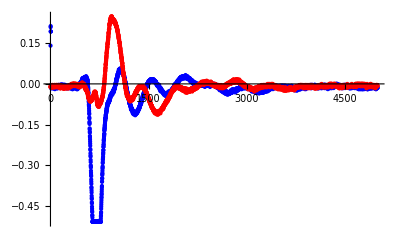

```mathematica
ListPlot[{Rawcos,Rawsin},PlotRange->All,PlotStyle->{Blue,Red}]
```

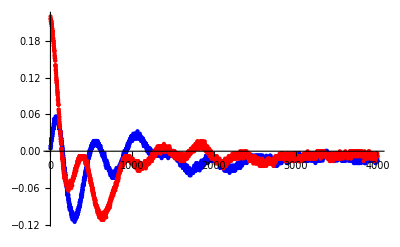

```mathematica
RawcosT=Table[Data[[i]][[1]],{i,1001,5000}];
RawsinT=Table[Data[[i]][[2]],{i,1001,5000}];
ListPlot[{RawcosT,RawsinT},PlotRange->All,PlotStyle->{Blue,Red}]
```

```mathematica
(* FT mathematica *)
FT[cos_,sin_]:=Shift[Fourier[cos+ⅈ sin,FourierParameters->{1,-1}]];
```

```mathematica
FTM=FT[Rawcos, Rawsin];
FTMT=FT[RawcosT, RawsinT];
```

```mathematica
(* Test on Shift function *)
Manipulate[{"i="<>ToString[i],Mod[i+Length[FTM]/2-1,Length[FTM]]+1},{{i,2001},1,Length[FTM],1}]
```

```mathematica
Manipulate[{"i="<>ToString[i],Mod[i+Length[FTMT]/2-1,Length[FTMT]]+1},{{i,2001},1,Length[FTMT],1}]
```

```mathematica
(* Plot Re_Im *)
PlotReIm[ft_,l1_,l2_]:=ListPlot[{Re[ft],Im[ft]},PlotRange->{{Length[ft]/2-l1,Length[ft]/2+l2},All},Joined->True, Epilog->{Arrow[{{Length[ft]/2+1,0.5},{Length[ft]/2+1,0}}]},PlotMarkers->Automatic, ImageSize->500,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
PlotAmp[ft_,l_]:=ListPlot[√(Re[ft]^2+Im[ft]^2),PlotRange->{{Length[ft]/2-l,Length[ft]/2+l},{0,All}},Joined->True, Epilog->{Arrow[{{Length[ft]/2+1,0.5},{Length[ft]/2+1,0}}]},PlotMarkers->Automatic, ImageSize->500,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

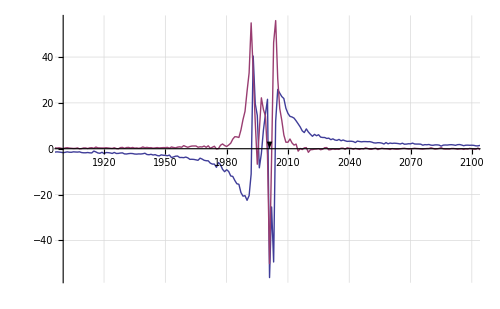

```mathematica
PlotReIm[FTMT,100]
```

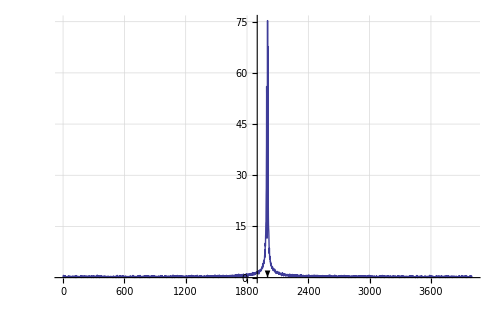

```mathematica
PlotAmp[FTMT,100]
```

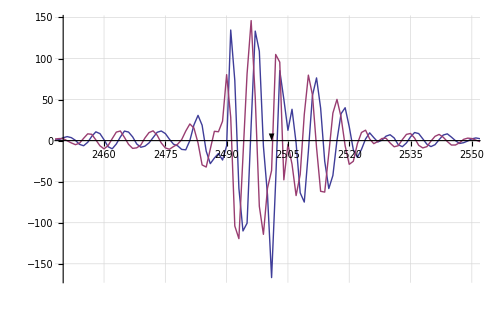

```mathematica
PlotReIm[FTM,50]
```

```mathematica
(* Data From FFTW *)
PlotReIm[FTM,50]
```

-Graphics-

## Determine the frequnecy increasment direction

```mathematica
CosData=Table[Cos[2π 0.1t]Exp[-t],{t,20/20000,200,20/100}];
SinData=Table[Sin[2π 0.1t]Exp[-t],{t,20/20000,200,20/100}];
timeData=Table[t,{t,20/20000,200,20/100}];
testFT=FT[CosData, SinData];
Length[testFT]
f=1/(timeData[[-1]]-timeData[[1]])//N
```

1000

0.00500501

```mathematica
0.1/f+1//N
```

20.98

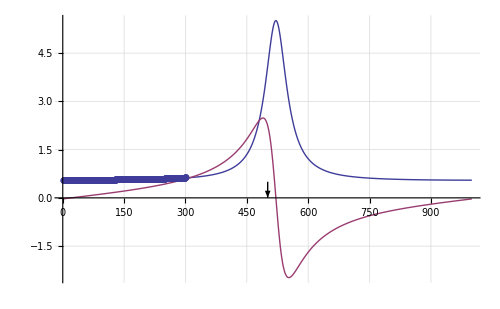

```mathematica
PlotReIm[testFT,-50,50]
```